## Estimates of times

## Plots

```mathematica
Ex=E1 Exp[ⅈ (-k t+δ)];Ey=E2 Exp[-ⅈ k t];rul={E1->1,E2->1,δ->π/2,k->3};sc=10;
Plot[{Re[Ex]/.rul,Re[Ey]/.rul},{t,0,2π},PlotStyle->{Red,Blue},PlotLabel->"Ex - red, Ey - blue",ImageSize->400];
tplrot=ParametricPlot3D[{t,u Re[Ex]/.δ->π/2/.rul,u Re[Ey]/.δ->π/2/.rul},{t,0,2π},{u,0.5,1},AxesLabel->{"t",Null,Null},Axes->{True,False,False},PlotLabel->"clockwise rotation in fixed plane: δ>0",PlotStyle->Green,Mesh->False,PlotPoints->70,BaseStyle->{17,Bold},BoxStyle->{AbsoluteThickness[2]},ImageSize->400,ViewPoint->{40sc,10sc,10sc},ViewVertical->{0,1,0}]
Ex=E1 Exp[ⅈ (k z+δ)];Ey=E2 Exp[ⅈ k z];rul={E1->1,E2->1,δ->π/2,k->3};sc=10;
Plot[{Re[Ex]/.rul,Re[Ey]/.rul},{z,0,2π},PlotStyle->{Red,Blue},PlotLabel->"Ex - red, Ey - blue",ImageSize->400];
zplrot=ParametricPlot3D[{z,u Re[Ex]/.δ->π/2/.rul,u Re[Ey]/.δ->π/2/.rul},{z,0,2π},{u,0.5,1},AxesLabel->{"z",Null,Null},Axes->{True,False,False},PlotLabel->"right-handed rotation along the ray: δ>0",PlotStyle->Green,Mesh->False,PlotPoints->70,BaseStyle->{17,Bold},BoxStyle->{AbsoluteThickness[2]},ImageSize->400,ViewPoint->{40sc,10sc,10sc},ViewVertical->{0,1,0}]
```

```mathematica
dir="C:\\study\\accretion\\! 2009 summer cfa\\GR Polarized Radiative Transfer\\";
Export[dir<>"tplrot.eps",Rasterize[tplrot,RasterSize->500]]
Export[dir<>"tplrot.jpg",tplrot,"CompressionLevel"->0,"Progressive"->True]
Export[dir<>"zplrot.eps",Rasterize[zplrot,RasterSize->500]]
Export[dir<>"zplrot.jpg",zplrot,"CompressionLevel"->0,"Progressive"->True]

Export[dir<>"tplrotx.pdf",Rasterize[tplrot,RasterSize->1000]]

Export[dir<>"zplrot.pdf",Rasterize[zplrot,RasterSize->500]]
```

## New integration (instead of θ integral left we have ξ integral left)

Gradstein, Ryzhik, p.502

```mathematica
(*p==q==0*)p=0;q=0.;a=15.4;b=2.1;m=2;A=p^2-q^2+a^2-b^2;B=2(p q+a b);CC=p^2+q^2-a^2-b^2;DD=-2(a p+b q);
Print[InputForm[NIntegrate[Exp[p Cos[x]+q Sin[x]]Sin[a Cos[x]+b Sin[x]-m x],{x,0,2π}]]]
If[EvenQ[m],
Print[InputForm[Chop[ⅈ π (((A+ⅈ B)/((b-p)^2+(a+q)^2))^(m/2)BesselI[m,√(CC-ⅈ DD)]-((A-ⅈ B)/((b-p)^2+(a+q)^2))^(m/2)BesselI[m,√(CC+ⅈ DD)])]]],
(*Print[InputForm[Chop[-ⅈ π ((b-p)^2+(a+q)^2)^(-m/2.)((A+ⅈ B)^(m/2)+(A-ⅈ B)^(m/2))BesselI[m,√(CC+ⅈ DD)]]]]*)
Print[InputForm[Chop[-ⅈ π (((A+ⅈ B)/((b-p)^2+(a+q)^2))^(m/2)+((A-ⅈ B)/((b-p)^2+(a+q)^2))^(m/2))BesselI[m,√(CC+ⅈ DD)]]]]]
```

```mathematica
p=0;q=0.;a=15.4;b=2.1;m=1;Clear[m,p,q,a,b];A=p^2-q^2+a^2-b^2;B=2(p q+a b);CC=p^2+q^2-a^2-b^2;DD=-2(a p+b q);
expr=ⅈ π (((A+ⅈ B)/((b-p)^2+(a+q)^2))^(m/2)BesselI[m,√(CC-ⅈ DD)]-((A-ⅈ B)/((b-p)^2+(a+q)^2))^(m/2)BesselI[m,√(CC+ⅈ DD)]);
exx=FullSimplify[expr/.{q->0,p->0},{a>0,b>0}]
derq=FullSimplify[D[expr,q]/.{q->0,p->0},{a>0,b>0}]
```

```mathematica
Clear[a,b,y,m];a=Cos[y];b=Sin[y];FullSimplify[exx/.m->4,y>0]
```

```mathematica
a=Cos[y];b=Sin[y];m=6;y=1.;
Print[InputForm[NIntegrate[Sin[a Cos[x]+b Sin[x]-m x],{x,0,2π}]]]
Print[InputForm[NIntegrate[Sin[a Cos[x]+b Sin[x]-m x],{x,0,π}]]]
Print[InputForm[(-1)^(m/2+1)2 π BesselJ[m,1] Sin[m y]]]
```

```mathematica
TrigExpand[Cos[x-y]]
Clear[y];Clear[m,a,b];a=Cos[y];b=Sin[y];
FullSimplify[Sin[a Cos[x]+b Sin[x]-m x]]
```

2 π (-1)^(m/2+1)BesselJ[m,1]Sin[m y]→-2Sin[m y]∫_0^π Cos[Cos[x]] Cos[m x]ⅆx  ← ∫_0^(2π) Sin[-m x+Cos[x-y]]ⅆx→∫_y^(2π+y) Sin[-m x-my+Cos[x]]ⅆx(*x→x+y*)→
(*periodic ⇒ can't shift the limits of integration*)∫_0^(2π) Sin[-m x-my+Cos[x]]ⅆx→∫_0^(2π) (-Cos[m x] Cos[Cos[x]] Sin[my]-Cos[my] Cos[Cos[x]] Sin[m x]+Cos[my] Cos[m x] Sin[Cos[x]]-Sin[my] Sin[m x] Sin[Cos[x]])ⅆx→
∫_0^(2π) -Cos[m x] Cos[Cos[x]] Sin[my]ⅆx(*other terms are zero*)→-2 Sin[my]∫_0^π Cos[m x] Cos[Cos[x]]ⅆx(*from symmetry*)


∫_0^π Sin[-m x+Cos[x-y]]ⅆx →∫_y^(π+y) Sin[-m x-my+Cos[x]]ⅆx→ ∫_y^(π+y) (-Cos[m x] Cos[Cos[x]] Sin[my]-Cos[my] Cos[Cos[x]] Sin[m x]+Cos[my] Cos[m x] Sin[Cos[x]]-Sin[my] Sin[m x] Sin[Cos[x]])ⅆx→
∫_0^π (-Cos[m x] Cos[Cos[x]] Sin[my])ⅆx+Cos[my]∫_y^(π+y) Cos[m x] Sin[Cos[x]]ⅆx-Sin[my]∫_y^(π+y) Sin[m x] Sin[Cos[x]]ⅆx

```mathematica
TrigExpand[Sin[-m x-my+Cos[x]]]
xoxo=(-Cos[m x] Cos[Cos[x]] Sin[my]-Cos[my] Cos[Cos[x]] Sin[m x]+Cos[my] Cos[m x] Sin[Cos[x]]-Sin[my] Sin[m x] Sin[Cos[x]]);
Integrate[xoxo[[#]]/.m->2,{x,0,2π}]&/@Range[4]
```

```mathematica
Sin[-m x+Cos[x-y]]
```

```mathematica
Integrate[Sin[m x] Sin[Cos[x]]/.m->2,x]
Integrate[Cos[m x] Sin[Cos[x]]/.m->2,x]
```

```mathematica
z=0.4;
NIntegrate[Cos[Cos[x]] Cos[m x]/.m->2,{x,0+z,π+z}]
NIntegrate[Cos[Cos[x]] Sin[m x]/.m->2,{x,0+z,π+z}]
NIntegrate[Cos[Sin[x]] Sin[m x]/.m->2,{x,0+z,π+z}]
NIntegrate[Cos[Sin[x]] Cos[m x]/.m->2,{x,0+z,π+z}]
NIntegrate[Sin[Cos[x]] Cos[m x]/.m->2,{x,0+z,π+z}]
NIntegrate[Sin[Cos[x]]Sin[m x]/.m->2,{x,0+z,π+z}]
```

```mathematica
∫_0^π ⅇ^(ⅈ Cos[x]) Cos[2 x]ⅆx
∫_0^π Cos[Cos[x]] Cos[2 x]ⅆx
ⅈ∫_0^π Sin[Cos[x]] Cos[2 x]ⅆx
```

```mathematica
Simplify[(-1)^(m/2+1)ⅈ^-m]
```

BesselJ[n,z]==ⅈ^-n/π∫_0^π ⅇ^(ⅈ z Cos[t]) Cos[n t]ⅆt/;Element[n,Integers]∧n>0

```mathematica
ff[B_]:=NIntegrate[Sin[(B Cos[θ])]Cos[θ],{θ,0,π}]
Integrate[Exp[ⅈ(B Sin[θ])]Sin[θ],{θ,0,π},GenerateConditions->False]
Integrate[Exp[ⅈ(A Cos[θ])]Sin[θ],{θ,0,π},GenerateConditions->False]
```

## Polarized radiative transfer

### Q, U → amplitude & angle

```mathematica
fullsys=FullSimplify[Thread[D[{Ic[s],Qc[s],Uc[s],Vc[s]},s]==({jIc,jQc Cos[2χ[s]],jQc Sin[2χ[s]],jVc}+{{-αIc,-αQc Cos[2χ[s]],-αQc Sin[2χ[s]],-αVc},{-αQc Cos[2χ[s]],-αIc,-ρVc,ρQc Sin[2χ[s]]},{-αQc Sin[2χ[s]],ρVc,-αIc,-ρQc Cos[2χ[s]]},{-αVc,-ρQc Sin[2χ[s]],ρQc Cos[2χ[s]],-αIc}}.{Ic[s],Qc[s],Uc[s],Vc[s]})]];
```

```mathematica
{{I'[s]==det*(jIc/fr/fr+fr*(-aIc*yyy[0]-aQc*cos2k*yyy[1]-aQc*sin2k*yyy[2]-aVc*yyy[3]))},
{Q'[s]==det*((cos2k*jQc)/fr/fr+fr*(-(aQc*cos2k*yyy[0])-aIc*yyy[1]-rVc*yyy[2]+rQc*sin2k*yyy[3]))},
{U'[s]==det*((jQc*sin2k)/fr/fr+fr*(-(aQc*sin2k*yyy[0])+rVc*yyy[1]-aIc*yyy[2]-cos2k*rQc*yyy[3]))},
{V'[s]==det*(jVc/fr/fr+fr*(-(aVc*yyy[0])-rQc*sin2k*yyy[1]+cos2k*rQc*yyy[2]-aIc*yyy[3]))}}
```

```mathematica
subyy={yyy[1]->IQ[s]*Cos[qϕ[s]],yyy[2]->IQ[s]*Sin[qϕ[s]]};
subff={ff[1]->D[yyy[1]/.subyy,s],ff[2]->D[yyy[2]/.subyy,s]};
sub=Flatten[{subyy,subff}]
```

```mathematica
sys={{ff[0]==det*(jIc/fr/fr+fr*(-aIc*yyy[0]-aQc*cos2k*yyy[1]-aQc*sin2k*yyy[2]-aVc*yyy[3]))},
{ff[1]==det*((cos2k*jQc)/fr/fr+fr*(-(aQc*cos2k*yyy[0])-aIc*yyy[1]-rVc*yyy[2]+rQc*sin2k*yyy[3]))},
{ff[2]==det*((jQc*sin2k)/fr/fr+fr*(-(aQc*sin2k*yyy[0])+rVc*yyy[1]-aIc*yyy[2]-cos2k*rQc*yyy[3]))},
{ff[3]==det*(jVc/fr/fr+fr*(-(aVc*yyy[0])-rQc*sin2k*yyy[1]+cos2k*rQc*yyy[2]-aIc*yyy[3]))}}
```

```mathematica
InputForm[{Flatten[sys/.sub][[1]],Flatten[sys/.sub][[4]]}/.{IQ[s]->yyy[1],Sin[qϕ[s]]->sinqs,Cos[qϕ[s]]->cosqs}]
```

```mathematica
soll=Simplify[Solve[Flatten[sys/.sub][[2;;3]],{IQ'[s],qϕ'[s]}][[1]]]/.{IQ[s]->yyy[1],Sin[qϕ[s]]->sinqs,Cos[qϕ[s]]->cosqs}
```

```mathematica
InputForm[Collect[soll,fr]/.{IQ'[s]->ff[1],qϕ'[s]->ff[2]}]
```

### Q, U, V → amplitude & 2 angles

```mathematica
fullsys=FullSimplify[Thread[D[{Ic[s],Qc[s],Uc[s],Vc[s]},s]==({jIc,jQc Cos[2χ[s]],jQc Sin[2χ[s]],jVc}+{{-αIc,-αQc Cos[2χ[s]],-αQc Sin[2χ[s]],-αVc},{-αQc Cos[2χ[s]],-αIc,-ρVc,ρQc Sin[2χ[s]]},{-αQc Sin[2χ[s]],ρVc,-αIc,-ρQc Cos[2χ[s]]},{-αVc,-ρQc Sin[2χ[s]],ρQc Cos[2χ[s]],-αIc}}.{Ic[s],Qc[s],Uc[s],Vc[s]})]];
```

```mathematica
{{I'[s]==det*(jIc/fr/fr+fr*(-aIc*yyy[0]-aQc*cos2k*yyy[1]-aQc*sin2k*yyy[2]-aVc*yyy[3]))},
{Q'[s]==det*((cos2k*jQc)/fr/fr+fr*(-(aQc*cos2k*yyy[0])-aIc*yyy[1]-rVc*yyy[2]+rQc*sin2k*yyy[3]))},
{U'[s]==det*((jQc*sin2k)/fr/fr+fr*(-(aQc*sin2k*yyy[0])+rVc*yyy[1]-aIc*yyy[2]-cos2k*rQc*yyy[3]))},
{V'[s]==det*(jVc/fr/fr+fr*(-(aVc*yyy[0])-rQc*sin2k*yyy[1]+cos2k*rQc*yyy[2]-aIc*yyy[3]))}}
```

```mathematica
subyy={yyy[1]->IQ[s]*Cos[qϕ[s]]Sin[qth[s]],yyy[2]->IQ[s]*Sin[qϕ[s]]Sin[qth[s]],yyy[3]->IQ[s]Cos[qth[s]]};
subff={ff[1]->D[yyy[1]/.subyy,s],ff[2]->D[yyy[2]/.subyy,s],ff[3]->D[yyy[3]/.subyy,s]};
sub=Flatten[{subyy,subff}]
```

```mathematica
sys={{ff[0]==det*(jIc/fr/fr+fr*(-aIc*yyy[0]-aQc*cos2k*yyy[1]-aQc*sin2k*yyy[2]-aVc*yyy[3]))},
{ff[1]==det*((cos2k*jQc)/fr/fr+fr*(-(aQc*cos2k*yyy[0])-aIc*yyy[1]-rVc*yyy[2]+rQc*sin2k*yyy[3]))},
{ff[2]==det*((jQc*sin2k)/fr/fr+fr*(-(aQc*sin2k*yyy[0])+rVc*yyy[1]-aIc*yyy[2]-cos2k*rQc*yyy[3]))},
{ff[3]==det*(jVc/fr/fr+fr*(-(aVc*yyy[0])-rQc*sin2k*yyy[1]+cos2k*rQc*yyy[2]-aIc*yyy[3]))}};
```

```mathematica
InputForm[Flatten[sys/.sub][[1]]/.{IQ[s]->yyy[1],Sin[qϕ[s]]->sinqs,Cos[qϕ[s]]->cosqs,Sin[qth[s]]->sinths,Cos[qth[s]]->cosths,1/fr^2->1/frsq}]
```

```mathematica
soll=Simplify[Solve[Flatten[sys/.sub][[2;;4]],{IQ'[s],qϕ'[s],qth'[s]}][[1]]]/.{IQ[s]->yyy[1],Sin[qϕ[s]]->sinqs,Cos[qϕ[s]]->cosqs,Sin[qth[s]]->sinths,Cos[qth[s]]->cosths,Csc[qth[s]]->1/sinths, Cot[qth[s]]->cosths/sinths}
```

```mathematica
Collect[Collect[soll,fr],det]/.1/fr^2->1/frsq
```

```mathematica
InputForm[Collect[Collect[soll,fr],det]/.1/fr^2->1/frsq/.{IQ'[s]->ff[1],qϕ'[s]->ff[2],qth'[s]->ff[3]}]
```

## Plots to paper Shcherbakov, Penna, McKinney (2010)

### Averaging simulations

```mathematica
fnum=6950;
imp=Table[Import["E:\\mathematica\\3DMHD\\poliresa90th223fn"<>ToString[fnum]<>"boo.dat"],{fnum,6950,9950,300}];
pol=imp[[All,All,4]];
Mean[pol]
Exp[Mean[Log[pol]]]
Median[pol]
```

```mathematica
Pi/2.*(2*cas-1)/50/.cas->36
Pi/2.*(2*cas-1)/50/.cas->21
```

### New data compilation (Figure 1) - done

#### all linear - best

```mathematica
her2cm=Import[NotebookDirectory[]<>"Herrstein_2cm.xlsx"][[1]];
her13mm=Import[NotebookDirectory[]<>"Herrstein_13mm.xlsx"][[1]];
her7mm=Import[NotebookDirectory[]<>"Herrstein_7mm.xlsx"][[1]];
dat2cm=Transpose[her2cm][[2]];dat13mm=Transpose[her13mm][[2]];dat7mm=Transpose[her7mm][[2]];
```

```mathematica
F8={0.73,0.59,0.72,0.69};
F15=Flatten[{dat2cm,{1.1,0.81,1.03,0.92,0.94}}];
F22=Flatten[{dat13mm,{1.05,1.6,0.94,1.75,1.1,1.05,1.06}}];
F43=Flatten[{dat7mm,{1.03,1.1 ,2.02, 1.9, 1.92, 1.78,2.02, 1.59, 1.99, 1.61, 1.86 ,1.66,1.45,1.07,2.3,1.4,1.6}}];
F88={1.715, 1.352, 2.374,1.73,1.2, 1.6,(*3.5,*)1.96, 1.97, 1.69, 1.73, 2.18,1.8,1.4,1.7, 2.2, 1.7,2.6,1.2,2,2.1,2.4,1.9};
F102={1.9, 1.4 ,1.8 ,1.7,1.2,2 ,2.7, 1.9, 3 ,1.2 ,1.5,2.1,2.4};
F145={1.1 ,2.2, 2 ,3.6,2.5, 2.1,2.9,1.8};
F230={2,2.2,3.6,1.14,2.3, 2.7, 2.3, 2.8, 2.6,2.4, 2.1, 1.9 ,2.15, 3.1, 2.4,4.05, 3.3, 3.8 ,1.9 ,2.5, 3 ,2.5,0.7, 1.23, 0.87, 1.52,3.43, 3.86, 3.79 ,3.79 ,3.33 ,4.14,1.3, 2.5, 1.7, 1.8,2.4,2.9, 3.4,4,3,2.8,4.2};
F345={4.18 ,3.31, 2.98, 3.8,3.79, 3.16, 3.2 ,3.18 ,2.75, 3.02, 3.31,3,2.9,2.3,2.83};
F674={2.9 ,3, 3,3.8,2 ,3.3 ,5};
F857={2.4 ,3,3.2};

LP43={0.33,0.77};
LP88={1.01,0.7,0.96,2.1,0.8};LP88=0.1{39/1.94,32/1.96,33/1.71,34/1.69,58/2.12,14/1.98,16/1.97,4/1.68,10/1.76,35/2.25};
LP230={8.8, 8.7, 13.6, 7.8 ,9.4,4.57, 6.84, 5.27, 4.59, 4.5,8 ,10, 8, 5,5.9};
LP345={5.38, 5.35, 9.51, 8.25,6.07, 5.75, 8.52, 5.78 ,2.32, 8.17 ,6.39};

EVPA88={-32.6,-12.1 ,26.5,-39.1,15.2 ,18};
EVPA230={109, 113, 109 ,86 ,116,146.8 ,88.6 ,122 ,134 ,84.5 ,114.8,114};
EVPA345={149.7 ,141, 148.6, 158.8,136.7 ,155.3, 139.5 ,143.2 ,156.1, 143.8 ,143.1};
acc=10^-4.;Off[HypothesisTestData::ties];
data=F8;Print["F_8.4:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F15;Print["F_14.9:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F22;Print["F_22:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F43;Print["F_43:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F88;Print["F_86:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F102;Print["F_102:      <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F145;Print["F_145:      <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F230;Print["F_230:      <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F345;Print["F_345:      <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F674;Print["F_674:      <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F857;Print["F_857:      <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=LP43;Print["LP_43: <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=LP88;Print["LP_88: <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=LP230;Print["LP_230: <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=LP345;Print["LP_345: <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=EVPA88;Print["EVPA_88:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=EVPA230;Print["EVPA_230:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=EVPA345;Print["EVPA_345:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
```

```mathematica
meF=Mean[#]&/@{F8,F15,F22,F43,F88,F102,F145,F230,F345,F674,F857}
deF=StandardDeviation[#]/√Length[#]&/@{F8,F15,F22,F43,F88,F102,F145,F230,F345,F674,F857}
meLP=Mean[#]&/@{LP43,LP88,LP230,LP345}
deLP=StandardDeviation[#]/√Length[#]&/@{LP43,LP88,LP230,LP345};deLP[[2]]=0.50;deLP
meEVPA=Mean[#]&/@{EVPA88,EVPA230,EVPA345}
deEVPA=StandardDeviation[#]/√Length[#]&/@{EVPA88,EVPA230,EVPA345}
fr={8,15,22,43,88,102,145,230,345,674,857};
lpl=ListLogLinearPlot[{Transpose[{fr,meF-deF}],Transpose[{fr,meF+deF}]},Joined->True];
pl=LogLinearPlot[2.87(x/230)^0.45 Exp[-(x/1100)^2],{x,8,857},PlotStyle->{AbsoluteThickness[1.5],AbsoluteDashing[{5,5}],Red}];
Show[{pl,lpl},PlotRange->All];
```

```mathematica
freqLP
meLP
xLP=Transpose[{freqLP,meLP}]
xLPnu=Join[Partition[xLP,1],Partition[ErrorBar/@deLP,1],2]
xLPnu
```

```mathematica
Needs["ErrorBarPlots`"];Needs["ErrorBarLogPlots`"];
freq={8.450,14.90,22.50,43.00,87.73,102.0,145.0,230.9,349.0,674.0,857.0};freqLP={43,87.73,230.9,349};
Fnu=Transpose[{freq,meF}];
xFnu=Join[Partition[Fnu,1],Partition[ErrorBar/@deF,1],2];
el={LogLogPlot,ListLogLogPlot,ListLogLinearPlot,ErrorListLogLogPlot,ErrorListLogLinearPlot};Clear[totI];xcol=Cyan;myf=14;siz=380;
SetOptions[#,Frame->True,BaseStyle->{(*FontFamily->"Arial",*)FontWeight->"Bold",FontSize->myf},PlotStyle->AbsoluteThickness[2.5],FrameStyle->AbsoluteThickness[2.5],FrameTicks->{{Automatic,None},{(*{10,20,50,100,200,500}*){8,15,22,43,88,145,231,349,690},None}}]&/@el;lpl1=ErrorListLogLogPlot[xFnu,Joined->True,PlotRange->{{7,950},{0.6,3.9}},Frame->True,FrameLabel->{{Null,Null},{Null,"F_ν [Jy]"}},ImageSize->siz(*,PlotStyle->{AbsolutePointSize[6],Blue}*)];
lpl=ListLogLogPlot[{Transpose[{freq,meF+deF}],Transpose[{freq,meF-deF}]},Filling->{1->{2}},FillingStyle->LightCyan,Joined->True,PlotRange->{{7,950},{0.6,3.9}},Frame->True,FrameLabel->{{Null,Null},{Null,"F_ν [Jy]"}},ImageSize->siz,PlotStyle->AbsoluteThickness[0.5](*,Epilog->{PointSize[0.02],xcol,Point[Log[{{8.45,0.72},{14.9,1.03},{23,1.1},{43,1.4},{93,1.9},{220,3.8},{350,4.1},{690,2.7}}]]}*)];
pl=LogLogPlot[2.87(x/230)^0.45 Exp[-(x/1100)^2],{x,8.45,857},PlotStyle->{AbsoluteThickness[1.5],AbsoluteDashing[{5,5}],Red}];
Fnupl=Show[lpl,lpl1,pl];

freqLP={43,87.73,230.9,349};
xLP=Transpose[{freqLP,meLP}];
xLPnu=Join[Partition[xLP,1],Partition[ErrorBar/@deLP,1],2];

lpl1=ErrorListLogLogPlot[xLPnu,Joined->True,PlotRange->{{35,400},{0.3,10}},Frame->True,FrameLabel->{{Null,Null},{Null,"LP [%]"}},ImageSize->siz];
lpl=ListLogLogPlot[{Transpose[{freqLP,meLP+1.2deLP}],Transpose[{freqLP,meLP-0.85deLP}]},Filling->{1->{2}},FillingStyle->LightCyan,Joined->True,PlotRange->{{35,400},{0.3,10}},Frame->True,FrameLabel->{{Null,Null},{Null,"LP [%]"}},ImageSize->siz,PlotStyle->AbsoluteThickness[0.5]];
LPnupl=Show[lpl,lpl1];

CPnu={{8.45,-0.25},{14.90,-0.62},{231,-1.2},{349,-1.5}};CPf=Transpose[CPnu][[1]];CPtr=Transpose[CPnu][[2]];
freqCP=Transpose[CPnu][[1]];meCP=Transpose[CPnu][[2]];
dCP={0.06,0.26,0.3,0.3};xCPnu=Join[Partition[CPnu,1],Partition[ErrorBar/@dCP,1],2];
lpl1=ErrorListLogLinearPlot[xCPnu,Joined->False,Frame->True,PlotRange->{{7,400},{-2.,-0.1}},FrameLabel->{{Null,Null},{Null,"CP [%]"}},ImageSize->siz];
lpl=ListLogLinearPlot[{Transpose[{freqCP,meCP+dCP}],Transpose[{freqCP,meCP-dCP}]},Filling->{1->{2}},FillingStyle->LightCyan,Joined->True,PlotRange->{{7,400},{-2.,-0.1}},Frame->True,FrameLabel->{{Null,Null},{Null,"CP [%]"}},ImageSize->siz,PlotStyle->AbsoluteThickness[0.5]];
CPnupl=Show[lpl,lpl1];

freqEVPA={88,231,349};xEVPA=Transpose[{freqEVPA,meEVPA}];ran={{75,400},{-30.,170}};
xEVPAnu=Join[Partition[xEVPA,1],Partition[ErrorBar/@deEVPA,1],2];
lpl1=ErrorListLogLinearPlot[xEVPAnu,Joined->False,Frame->True,PlotRange->ran,ImageSize->siz];
lpl=ListLogLinearPlot[{Transpose[{freqEVPA,meEVPA+deEVPA}],Transpose[{freqEVPA,meEVPA-deEVPA}]},Filling->{1->{2}},FillingStyle->LightCyan,FrameLabel->{{Null,Null},{Null,"Electric vector position angle [deg]"}},Joined->True,PlotRange->ran,Frame->True,ImageSize->siz,PlotStyle->AbsoluteThickness[0.5]];
(*sol=FindFit[xEVPA[[2;;3]],A+B/f^2,{A,B},f];
lfi=LogLinearPlot[A+B/f^2/.sol,{f,70,400},PlotRange->ran,Frame->True,ImageSize->siz,PlotStyle->AbsoluteThickness[0.5]];*)
EVPAnupl=Show[lpl,lpl1(*,lfi*)];

totimag=GraphicsGrid[{{Fnupl,EVPAnupl},{LPnupl,CPnupl}},Epilog->{Black,Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.43,0.53}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.43,0.03}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.955,0.53}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.955,0.03}]]},BaseStyle->{FontWeight->"Bold",FontSize->myf-2},PlotLabel->"Compilation of observations"](*FontFamily->"Arial",*)
dir="C:\\study\\accretion\\! 2009 3fall cfa\\GR Polarized modeling\\!svn\\";
(*Export[dir<>"SED.eps",totimag,"EmbeddedFonts"->True]*)
(*Export[dir<>"SED.pdf",totimag]*)
```

```mathematica
Length[ror={0.01,3,3,3,3,3,3,3,3,3,3}]
Mean[ror]
Exp[Mean[Log[ror]]]
```

200 cores at a time ⇒ 25 tasks at a time; 6hr - each task
7*50=350 tasks

```mathematica
Print[350/25*6/24.," days to finish"]
Print[350*8*6," CPU-hours"]
```

#### old new

```mathematica
Fnu={{8.45, 0.68982013},{14.90 ,0.904431774},{22.50 ,1.070321246},{43.00 ,1.15943163},{87.73 ,1.58443741},{102.00, 1.415119175},{145.00 ,2.24570193},{230.86 ,2.181905886},{349.00 ,3.065050156},{674.00 ,3.2033626},{857.00 ,2.786327907}};
LPnu={{22.50, 0.19},{43.00 ,0.504083326},{87.73 ,1.11},{230.86, 7.61271},{349.00 ,7.03}};
angnu={{22.50 ,131},{43.00, 94.25},{87.73, 102.7777778},{230.86, 117},{349.00, 148.1428571}};
CPnu={{8.45,-0.25},{14.90,-0.62},{230,-1.2},{349,-1.5}};dFnu=0.33;dCP=0.27;dlogLP=0.26;
Ff=Transpose[Fnu][[1]];Ftr=Transpose[Fnu][[2]];LPf=Transpose[LPnu][[1]];LPtr=Transpose[LPnu][[2]];
CPf=Transpose[CPnu][[1]];CPtr=Transpose[CPnu][[2]];
```

```mathematica
el={ListLogLogPlot,ListLogLinearPlot,LogLogPlot};Clear[totI];xcol=Green;siz=280;myf=15;
SetOptions[#,Frame->True,BaseStyle->{(*FontFamily->"Arial",*)FontWeight->"Bold",FontSize->myf},PlotStyle->AbsoluteThickness[2.5],FrameStyle->AbsoluteThickness[2.5](*,FrameTicks->{{Automatic,None},{(*{10,20,50,100,200,500}*){43,87,145,230,345,690},None}}*)]&/@el;lpl=ListLogLogPlot[{Transpose[{Ff,Ftr+dFnu}],Transpose[{Ff,Ftr-dFnu}]},Filling->{1->{2}},FillingStyle->LightRed,Joined->True,PlotRange->{0.4,4.7},Frame->True,FrameLabel->{{Null,Null},{Null,"F_ν [Jy]"}},ImageSize->siz(*,Epilog->{PointSize[0.02],xcol,Point[Log[{{23,1.2},{43,1.7},{93,2.2},{220,3.8},{350,4.1},{690,2.7}}]]}*)];
pl=LogLogPlot[0.295 x^0.4 Exp[-(x/1300)^2],{x,8.45,857},PlotStyle->{AbsoluteThickness[1.5],AbsoluteDashing[{5,5}],Red},PlotRange->{0.4,4.7}];
Fnupl=Show[lpl,pl,PlotRange->{Log[0.4],Log[4.7]}];

lpl=ListLogLogPlot[{Transpose[{LPf,LPtr+dlogLP*LPtr}],Transpose[{LPf,LPtr-dlogLP*LPtr}]},Filling->{1->{2}},FillingStyle->LightRed,Joined->True(*,Epilog->{PointSize[0.02],xcol,Point[Log[{{348,8},{220 ,5},{68,2.1},{43,0.8},{22,0.2}}]]}*),Frame->True,FrameLabel->{{Null,Null},{Null,"LP [%]"}},ImageSize->siz];
LPnupl=Show[lpl];

lpl=ListLogLinearPlot[angnu,Joined->True,(*Epilog->{PointSize[0.02],xcol,InterpolationOrder->2,Point[{{Log[348],155},{Log[230],120}}]},*)Frame->True,FrameLabel->{{Null,Null},{Null,"Electric vector position angle [deg]"}},ImageSize->siz,PlotRange->{{87,380},{85,157}}];
angnupl=Show[lpl];

lpl=ListLogLinearPlot[{Transpose[{CPf,CPtr+dCP}],Transpose[{CPf,CPtr-dCP}]},Joined->True,Filling->{1->{2}},FillingStyle->LightRed,Frame->True,FrameLabel->{{Null,Null},{Null,"CP [%]"}},PlotRange->{{8,380},{-1.9,0}},ImageSize->siz];
CPnupl=Show[lpl];
totimag=GraphicsGrid[{{Fnupl,angnupl},{LPnupl,CPnupl}},Epilog->{Black,Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.43,0.55}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.43,0.05}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.955,0.56}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.955,0.05}]]},BaseStyle->{FontWeight->"Bold",FontSize->myf-2}(*,PlotLabel->"Compilation of observations"*)](*FontFamily->"Arial",*)
dir="C:\\study\\accretion\\! 2009 fall cfa\\GR Polarized modeling\\";
dir="D:\\DISKC\\study\\accretion\\conferences\\2010 November - Ins and Outs of the Black Holes\\";
Export[dir<>"SED.eps",totimag,"EmbeddedFonts"->All]
Export[dir<>"SED.pdf",totimag]
```

```mathematica
(*PlotStyle->{AbsoluteThickness[2.5],AbsoluteThickness[2.5],Directive[Blue,PointSize[Large]]}*)
```

#### new

```mathematica
her2cm=Import[NotebookDirectory[]<>"Herrstein_2cm.xlsx"][[1]];
her13mm=Import[NotebookDirectory[]<>"Herrstein_13mm.xlsx"][[1]];
her7mm=Import[NotebookDirectory[]<>"Herrstein_7mm.xlsx"][[1]];
dat2cm=Transpose[her2cm][[2]];dat13mm=Transpose[her13mm][[2]];dat7mm=Transpose[her7mm][[2]];
```

```mathematica
200 1.052^30
1.108*12*30
400*0.035
```

```mathematica
(*LP88 from Macquart et al. 2006*)data=0.1{39/1.94,32/1.96,33/1.71,34/1.69,58/2.12,14/1.98,16/1.97,4/1.68,10/1.76,35/2.25};
md=Exp[Mean[Log[data]]]
hah={Log[md-0.5]-Log[md],Log[md+0.5]-Log[md]}
gm=GeometricMean[Abs[hah]]
Print["LP88=",md,"+(",Exp[Log[md]+gm]-md,")",Exp[Log[md]-gm]-md]
acc=10^-3.;err=Floor[StandardDeviation[data]/√Length[data],acc];
```

```mathematica
F8={0.73,0.59,0.72,0.69};
F15=Flatten[{dat2cm,{1.1,0.81,1.03,0.92,0.94}}];
F22=Flatten[{dat13mm,{1.05,1.6,0.94,1.75,1.1,1.05,1.06}}];
F43=Flatten[{dat7mm,{1.03,1.1 ,2.02, 1.9, 1.92, 1.78,2.02, 1.59, 1.99, 1.61, 1.86 ,1.66,1.45,1.07,2.3,1.4,1.6}}];
F88={1.715, 1.352, 2.374,1.73,1.2, 1.6,(*3.5,*)1.96, 1.97, 1.69, 1.73, 2.18,1.8,1.4,1.7, 2.2, 1.7,2.6,1.2,2,2.1,2.4,1.9};
F102={1.9, 1.4 ,1.8 ,1.7,1.2,2 ,2.7, 1.9, 3 ,1.2 ,1.5,2.1,2.4};
F145={1.1 ,2.2, 2 ,3.6,2.5, 2.1,2.9,1.8};
F230={2,2.2,3.6,1.14,2.3, 2.7, 2.3, 2.8, 2.6,2.4, 2.1, 1.9 ,2.15, 3.1, 2.4,4.05, 3.3, 3.8 ,1.9 ,2.5, 3 ,2.5,0.7, 1.23, 0.87, 1.52,3.43, 3.86, 3.79 ,3.79 ,3.33 ,4.14,1.3, 2.5, 1.7, 1.8,2.4,2.9, 3.4,4,3,2.8,4.2};
F345={4.18 ,3.31, 2.98, 3.8,3.79, 3.16, 3.2 ,3.18 ,2.75, 3.02, 3.31,3,2.9,2.3,2.83};
F674={2.9 ,3, 3,3.8,2 ,3.3 ,5};
F857={2.4 ,3,3.2};

LP43={0.33,0.77};
LP88={1.01,0.7,0.96,2.1,0.8};LP88=0.1{39/1.94,32/1.96,33/1.71,34/1.69,58/2.12,14/1.98,16/1.97,4/1.68,10/1.76,35/2.25};
LP230={8.8, 8.7, 13.6, 7.8 ,9.4,4.57, 6.84, 5.27, 4.59, 4.5,8 ,10, 8, 5,5.9};
LP345={5.38, 5.35, 9.51, 8.25,6.07, 5.75, 8.52, 5.78 ,2.32, 8.17 ,6.39};

EVPA88={-32.6,-12.1 ,26.5,-39.1,15.2 ,18};
EVPA230={109, 113, 109 ,86 ,116,146.8 ,88.6 ,122 ,134 ,84.5 ,114.8,114};
EVPA345={149.7 ,141, 148.6, 158.8,136.7 ,155.3, 139.5 ,143.2 ,156.1, 143.8 ,143.1};
acc=10^-3.;Off[HypothesisTestData::ties];
data=F8;Print["F_8.4:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F15;Print["F_14.9:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F22;Print["F_22:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F43;Print["F_43:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F88;Print["F_86:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F102;Print["F_102:      <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F145;Print["F_145:      <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F230;Print["F_230:      <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F345;Print["F_345:      <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F674;Print["F_674:      <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=F857;Print["F_857:      <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=Log[LP43];Print["Log(LP_43): <x>=",Floor[Exp[Mean[data]],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=Log[LP88];Print["Log(LP_86): <x>=",Floor[Exp[Mean[data]],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=Log[LP230];Print["Log(LP_230): <x>=",Floor[Exp[Mean[data]],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=Log[LP345];Print["Log(LP_345): <x>=",Floor[Exp[Mean[data]],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=EVPA88;Print["EVPA_88:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=EVPA230;Print["EVPA_230:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
data=EVPA345;Print["EVPA_345:       <x>=",Floor[Mean[data],acc]," σ=",Floor[StandardDeviation[data]/√Length[data],acc]," p=",Floor[DistributionFitTest[data,Automatic,"KolmogorovSmirnov"],acc]]
```

```mathematica
meF=Mean[#]&/@{F8,F15,F22,F43,F88,F102,F145,F230,F345,F674,F857}
deF=StandardDeviation[#]/√Length[#]&/@{F8,F15,F22,F43,F88,F102,F145,F230,F345,F674,F857}
meLP=Exp[Mean[#]]&/@Log[{LP43,LP88,LP230,LP345}]
deLP=StandardDeviation[#]/√Length[#]&/@Log[{LP43,LP88,LP230,LP345}];deLP[[2]]=0.45;deLP
meEVPA=Mean[#]&/@{EVPA88,EVPA230,EVPA345}
deEVPA=StandardDeviation[#]/√Length[#]&/@{EVPA88,EVPA230,EVPA345}
fr={8,15,22,43,88,102,145,230,345,674,857};
lpl=ListLogLinearPlot[{Transpose[{fr,meF-deF}],Transpose[{fr,meF+deF}]},Joined->True];
pl=LogLinearPlot[2.87(x/230)^0.45 Exp[-(x/1100)^2],{x,8,857},PlotStyle->{AbsoluteThickness[1.5],AbsoluteDashing[{5,5}],Red}];
Show[{pl,lpl},PlotRange->All]
```

```mathematica
2.87(x/230)^0.45 Exp[-(x/1100)^2]
```

```mathematica
Needs["ErrorBarPlots`"];Needs["ErrorBarLogPlots`"];
freq={8.450,14.90,22.50,43.00,87.73,102.0,145.0,230.9,349.0,674.0,857.0};freqLP={43,87.73,230.9,349};
Fnu=Transpose[{freq,meF}];
xFnu=Join[Partition[Fnu,1],Partition[ErrorBar/@deF,1],2];
el={LogLogPlot,ListLogLogPlot,ListLogLinearPlot,ErrorListLogLogPlot,ErrorListLogLinearPlot};Clear[totI];xcol=Cyan;myf=14;siz=380;
SetOptions[#,Frame->True,BaseStyle->{(*FontFamily->"Arial",*)FontWeight->"Bold",FontSize->myf},PlotStyle->AbsoluteThickness[2.5],FrameStyle->AbsoluteThickness[2.5],FrameTicks->{{Automatic,None},{(*{10,20,50,100,200,500}*){8,15,22,43,88,145,231,349,690},None}}]&/@el;lpl1=ErrorListLogLogPlot[xFnu,Joined->True,PlotRange->{{7,950},{0.6,3.9}},Frame->True,FrameLabel->{{Null,Null},{Null,"F_ν [Jy]"}},ImageSize->siz(*,PlotStyle->{AbsolutePointSize[6],Blue}*)];
lpl=ListLogLogPlot[{Transpose[{freq,meF+deF}],Transpose[{freq,meF-deF}]},Filling->{1->{2}},FillingStyle->LightCyan,Joined->True,PlotRange->{{7,950},{0.6,3.9}},Frame->True,FrameLabel->{{Null,Null},{Null,"F_ν [Jy]"}},ImageSize->siz,PlotStyle->AbsoluteThickness[0.5](*,Epilog->{PointSize[0.02],xcol,Point[Log[{{8.45,0.72},{14.9,1.03},{23,1.1},{43,1.4},{93,1.9},{220,3.8},{350,4.1},{690,2.7}}]]}*)];
pl=LogLogPlot[2.87(x/230)^0.45 Exp[-(x/1100)^2],{x,8.45,857},PlotStyle->{AbsoluteThickness[1.5],AbsoluteDashing[{5,5}],Red}];
Fnupl=Show[lpl,lpl1,pl];

freqLP={43,87.73,230.9,349};
posLP=(Exp[Log[meLP]+deLP]-meLP);posLPx=0.85posLP;
negLP=(Exp[Log[meLP]-deLP]-meLP);negLPx=1.2negLP;
xLP=Transpose[{freqLP,meLP}];
xLPnu=Join[Partition[xLP,1],Partition[ErrorBar/@Transpose[{posLPx,negLPx}],1],2];
lpl1=ErrorListLogLogPlot[xLPnu,Joined->True,PlotRange->{{35,400},{0.3,10}},Frame->True,FrameLabel->{{Null,Null},{Null,"LP [%]"}},ImageSize->siz];
lpl=ListLogLogPlot[{Transpose[{freqLP,meLP+posLP}],Transpose[{freqLP,meLP+negLP}]},Filling->{1->{2}},FillingStyle->LightCyan,Joined->True,PlotRange->{{35,400},{0.3,10}},Frame->True,FrameLabel->{{Null,Null},{Null,"LP [%]"}},ImageSize->siz,PlotStyle->AbsoluteThickness[0.5]];
LPnupl=Show[lpl,lpl1];

CPnu={{8.45,-0.25},{14.90,-0.62},{231,-1.2},{349,-1.5}};CPf=Transpose[CPnu][[1]];CPtr=Transpose[CPnu][[2]];
freqCP=Transpose[CPnu][[1]];meCP=Transpose[CPnu][[2]];
dCP={0.06,0.26,0.3,0.3};xCPnu=Join[Partition[CPnu,1],Partition[ErrorBar/@dCP,1],2];
lpl1=ErrorListLogLinearPlot[xCPnu,Joined->False,Frame->True,PlotRange->{{7,400},{-2.,-0.1}},FrameLabel->{{Null,Null},{Null,"CP [%]"}},ImageSize->siz];
lpl=ListLogLinearPlot[{Transpose[{freqCP,meCP+dCP}],Transpose[{freqCP,meCP-dCP}]},Filling->{1->{2}},FillingStyle->LightCyan,Joined->True,PlotRange->{{7,400},{-2.,-0.1}},Frame->True,FrameLabel->{{Null,Null},{Null,"CP [%]"}},ImageSize->siz,PlotStyle->AbsoluteThickness[0.5]];
CPnupl=Show[lpl,lpl1];

freqEVPA={88,231,349};xEVPA=Transpose[{freqEVPA,meEVPA}];ran={{75,400},{-30.,170}};
xEVPAnu=Join[Partition[xEVPA,1],Partition[ErrorBar/@deEVPA,1],2];
lpl1=ErrorListLogLinearPlot[xEVPAnu,Joined->False,Frame->True,PlotRange->ran,ImageSize->siz];
lpl=ListLogLinearPlot[{Transpose[{freqEVPA,meEVPA+deEVPA}],Transpose[{freqEVPA,meEVPA-deEVPA}]},Filling->{1->{2}},FillingStyle->LightCyan,FrameLabel->{{Null,Null},{Null,"Electric vector position angle [deg]"}},Joined->True,PlotRange->ran,Frame->True,ImageSize->siz,PlotStyle->AbsoluteThickness[0.5]];
(*sol=FindFit[xEVPA[[2;;3]],A+B/f^2,{A,B},f];
lfi=LogLinearPlot[A+B/f^2/.sol,{f,70,400},PlotRange->ran,Frame->True,ImageSize->siz,PlotStyle->AbsoluteThickness[0.5]];*)
EVPAnupl=Show[lpl,lpl1(*,lfi*)];

totimag=GraphicsGrid[{{Fnupl,EVPAnupl},{LPnupl,CPnupl}},Epilog->{Black,Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.43,0.53}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.43,0.03}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.955,0.53}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.955,0.03}]]},BaseStyle->{FontWeight->"Bold",FontSize->myf-2},PlotLabel->"Compilation of observations"](*FontFamily->"Arial",*)
dir="C:\\study\\accretion\\! 2009 3fall cfa\\GR Polarized modeling\\svn\\harm_roman\\";
Export[dir<>"SED.eps",totimag,"EmbeddedFonts"->True]
(*Export[dir<>"SED.pdf",totimag]*)
```

200 cores at a time ⇒ 25 tasks at a time; 6hr - each task
7*50=350 tasks

```mathematica
Print[350/25*6/24.," days to finish"]
Print[350*8*6," CPU-hours"]
```

### Dynamical model: velocity, density, B (Figure 4, 5) - done (figures 2, 3 are made outside)

#### Initial setup (just run once)

```mathematica
AppendTo[$Path,"C:\\Program Files\\Wolfram Research\\Mathematica\\LevelScheme-3.52"];Get["LevelScheme`"];
din="C:\\study\\accretion\\! 2009 3fall cfa\\GR Polarized modeling\\Bob_shcherbakov2010\\";
dout="C:\\study\\accretion\\! 2009 3fall cfa\\GR Polarized modeling\\";
n1=256;n2=64;ntot=n1 n2;
a=0.9;rhor=1.4;risco=2.3;Rout=20;ymax=6;

blackhole=Graphics[Disk[{0,0},rhor]];
ISCOline=Graphics[{RGBColor[1,1,1],Thickness[Large],Dashing[{Small,Small}],Line[{{risco,-ymax},{risco,ymax}}]}];

SetOptions[ListDensityPlot,Mesh->False,(* ColorFunction->GrayLevel, *)ColorFunction->"DarkRainbow",BaseStyle->{FontFamily->"Times",FontSize->mysize,FontWeight->Bold},AspectRatio->Automatic,FrameLabel->{"r/M","z/M"},InterpolationOrder->3,PlotRange->{{0,Rout},{-ymax,ymax},All},RegionFunction->Function[{x,y,z},Norm[x]<Rout &&Norm[y]<ymax&& Norm[x^2+y^2]>0.98^2 rhor]];

SetOptions[ListContourPlot,Contours->10,(*ContourLabels->(Text[Style[Round[#3],FontSize->myfontsize],{#1,#2}]&),*)(*ColorFunction->GrayLevel,*)ColorFunction->"Rainbow",AspectRatio->Automatic,BaseStyle->{FontFamily->"Times",FontSize->mysize,FontWeight->Bold},(*FrameStyle->$TextStyle,*)FrameLabel->{"r/M","z/M"},PlotRange->{{0,Rout},{-ymax,ymax}},RegionFunction->Function[{x,y,z},Norm[x]<Rout &&Norm[y]<ymax&& Norm[x^2+y^2]>0.98^2 rhor]];
```

#### Snapshot panel

```mathematica
array=Import[din<>"timeshot14000M/checkmri.dat"];
Do[array[[ii,2]]=0,{ii,1,ntot,n2}]
Do[array[[ii,2]]=π,{ii,64,ntot,n2}]
i=0;
Do[myr=array[[ii,1]];mytheta=array[[ii,2]];myx=myr Sin[mytheta];myy=myr Cos[mytheta];
(*  This loop grabs all the data in a box stretching from the horizon to Rout, and from -ymax to ymax.  It speeds up the plot generation and helps with the color scale.  Note that we start slightly inside the horizon and extend to slightly outside Rout: this avoids white regions at the plot edges. *)
If[myr≥0.98 rhor&&myx≤ Rout&&-ymax≤myy≤ymax,

i=i+1;
rr[i]=array[[ii,1]];theta[i]=array[[ii,2]];lamMRI[i]=array[[ii,3]];beta[i]=array[[ii,4]];rho[i]=array[[ii,5]];bsq[i]=array[[ii,6]];
(* vel1[i]=array[[ii,7]];vel2[i]=array[[ii,8]]; *)
(* r and theta lab frame magnetic field components *)
B1[i]=array[[ii,13]];B2[i]=array[[ii,14]];
x[i]=rr[i]Sin[theta[i]];y[i]=rr[i]Cos[theta[i]];
(* r and theta velocities in the locally flat frame *)
myvel1[i]=array[[ii,11]];myvel2[i]=array[[ii,12]];
(* Convert to magnetic and velocity fields to cartesian coordinates x and y (a.k.a. r and z) *)
Bx[i]=Sin[theta[i]]B1[i]+Cos[theta[i]]B2[i];By[i]=Cos[theta[i]]B1[i]-Sin[theta[i]]B2[i];
vx[i]=Sin[theta[i]]myvel1[i]+Cos[theta[i]]myvel2[i];vy[i]=Cos[theta[i]]myvel1[i]-Sin[theta[i]]myvel2[i],
Continue[]]
,{ii,1,ntot}]

(* Create tables of velocity and magnetic field for plotting *)
tabB=Table[{{rr[ii]Sin[theta[ii]],rr[ii]Cos[theta[ii]]},{Bx[ii],By[ii]}},{ii,1,i}];
tabv=Table[{{rr[ii]Sin[theta[ii]],rr[ii]Cos[theta[ii]]},{vx[ii],vy[ii]}},{ii,1,i}];


(* Create v plots *)
mysize=20;bsqarray=Table[{x[i],y[i],rho[i]},{i,1,ntot}];
bsqplot=ListDensityPlot[bsqarray,ColorFunction->(GrayLevel[#^(1/2)]&),PlotRange->{{0,Rout},{-ymax,ymax}}];
(* Magnetic field stream lines *)
Bstream1=ListStreamPlot[tabv,AspectRatio->Automatic,StreamStyle->Directive[Red,Thickness[0.003]],PlotRange->{{0,Rout},{-ymax,ymax},All},StreamPoints->200];
(* Combined *)
shotfigwithhole=Show[{bsqplot,Bstream1},ISCOline,blackhole];
shotfig=Show[{bsqplot,Bstream1},ISCOline]
(* Create B plots *)
mysize=20;
bsqarray=Table[{x[i],y[i],bsq[i]},{i,1,ntot}];
bsqplot=ListDensityPlot[bsqarray,
ColorFunction->(GrayLevel[#^(1/2)]&),
PlotRange->{{0,Rout},{-ymax,ymax}}];
(* Magnetic field stream lines *)
Bstream1=ListStreamPlot[tabB,AspectRatio->Automatic,StreamStyle->Directive[Red,Thickness[0.003]],PlotRange->{{0,Rout},{-ymax,ymax},All},StreamPoints->200];
(* Combined *)
shotfigwithholeB=Show[{bsqplot,Bstream1},ISCOline,blackhole];
shotfigB=Show[{bsqplot,Bstream1},ISCOline]
```

#### Saturated state

```mathematica
array=Import[din<>"averaged14000to20000M/checkmri.dat"];

Do[array[[ii,2]]=0,{ii,1,ntot,n2}]
Do[array[[ii,2]]=π,{ii,64,ntot,n2}]

i=0;
Do[myr=array[[ii,1]];mytheta=array[[ii,2]];
myx=myr Sin[mytheta];myy=myr Cos[mytheta];

(*  This loop grabs all the data in a box stretching from the horizon to Rout, and from -ymax to ymax.  It speeds up the plot generation and helps with the color scale.  Note that we start slightly inside the horizon and extend to slightly outside Rout: this avoids white regions at the plot edges. *)
If[myr≥0.98 rhor&&myx≤Rout&&-ymax≤myy≤ymax,

i=i+1;
rr[i]=array[[ii,1]];
theta[i]=array[[ii,2]];
lamMRI[i]=array[[ii,3]];
beta[i]=array[[ii,4]];
rho[i]=array[[ii,5]];
bsq[i]=array[[ii,6]];
(* vel1[i]=array[[ii,7]];
vel2[i]=array[[ii,8]]; *)
(* r and theta lab frame magnetic field components *)
B1[i]=array[[ii,13]];B2[i]=array[[ii,14]];
x[i]=rr[i]Sin[theta[i]];y[i]=rr[i]Cos[theta[i]];
(* r and theta velocities in the locally flat frame *)
myvel1[i]=array[[ii,11]];myvel2[i]=array[[ii,12]];
(* Convert to magnetic and velocity fields to cartesian coordinates x and y (a.k.a. r and z) *)
Bx[i]=Sin[theta[i]]B1[i]+Cos[theta[i]]B2[i];By[i]=Cos[theta[i]]B1[i]-Sin[theta[i]]B2[i];
vx[i]=Sin[theta[i]]myvel1[i]+Cos[theta[i]]myvel2[i];vy[i]=Cos[theta[i]]myvel1[i]-Sin[theta[i]]myvel2[i],
Continue[]]
,{ii,1,ntot}]
(* Create tables of velocity and magnetic field for plotting *)
tabv=Table[{{rr[ii]Sin[theta[ii]],rr[ii]Cos[theta[ii]]},{vx[ii],vy[ii]}},{ii,1,i}];
tabB=Table[{{rr[ii]Sin[theta[ii]],rr[ii]Cos[theta[ii]]},{Bx[ii],By[ii]}},{ii,1,i}];

(*Create v plots*)
Rout=20;(*mysize=16;*)bsqarray=Table[{x[i],y[i],rho[i]},{i,1,ntot}];
bsqplot2=ListDensityPlot[bsqarray,ColorFunction->(GrayLevel[#^(1/2)]&),PlotRange->{{0,Rout},{-ymax,ymax}}];
(* Magnetic field stream lines *)
Bstream2=ListStreamPlot[tabv,
AspectRatio->Automatic,
StreamStyle->Directive[Red,Thickness[0.003]],
PlotRange->{{0,Rout},{-ymax,ymax},All},
StreamPoints->200];
(* Combined *)
satfigwhole=Show[{bsqplot2,Bstream2},ISCOline,blackhole];
satfig=Show[{bsqplot2,Bstream2},ISCOline]

(*Create B plots*)
Rout=20;
mysize=20;
bsqarray=Table[{x[i],y[i],bsq[i]},{i,1,ntot}];
bsqplot2=ListDensityPlot[bsqarray,ColorFunction->(GrayLevel[#^(1/2)]&),PlotRange->{{0,Rout},{-ymax,ymax}}];
(* Magnetic field stream lines *)
Bstream2=ListStreamPlot[tabB,AspectRatio->Automatic,StreamStyle->Directive[Red,Thickness[0.003]],PlotRange->{{0,Rout},{-ymax,ymax},All},StreamPoints->200];
(* Combined *)
satfigwholeB=Show[{bsqplot2,Bstream2},ISCOline,blackhole];
satfigB=Show[{bsqplot2,Bstream2},ISCOline]
```

#### Combined, 2-panel figure

```mathematica
ratio=0.25;ysc=10;num=10;xsc=ratio ysc;fcol[a_]:=a^2.;
gr=Graphics[{{RGBColor[0.8,1,1.0],Rectangle[{0,-0.05ysc},{xsc,1.05ysc}]},Table[{GrayLevel[i],Rectangle[{0.05xsc,-0.1/num ysc+(ysc i)/(num+1)num},{0.4xsc,-0.1/num ysc+(ysc (i num+1))/(num+1)}]},{i,0,1,1/num}],Black,Table[Text[Style[ToString[NumberForm[fcol[i],{2,2}]],16],{0.6xsc,-0.1/num ysc+(ysc(i num+0.5))/(num+1)}],{i,0,1,1/num}]}];
Show[gr,PlotRange->{{0,xsc},{-0.05ysc,ysc}}]
```

```mathematica
figv=Figure[
{ScaledLabel[{0.55,0.98},"Velocity (field) and density (color)",FontSize->mysize,FontWeight->Bold,Offset->{0,1}],
Multipanel[{{0,1},{0,1}},{2,2},XPlotRanges->{{0,Rout},{0,xsc}},YPlotRanges->{{{-ymax,ymax},{-0.05ysc,1.02ysc}},{{-ymax,ymax},{-0.05ysc,ysc}}},
XFrameLabels->{"cylindrical   r_c/M",None},BufferB->4,YFrameLabels->"height   z/M",BufferL->5,TickFontSize->mysize,FontSize->mysize,
XFrameTicks->{LinTicks[0,20,5,5],None},YFrameTicks->{{LinTicks[-6,6,3,2],None},{LinTicks[-6,6,3,2],None}},XPanelSizes->{1,0.2},YPanelSizes->{1,1},XGapSizes->{0.03},YGapSizes->{0},
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,1},Thickness->2,TickNudge->{-5,{-5,0},0,0},FontFamily->"Times",FontWeight->Bold],
FigurePanel[{1,1},PanelLetter->"(a)"],RawGraphics[shotfig,Layer->0],RawGraphics[Graphics[Disk[{0,0},{rhor,rhor-3ymax},{-π/2,π/2}]]],
FigurePanel[{2,1},PanelLetter->"(b)"],RawGraphics[satfig,Layer->0],RawGraphics[Graphics[Disk[{0,0},{rhor,rhor-ymax},{-π/2,π/2}]]],
FigurePanel[{1,2},PanelLetter->None],RawGraphics[gr,Layer->0],FigurePanel[{2,2},PanelLetter->None],RawGraphics[gr,Layer->0]},
PlotRange->{{-0.2,1.1},{-0.17,1.1}},ImageSize->12*2*{26,24}]
figB=Figure[
{ScaledLabel[{0.55,0.98},"b direction (field) and b^2 (color)",FontSize->mysize,FontWeight->Bold,Offset->{0,1}],
Multipanel[{{0,1},{0,1}},{2,2},XPlotRanges->{{0,Rout},{0,xsc}},YPlotRanges->{{{-ymax,ymax},{-0.05ysc,1.02ysc}},{{-ymax,ymax},{-0.05ysc,ysc}}},
XFrameLabels->{"cylindrical   r_c/M",None},BufferB->4,YFrameLabels->"height   z/M",BufferL->5,TickFontSize->mysize,FontSize->mysize,
XFrameTicks->{LinTicks[0,20,5,5],None},YFrameTicks->{{LinTicks[-6,6,3,2],None},{LinTicks[-6,6,3,2],None}},XPanelSizes->{1,0.2},YPanelSizes->{1,1},XGapSizes->{0.03},YGapSizes->{0},
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,1},Thickness->2,TickNudge->{-5,{-5,0},0,0},FontFamily->"Times",FontWeight->Bold],
FigurePanel[{1,1},PanelLetter->"(a)"],RawGraphics[shotfigB,Layer->0],RawGraphics[Graphics[Disk[{0,0},{rhor,rhor-3ymax},{-π/2,π/2}]]],
FigurePanel[{2,1},PanelLetter->"(b)"],RawGraphics[satfigB,Layer->0],RawGraphics[Graphics[Disk[{0,0},{rhor,rhor-ymax},{-π/2,π/2}]]],FigurePanel[{1,2},PanelLetter->None],RawGraphics[gr,Layer->0],FigurePanel[{2,2},PanelLetter->None],RawGraphics[gr,Layer->0]},
PlotRange->{{-0.2,1.1},{-0.17,1.1}},ImageSize->12*2*{26,24}]
```

```mathematica
Export[dout<>"vfield.eps",figv,"AllowRasterization"->True,ImageResolution->150]
Export[dout<>"Bfield.eps",figB,"AllowRasterization"->True,ImageResolution->150]
```

### Tp & Te plot (Figure 4) - done

```mathematica
sp=2;fr=5;rhonor=988988.82;heat=0.37012;th=1.8407;
atab={0.,0.5,0.7,0.9,0.98};sptab={"0","05","07","09","098"};
nmtab={8,8,8,9,9};ncuttab={145,147,149,153,162};a=atab[[sp]];nm=nmtab[[sp]];ncut=ncuttab[[sp]];
xx=Import["C:\\study\\mathematica\\!GRMHD\\a"<>sptab[[sp]]<>"\\Tsmap"<>sptab[[sp]]<>".dat"];
rhoout=130;rmax=3.4 10^5;rcut=xx[[ncut,1]];
rhopo=-Log[rhoout/rhonor/xx[[ncut]][[3]]]/Log[rmax/rcut];
rhocon=rhonor*xx[[ncut,3]];
Ucon=xx[[ncut,2]];ruru={rg->(2 6.67 10^-8 4.5 10^6 2 10^33)/((3 10^10)^2),arcsec->(2 π 8.4 10^3 3.08 10^18)/(360 60 60),pc->3.08 10^18,year->365.35 86400,cc->3. 10^10,Msun->2. 10^33,mp->1.67 10^-24,me->9.1 10^-28,kb->1.38 10^-16,h->6.626 10^-27,ee->4.8 10^-10,keV->1000 1.602 10^-12};
rategs=4.594 10^-8 Msun/year/.ruru;(*7.6*^17g/s*)
rtab=xx[[All,1]];
rntab=Table[rcut(rcut/rmax)^(-i/100),{i,100}];ρfun=rhocon(r/rcut)^-rhopo;
vrvr=-rategs/(2 cc mp rg^2 r^2 ρinter)/.ruru;dcap=(2.-0.49/((0.7+ cser^2)^2));
Tsfun=Ucon(r/rcut)^-0.98;Tstab=xx[[1;;ncut,1;;2]];(*Tsinter=Exp[Interpolation[Log[Join[Tstab,Transpose[{rntab,Tsfun/.r->#&/@rntab}]]]][Log[r]]];*)
Tsinter=Interpolation[Join[Tstab,Transpose[{rntab,Tsfun/.r->#&/@rntab}]]][r];
sysm={tail=(Dts=D[Tsinter,r];νc=8.9 10^-11(Te[r]/(3 10^10))^(-3/2)ρfun/10^7)(2 mp rg^3 r^2 ρfun)/rategs(Tp[r]-Te[r])+2(((√Tp[r])/(√Tp[r]+heat √Te[r]))-1/dcap(1(heat √Te[r])/(√Tp[r]+heat √Te[r])))Dts;Te'[r]==(2Dts-tail)/(dcap+1),Tp'[r]==tail+(2Dts-tail)/(dcap+1)}/.{θe->(kb Te[r])/(me cc^2),cser->√((kb Te[r])/(me cc^2)),cspr->√((kb Tp[r])/(mp cc^2))}/.ruru;
Off[FindRoot::"lstol"];
tosol=Flatten[{sysm,{Tp[r]==Tsinter,Te[r]==Tsinter}/.r->rmax}];
solnew=NDSolve[tosol,{Tp,Te},{r,rtab[[1]],rmax}][[1]];
lpl00=LogLogPlot[{Tp[r]/.solnew,Te[r]/.solnew},{r,rtab[[nm]],rmax},FrameLabel->{{"T [K]",None},{"r/M","proton temperature T_p (red) & electron temperature T_e (blue)"}},PlotStyle->{{AbsoluteThickness[2.5],Red},{AbsoluteThickness[2.5],Blue}},Frame->True,FrameStyle->AbsoluteThickness[2.5],Axes->False,ImageSize->600,BaseStyle->{(*FontFamily->"Arial",*)FontWeight->"Bold",FontSize->19}]
Export["C:\\study\\accretion\\! 2009 3fall cfa\\GR Polarized modeling\\!svn\\"<>"TpTe.eps",lpl00,"EmbeddedFonts"->All]
ListLogLogPlot[mode=Transpose[{Transpose[xx][[1]],rhonor Transpose[xx][[3]]}],Joined->True,PlotRange->All]
Tp[6.]/Te[6.]/.solnew
Tp[3]/Te[3]/.solnew
Print["T_e(6M)=",Te[6]/.solnew,"; n_e(6M)=",Interpolation[mode][6],"; density slope = ",rhopo]
```

```mathematica
a=0.9
```

```mathematica
a=0.5
```

```mathematica
833898.(*boosted*)         -β=0.77;(*density profile*)
3.91*^6 (*non-boosted*)-β=0.92
```

```mathematica
1x⇒18.93765242910726
2x⇒18.82422022299976
10x⇒18.39189809962393
100x⇒16.4558742874107
```

#### fitting

```mathematica
lpl00=LogLogPlot[{10^11.2/r^0.7/.solnew,Te[r]/.solnew},{r,rtab[[nm]],rmax},FrameLabel->{{"T [K]",None},{"r/M","electron temperature T_e & fit"}},PlotStyle->{{AbsoluteThickness[2.5],Red},{AbsoluteThickness[2.5],Blue}},Frame->True,FrameStyle->AbsoluteThickness[2.5],Axes->False,ImageSize->600,BaseStyle->{(*FontFamily->"Arial",*)FontWeight->"Bold",FontSize->19}]
```

```mathematica
lpl00=LogLogPlot[{10^12.7/r/.solnew,Tp[r]/.solnew},{r,rtab[[nm]],rmax},FrameLabel->{{"T [K]",None},{"r/M","proton temperature T_p & fit"}},PlotStyle->{{AbsoluteThickness[2.5],Red},{AbsoluteThickness[2.5],Blue}},Frame->True,FrameStyle->AbsoluteThickness[2.5],Axes->False,ImageSize->600,BaseStyle->{(*FontFamily->"Arial",*)FontWeight->"Bold",FontSize->19}]
```

```mathematica
mode[[1,1]]
mode[[-1,1]]
```

```mathematica
l3=ListLogLogPlot[mode,Joined->True];
pl3=LogLogPlot[10^6.8/r,{r,mode[[1,1]],mode[[-1,1]]}];
Show[l3,pl3]
```

### Fitting new data (Figure 7) - done

```mathematica
Needs["ErrorBarPlots`"];Needs["ErrorBarLogPlots`"];
xFnu={{{87.73,1.8409545454545453},ErrorBar[0.08006092045351851]},{{102.,1.9076923076923078},ErrorBar[0.15168351771484959]},{{145.,2.2750000000000004},ErrorBar[0.2644063431268514]},{{230.9,2.6372093023255814},ErrorBar[0.14137527543005202]},{{349.,3.1806666666666668},ErrorBar[0.12050080682071983]},{{674.,3.2857142857142856},ErrorBar[0.35080083308024784]},{{857.,2.866666666666667},ErrorBar[0.2403700850309327]}};
xLPnu={{{87.73,1.420},ErrorBar[0.5]},{{230.9,7.3979},ErrorBar[0.6579]},{{349,6.499},ErrorBar[0.6054]}};
xCPnu={{{231,-1.2},ErrorBar[0.3]},{{349,-1.5},ErrorBar[0.3]}};
xEVPA={{88,-4.0166666666666675},{231,111.47500000000001},{349,146.89090909090908}};

el={ListLogLogPlot,ListLogLinearPlot,ErrorListLogLogPlot,ErrorListLogLinearPlot};Clear[totI];xcol=Cyan;myf=14;siz=280;ord=1;
SetOptions[#,Frame->True,BaseStyle->{(*FontFamily->"Arial",*)FontWeight->"Bold",FontSize->myf},PlotStyle->AbsoluteThickness[2.5],FrameStyle->AbsoluteThickness[2.5],FrameTicks->{{Automatic,None},{(*{10,20,50,100,200,500}*){43,88,145,231,349,690},None}}]&/@el;
ax=30;Fran={{40,900},{0.8,3.7}};LPran={{40,860},{0.4,15.}};CPran={{40,860},{-2.,2.2}};angran={{80,860},{80,170}};

plo[dat_?StringQ,style_?ListQ,ax_?NumberQ]:=(fff=Transpose[Import[dat]];ftab=fff[[1]];Fnusim=Transpose[{ftab,fff[[2]]}];LPnusim=Transpose[{ftab,fff[[3]]}];CPnusim=Transpose[{ftab,fff[[4]]}];angsim=Delete[Transpose[{ftab,ax+fff[[5]]}],1];
{ListLogLogPlot[Fnusim,Joined->True,PlotRange->Fran,Frame->True,FrameLabel->{{Null,Null},{Null,"F_ν [Jy]"}},ImageSize->siz,
PlotStyle->style],ListLogLogPlot[LPnusim,Joined->True,InterpolationOrder->ord,Frame->True,PlotRange->LPran,FrameLabel->{{Null,Null},{Null,"LP [%]"}},ImageSize->siz,PlotStyle->style],ListLogLinearPlot[CPnusim,Joined->True,InterpolationOrder->ord,Frame->True,FrameLabel->{{Null,Null},{Null,"CP [%]"}},PlotRange->CPran,ImageSize->siz,PlotStyle->style],ListLogLinearPlot[angsim,Joined->True,Frame->True,ImageSize->siz,PlotRange->angran,FrameLabel->{{Null,Null},{Null,"Electric vector position angle [deg]"}},PlotStyle->style]});
pldat={ErrorListLogLogPlot[xFnu,Joined->False,PlotRange->Fran,Frame->True,FrameLabel->{{Null,Null},{Null,"F_ν [Jy]"}},ImageSize->siz],
ErrorListLogLogPlot[xLPnu,Joined->False,Frame->True,PlotRange->LPran,FrameLabel->{{Null,Null},{Null,"LP [%]"}},ImageSize->siz],ErrorListLogLinearPlot[xCPnu,Joined->False,Frame->True,PlotRange->CPran,FrameLabel->{{Null,Null},{Null,"CP [%]"}},ImageSize->siz],ListLogLinearPlot[xEVPA,Joined->True,Frame->True,PlotRange->angran,FrameLabel->{{Null,Null},{Null,"Electric vector position angle [deg]"}},ImageSize->siz,PlotStyle->{AbsoluteThickness[6],Blue}]};
dir="C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\deepthought\\";
dir="C:\\study\\mathematica\\!GRMHD\\!2012Feb_full\\new60\\add\\";
pl0=plo[dir<>"quicka0in21.dat",{AbsoluteThickness[2.5],AbsoluteDashing[{3,5}],Brown},22];
pl50=plo[dir<>"quicka50in21.dat",{AbsoluteThickness[2.5],Red},62];
pl70=plo[dir<>"quicka70in21.dat",{AbsoluteThickness[2.5],AbsoluteDashing[{10,7}],Green},62];
pl90=plo[dir<>"quicka90in21.dat",{AbsoluteThickness[2.5],Cyan},46];
pl98=plo[dir<>"quicka98in21.dat",{AbsoluteThickness[2.5],DotDashed,Orange},50];

tot=Transpose[{pl70,pl98,pl0,pl90,pl50,pldat}];
Fnupl=Show[tot[[1]]];
LPnupl=Show[tot[[2]]];
CPnupl=Show[tot[[3]]];
angnupl=Show[tot[[4]]];

totimag=GraphicsGrid[{{Fnupl,angnupl},{LPnupl,CPnupl}},(*ImageSize->900,*)Epilog->{Black,Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.45,0.55}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.46,0.05}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.955,0.55}]],Text[Style["ν [GHz]",myf+2,Bold],ImageScaled[{0.955,0.05}]]},BaseStyle->{FontWeight->"Bold",FontSize->myf-2},PlotLabel->"Best fits to observations"]
Export["C:\\study\\accretion\\! 2009 3fall cfa\\GR Polarized modeling\\!svn\\"<>"SEDfit.eps",totimag,"EmbeddedFonts"->All]
(*C:\study\accretion\!2009 fall cfa\GR Polarized modeling*)
```

```mathematica
(π-1.9056) 180/π
(π-2.1439)180/π
```

```mathematica
if(sp==0){rhonor=1030713.25;heat=0.42107;th=0.7328;fdiff=60;}//4.2802
if(sp==1){rhonor=767789.57;heat=0.42077;th=1.9056;fdiff=60;}//2.4738//update Mar2012
if(sp==2){rhonor=817113.52;heat=0.37239;th=2.0159;fdiff=60;}//3.0837
if(sp==3){rhonor=656228.94;heat=0.39849;th=2.2074;fdiff=60;}//4.1912
if(sp==4){rhonor=397281.19;heat=0.41343;th=2.1439;fdiff=60;}//3.0059
```

```mathematica
-Graphics-
Q “points” North,U 45 toward East (*Myers*)
```

### How CP, LP are produced for spin 0.5 fit (Figure 8, 9) + Huang et al. (Figure x) - done

```mathematica
Needs["ErrorBarPlots`"];Needs["ErrorBarLogPlots`"];
xFnu={{{87.73,1.8409545454545453},ErrorBar[0.08006092045351851]},{{102.,1.9076923076923078},ErrorBar[0.15168351771484959]},{{145.,2.2750000000000004},ErrorBar[0.2644063431268514]},{{230.9,2.6372093023255814},ErrorBar[0.14137527543005202]},{{349.,3.1806666666666668},ErrorBar[0.12050080682071983]},{{674.,3.2857142857142856},ErrorBar[0.35080083308024784]},{{857.,2.866666666666667},ErrorBar[0.2403700850309327]}};
xLPnu={{{87.73,1.420},ErrorBar[0.5]},{{230.9,7.3979},ErrorBar[0.6579]},{{349,6.499},ErrorBar[0.6054]}};
xCPnu={{{231,-1.2},ErrorBar[0.3]},{{349,-1.5},ErrorBar[0.3]}};
xEVPA={{88,-4.0166666666666675},{231,111.47500000000001},{349,146.89090909090908}};

el={ListLogLogPlot,ListLogLinearPlot,ErrorListLogLogPlot,ErrorListLogLinearPlot};Clear[totI];xcol=Cyan;myf=14;siz=280;ord=1;
SetOptions[#,Frame->True,BaseStyle->{(*FontFamily->"Arial",*)FontWeight->"Bold",FontSize->myf},PlotStyle->AbsoluteThickness[2.5],FrameStyle->AbsoluteThickness[2.5],FrameTicks->{{Automatic,None},{(*{10,20,50,100,200,500}*){43,88,145,231,349,690},None}}]&/@el;
ax=30;Fran={{40,900},{0.8,3.7}};LPran={{40,860},{0.3,25.}};CPran={{40,860},{-2.,1.2}};angran={{135,860},{90,170}};

plo[dat_?StringQ,style_?ListQ,ax_?NumberQ]:=(fff=Transpose[Import[dat]];ftab=fff[[1]];Fnusim=Transpose[{ftab,fff[[2]]}];LPnusim=Transpose[{ftab,fff[[3]]}];CPnusim=Transpose[{ftab,fff[[4]]}];angsim=Delete[Transpose[{ftab,Mod[ax+fff[[5]]-180,180]}],1];
{ListLogLogPlot[Fnusim,Joined->True,PlotRange->Fran,Frame->True,FrameLabel->{{Null,Null},{Null,"F_ν [Jy]"}},ImageSize->siz,
PlotStyle->style],ListLogLogPlot[LPnusim,Joined->True,InterpolationOrder->ord,Frame->True,PlotRange->LPran,FrameLabel->{{Null,Null},{Null,"LP [%]"}},ImageSize->siz,PlotStyle->style],ListLogLinearPlot[CPnusim,Joined->True,InterpolationOrder->ord,Frame->True,FrameLabel->{{Null,Null},{Null,"CP [%]"}},PlotRange->CPran,ImageSize->siz,PlotStyle->style],ListLogLinearPlot[angsim,Joined->True,Frame->True,ImageSize->siz,PlotRange->angran,FrameLabel->{{Null,Null},{Null,"Electric vector position angle [deg]"}},PlotStyle->style]});
pldat={ErrorListLogLogPlot[xFnu,Joined->False,PlotRange->Fran,Frame->True,FrameLabel->{{Null,Null},{Null,"F_ν [Jy]"}},ImageSize->siz],
ErrorListLogLogPlot[xLPnu,Joined->False,Frame->True,PlotRange->LPran,FrameLabel->{{Null,Null},{Null,"LP [%]"}},ImageSize->siz],ErrorListLogLinearPlot[xCPnu,Joined->False,Frame->True,PlotRange->CPran,FrameLabel->{{Null,Null},{Null,"CP [%]"}},ImageSize->siz],ListLogLinearPlot[xEVPA,Joined->True,Frame->True,PlotRange->angran,FrameLabel->{{Null,Null},{Null,"Electric vector position angle [deg]"}},ImageSize->siz,PlotStyle->{AbsoluteThickness[6],Blue}]};
fname="C:\\study\\mathematica\\!GRMHD\\!2012Feb_full\\quicka50in21";
pl50all=plo[fname<>"_all.dat",{AbsoluteThickness[2.5],Red},61];
pl50jVc0=plo[fname<>"_jVc0.dat",{AbsoluteThickness[2.5],DotDashed,Orange},61];
pl50rQc0=plo[fname<>"_rQc0.dat",{AbsoluteThickness[2.5],AbsoluteDashing[{3,5}],Brown},65];
pl50rVc0=plo[fname<>"_rVc0.dat",{AbsoluteThickness[2.5],AbsoluteDashing[{10,7}],Green},80];
tot=Transpose[{pl50rVc0,pl50rQc0,pl50jVc0,pl50all,pldat}];
CPnupl=Show[tot[[3]]]
dir="C:\\study\\accretion\\! 2009 3fall cfa\\GR Polarized modeling\\!svn\\";

pl50rVc0=plo[fname<>"_rVc0.dat",{AbsoluteThickness[2.5],AbsoluteDashing[{10,7}],Green},50];
pl50Bp15=plo[fname<>"_Bp15.dat",{AbsoluteThickness[2.5],DotDashed,Black},62];(*rVc*=5 leads to worse resutls*)
tot=Transpose[{(*pl50Bp15,*)pl50rVc0,pl50all,pldat}];
LPnupl=Show[tot[[2]]];
angnupl=Show[tot[[4]]];
LPangpl=GraphicsRow[{LPnupl,angnupl},Epilog->{Black,Text[Style["ν [GHz]",myf,Bold],ImageScaled[{0.94,0.15}]],Text[Style["ν [GHz]",myf,Bold],ImageScaled[{0.44,0.15}]]}]
Export[dir<>"CPpl.eps",CPnupl]
Export[dir<>"LPangpl.eps",LPangpl]
```

#### conference

```mathematica
ord=2;dir="C:\\study\\accretion\\conferences\\2010 November - Ins and Outs of the Black Holes\\";
dir="C:\\study\\accretion\\! 2010 summer cfa\\from Lei\\paper\\";
fff=Transpose[Import[dir<>"poliresa90th223fn-1boo-exact.dat"]];ftab=fff[[2]];
LPnu=Transpose[{ftab,fff[[4]]}];CPnu=Transpose[{ftab,fff[[6]]}];
fff=Transpose[Import[dir<>"poliresa90th223fn-1boo-approx.dat"]];ftab=fff[[2]];CPapprox=Transpose[{ftab,fff[[6]]}];
LPapprox=Transpose[{ftab,fff[[4]]}];

el={ListLogLogPlot,ListLogLinearPlot};Clear[totI];xcol=Cyan;siz=320;myf=15;
SetOptions[#,Frame->True,BaseStyle->{FontWeight->"Bold",FontSize->myf},PlotStyle->AbsoluteThickness[2.5],FrameStyle->AbsoluteThickness[2.5],FrameTicks->{{Automatic,None},{{43,88,145,231,349,690},None}}]&/@el;
lpl1=ListLogLogPlot[LPnu,Joined->True,InterpolationOrder->ord,Frame->True,PlotRange->{{80,860},{1.,12.}},FrameLabel->{{Null,Null},{"                                                       ν [GHz]","LP [%]"}},ImageSize->siz,PlotStyle->{AbsoluteThickness[2.5],Green}];
lpl2=ListLogLogPlot[LPapprox,Joined->True,InterpolationOrder->ord,Frame->True,FrameLabel->{{Null,Null},{Null,"LP [%]"}},ImageSize->siz,PlotStyle->{AbsoluteThickness[2.5],AbsoluteDashing[{10,7}],Red}];
LPnupl=Show[lpl1,lpl2];

lpl1=ListLogLinearPlot[CPnu,Joined->True,InterpolationOrder->ord,Frame->True,PlotRange->{{80,860},{-5.,1}},FrameLabel->{{Null,Null},{"                                                       ν [GHz]","CP [%]"}},ImageSize->siz,PlotStyle->{AbsoluteThickness[2.5],Green}];
lpl2=ListLogLinearPlot[CPapprox,Joined->True,InterpolationOrder->ord,Frame->True,FrameLabel->{{Null,Null},{Null,"CP [%]"}},ImageSize->siz,PlotStyle->{AbsoluteThickness[2.5],AbsoluteDashing[{10,7}],Red}];
CPpl=Show[lpl1,lpl2];
res=GraphicsRow[{LPnupl,CPpl}]
(*Export[dir<>"approx.pdf",res]*)
Export[dir<>"fRoman.eps",res]
```

### Behavior near best fit (Figure 10) -- reduced to 1 figure from 2 figures - deleted

#### new - series of snapshots

```mathematica
AppendTo[$Path,"C:\\Program Files\\Wolfram Research\\Mathematica\\LevelScheme-3.52"];Get["LevelScheme`"];tofit={{8.450,0.6898,0,0,-0.2500},{14.90,0.9044,0,0,-0.6200},{22.50,1.070,0.1900,131.0,0},{43.00,1.159,0.5041,94.25,0},{87.73,1.841,1.42,-4.,0},{102.0,1.908,0,0,0},{145.0,2.275,0,0,0},{230.9,2.637,7.4,111.5,-1.200},{349.0,3.181,6.5,146.9,-1.500},{674.0,3.286,0,0,0},{857.0,2.867,0,0,0}};
 dFnu={1.,1.,1.,1.,0.080,0.1517,0.2644,0.1414,0.1205,0.3508,0.2404};dCP=0.30;dLP={0.5,0.66,0.61};
coe=0.4;mc=2.5;myf=12;siz=350;del=0.12;flen=7;nP=12;nF=7;Mdot=10^-8;
func[pl_,fra_]:=(ycp=pl;xmin=Min[ycp[[1,1,All,1]]];xmax=Max[ycp[[1,1,All,1]]];ymin=Min[ycp[[1,1,All,2]]];ymax=Max[ycp[[1,1,All,2]]];
sizx=fra(xmax-xmin);sizy=fra(ymax-ymin);coords=ycp[[1,2,3,All,2]];pos1=Position[Table[ar=Delete[Abs[(coords[[#]]-coords[[nn]])/{sizx,sizy}&/@Range[Length[coords]]],nn];obst=False;For[kk=1,kk<nn,kk++,If[(ar[[kk,1]]<1)&&(ar[[kk,2]]<1),obst=True]];obst,{nn,Length[coords]-1}],True];
pos2=Position[Table[axx=1.3(coords[[#]]-{xmin,ymin})/{sizx,sizy}&/@Range[Length[coords]];obst=False;If[(axx[[nn,1]]<1)||(axx[[nn,2]]<1),obst=True];obst,{nn,Length[coords]}],True];
pos3=Position[Table[axx=1.3({xmax,ymax}-coords[[#]])/{sizx,sizy}&/@Range[Length[coords]];obst=False;If[(axx[[nn,1]]<1)||(axx[[nn,2]]<1),obst=True];obst,{nn,Length[coords]}],True];
posit=Union[pos1,pos2,pos3];ycp[[1,2,3]]=Delete[ycp[[1,2,3]],posit];
ycp);
fmin=6950;fmax=9950;ind=11;sep=(fmax-fmin)/(ind-1);gat=Transpose[Table[Import["C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\deepthought\\4\\poliresa50th203fn"<>ToString[fnum]<>"booch_cr.dat"],{fnum,fmin,fmax,sep}],{2,1,3}];
imp=Partition[Total[gat,{2}]/ind,flen];
mmord={1,1};
len=Length[imp];
If[len==Round[par=Sqrt[len]]^2,impx=Transpose[Partition[imp,par],{3,2,1,4}]];
hmin=Log[impx[[1,1,1,11]]];hmax=Log[impx[[1,1,-1,11]]];
(*hmin=Log[impx[[1,1,1,8]]];hmax=Log[impx[[1,1,-1,8]]];*)
rhomin=Log[impx[[1,1,1,12]]];rhomax=Log[impx[[1,-1,1,12]]];
(*thmin=gat[[1,1,1,1,-1]];thmax=gat[[1,1,1,-1,-1]];*)
tabb=Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu[[11-flen+1;;11]])^2]/(nF-3)&/@Range[par];
lipFnu3=ListInterpolation[tabb,{{rhomin,rhomax},{hmin,hmax}},InterpolationOrder->mmord];(*for heat; for rhonor in C++*)
tabb=1/(nP-3)(Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu[[11-flen+1;;11]])^2]+Total[((tofit[[8;;9,5]]-impx[[-4;;-3,#,All,6]])/dCP)^2]+((tofit[[5,3]]-impx[[-7,#,All,4]])/dLP[[1]])^2+Total[((tofit[[8;;9,3]]-impx[[-4;;-3,#,All,4]])/dLP[[2;;3]])^2])&/@Range[par];
lipFnuCPLP3=ListInterpolation[tabb,{{rhomin,rhomax},{hmin,hmax}},InterpolationOrder->mmord];
lcp09=ContourPlot[lipFnu3[Log[Mdot rhonor],Log[heat]],{heat,Exp[hmin],Exp[hmax]},{rhonor,Exp[rhomin]/Mdot,Exp[rhomax]/Mdot},Contours->40,ContourLabels->(Text[Style[Framed[#3],myf-2,Bold],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Ratio Tp/Te","Accretion rate [10^-8Msun/year]"},BaseStyle->{(*"Times",*)myf},ImageSize->siz,PlotRange->All,ColorFunction->(ColorData["TemperatureMap"][coe(#-mc)]&),ColorFunctionScaling->False,AspectRatio->0.5,PlotRegion->{{0,1},{0,1}}];
xcp09=ContourPlot[lipFnuCPLP3[Log[Mdot rhonor],Log[heat]],{heat,Exp[hmin],Exp[hmax]},{rhonor,Exp[rhomin]/Mdot,Exp[rhomax]/Mdot},Contours->40,ContourLabels->(Text[Style[Framed[#3],myf-2,Bold],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Ratio Tp/Te","Accretion rate [10^-8Msun/year]"},BaseStyle->{(*"Times",*)myf},ImageSize->siz,PlotRange->Automatic,ColorFunction->(ColorData["TemperatureMap"][coe(#-mc)]&),ColorFunctionScaling->False,AspectRatio->0.5];
lcp09=func[lcp09,del];
xcp09=func[xcp09,del];xmin09=xmin;xmax09=xmax;ymin09=ymin;ymax09=ymax;

figchcr=Figure[{ScaledLabel[{0.54,1},"a_*=0.5: χ_F^2/dof_F(a) and total χ^2/dof(b)",FontSize->myf,FontWeight->Bold,Offset->{0,1}],Multipanel[
{{0,1},{0,1}},{2,1},XPlotRanges->{xmin09,xmax09},YPlotRanges->{ymin09,ymax09},
XFrameLabels->(*textit[*)"Tp/Te at 6M",BufferB->4,YFrameLabels->"Ṁ [10^-8M_⊙ yr^-1]",BufferL->7,
TickFontSize->myf,FontSize->myf,
XPanelSizes->{1},YPanelSizes->{1,1},YGapSizes->{0.1},Background->White,
PanelLetterBackground->White,PanelLetterFontColor->Black,PanelLetterCorner->{-1,1},
Thickness->2,TickNudge->{-5,{-5,0},0,0},FontWeight->Bold],FigurePanel[{1,1}],
RawGraphics[lcp09,Layer->0],FigurePanel[{2,1}],RawGraphics[xcp09,Layer->0]},PlotRange->{{-0.26,1.10},{-0.14,1.10}}
,ImageSize->12*2*{11,12/10 11}
];

gat=Transpose[Table[Import["C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\deepthought\\4\\poliresa50th203fn"<>ToString[fnum]<>"booch_th.dat"],{fnum,fmin,fmax,sep}],{2,1,3}];
imp=Partition[Total[gat,{2}]/ind,flen];
len=Length[imp];(*min χsq*)
If[len==Round[par=Sqrt[len]]^2,impx=Transpose[Partition[imp,par],{3,2,1,4}]];mmord={1,1};
hmin=Log[impx[[1,1,1,11]]];hmax=Log[impx[[1,1,-1,11]]];thmin=180/π(π-impx[[1,1,1,13]]);thmax=180/π(π-impx[[1,-1,1,13]]);
tabb=Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu[[11-flen+1;;11]])^2]/(nF-3)&/@Range[par];
lipFnu3=ListInterpolation[tabb,{{thmin,thmax},{hmin,hmax}},InterpolationOrder->mmord];(*for heat; for th in C++*)
tabb=1/(nP-3)(Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu[[11-flen+1;;11]])^2]+Total[((tofit[[8;;9,5]]-impx[[-4;;-3,#,All,6]])/dCP)^2]+((tofit[[5,3]]-impx[[-7,#,All,4]])/dLP[[1]])^2+Total[((tofit[[8;;9,3]]-impx[[-4;;-3,#,All,4]])/dLP[[2;;3]])^2])&/@Range[par];
lipFnuCPLP3=ListInterpolation[tabb,{{thmin,thmax},{hmin,hmax}},InterpolationOrder->mmord];

lcp09=ContourPlot[lipFnu3[th,Log[heat]],{th,thmin,thmax},{heat,Exp[hmin],Exp[hmax]},Contours->40,ContourLabels->(Text[Style[Framed[0.01Round[100#3]],myf-2,Bold],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Inclination angle θ","Ratio Tp/Te"},BaseStyle->{myf},ImageSize->siz,PlotRange->Automatic,ColorFunction->(ColorData["TemperatureMap"][coe(#-mc)]&),ColorFunctionScaling->False,AspectRatio->0.5];
xcp09=ContourPlot[lipFnuCPLP3[th,Log[heat]],{th,thmin,thmax},{heat,Exp[hmin],Exp[hmax]},Contours->40,ContourLabels->(Text[Style[Framed[0.01Round[100#3]],myf-2,Bold],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Inclination angle θ, deg","Ratio Tp/Te"},BaseStyle->{myf},ImageSize->siz,PlotRange->Automatic,ColorFunction->(ColorData["TemperatureMap"][coe(#-mc)]&),ColorFunctionScaling->False,AspectRatio->0.5];
lcp09=func[lcp09,del];
xcp09=func[xcp09,del];
xmin09=xmin;xmax09=xmax;ymin09=ymin;ymax09=ymax;

figchth=Figure[{ScaledLabel[{0.54,1},"a_*=0.5:χ_F^2/dof_F (c) and total χ^2/dof (d)",FontSize->myf,FontWeight->Bold,Offset->{0,1}],Multipanel[
{{0,1},{0,1}},{2,1},XPlotRanges->{xmin09,xmax09},YPlotRanges->{ymin09,ymax09},
XFrameLabels->(*textit[*)"Inclination angle θ [deg]",BufferB->4,YFrameLabels->"Tp/Te at 6M",BufferL->6,
TickFontSize->myf,FontSize->myf,
XPanelSizes->{1},YPanelSizes->{1,1},YGapSizes->{0.1},Background->White,
PanelLetterBackground->White,PanelLetterFontColor->Black,PanelLetterCorner->{-1,1},
Thickness->2,TickNudge->{-5,{-5,0},0,0},FontFamily->"Times",FontWeight->Bold],FigurePanel[{1,1},PanelLetter->"(c)"],
RawGraphics[lcp09,Layer->0],FigurePanel[{2,1},PanelLetter->"(d)"],RawGraphics[xcp09,Layer->0]},PlotRange->{{-0.26,1.10},{-0.14,1.10}},ImageSize->12*2*{11,11 12/10}
];
chisq=GraphicsRow[{figchcr,figchth}]
dout="C:\\study\\accretion\\! 2009 3fall cfa\\GR Polarized modeling\\!svn\\";(*Export[dout<>"fitFFLPCP.eps",chisq,"AllowRasterization"->True,ImageResolution->500]*)
```

8450 87.73 1.94386 1.004 19.259 0.436 2.026 0.38340 924989.0000 0.0000 19.02 4.8004e-08 1.9304
8450 102.00 2.08052 0.644 96.064 0.886 2.184 0.38340 924989.0000 0.0000 19.02 4.8004e-08 1.9304
8450 145.00 2.58200 0.922 166.664 0.601 2.807 0.38340 924989.0000 0.0000 19.02 4.8004e-08 1.9304
8450 230.86 3.27173 5.067 17.492 -0.829 3.727 0.38340 924989.0000 0.0000 19.02 4.8004e-08 1.9304
8450 349.00 3.43729 1.381 1.663 -0.047 4.003 0.38340 924989.0000 0.0000 19.02 4.8004e-08 1.9304
8450 674.00 2.74813 19.506 104.639 0.133 3.176 0.38340 924989.0000 0.0000 19.02 4.8004e-08 1.9304
8450 857.00 2.33092 21.511 99.152 0.337 2.684 0.38340 924989.0000 0.0000 19.02 4.8004e-08 1.9304


8450 87.73 2.00994 0.478 93.094 0.275 2.103 0.38340 924989.0000 0.0000 19.02 4.8004e-08 2.0330
8450 102.00 2.14889 1.542 25.738 0.859 2.267 0.38340 924989.0000 0.0000 19.02 4.8004e-08 2.0330
8450 145.00 2.63764 3.007 97.954 0.290 2.883 0.38340 924989.0000 0.0000 19.02 4.8004e-08 2.0330
8450 230.86 3.26116 7.450 153.486 -1.280 3.735 0.38340 924989.0000 0.0000 19.02 4.8004e-08 2.0330
8450 349.00 3.35526 4.967 48.042 -0.615 3.934 0.38340 924989.0000 0.0000 19.02 4.8004e-08 2.0330
8450 674.00 2.63600 15.608 84.905 -0.151 3.078 0.38340 924989.0000 0.0000 19.02 4.8004e-08 2.0330
8450 857.00 2.23570 16.029 85.849 0.145 2.603 0.38340 924989.0000 0.0000 19.02 4.8004e-08 2.0330

8450 87.73 2.07416 0.230 169.373 0.135 2.182 0.38340 924989.0000 0.0000 19.02 4.8004e-08 2.1304
8450 102.00 2.21315 0.519 108.141 0.730 2.351 0.38340 924989.0000 0.0000 19.02 4.8004e-08 2.1304
8450 145.00 2.68819 0.708 81.439 -0.030 2.949 0.38340 924989.0000 0.0000 19.02 4.8004e-08 2.1304
8450 230.86 3.23499 4.037 19.754 -1.625 3.725 0.38340 924989.0000 0.0000 19.02 4.8004e-08 2.1304
8450 349.00 3.27113 3.520 96.282 -1.024 3.866 0.38340 924989.0000 0.0000 19.02 4.8004e-08 2.1304
8450 674.00 2.54285 9.086 80.409 -0.378 3.010 0.38340 924989.0000 0.0000 19.02 4.8004e-08 2.1304
8450 857.00 2.16376 9.396 82.494 -0.034 2.556 0.38340 924989.0000 0.0000 19.02 4.8004e-08 2.1304

```mathematica
lipFnuCPLP3[64,Log[19.]]
Exp[{hmin,hmax}]
```

```mathematica
Print["Runtime = ",90.(40/9)^2 1/60," hrs"]
40 40 7
```

#### to paper

```mathematica
Get["C:\\Program Files\\Wolfram Research\\Mathematica\\LevelScheme-3.45\\LevelScheme.m"];tofit={{8.450,0.6898,0,0,-0.2500},{14.90,0.9044,0,0,-0.6200},{22.50,1.070,0.1900,131.0,0},{43.00,1.159,0.5041,94.25,0},{87.73,1.841,1.026,-4.,0},{102.0,1.908,0,0,0},{145.0,2.275,0,0,0},{230.9,2.637,7.015,111.5,-1.200},{349.0,3.181,6.143,146.9,-1.500},{674.0,3.286,0,0,0},{857.0,2.867,0,0,0}};(*8.45 - 43GHz - still old data*)flen=7;
 dFnu={1.,1.,1.,1.,0.080,0.1517,0.2644,0.1414,0.1205,0.3508,0.2404};dCP=0.30;dlogLP={0.19,0.086,0.115};
coe=0.6;mc=4.0;
myf=12;siz=350;del=0.11;
func[pl_,fra_]:=(ycp=pl;xmin=Min[ycp[[1,1,All,1]]];xmax=Max[ycp[[1,1,All,1]]];ymin=Min[ycp[[1,1,All,2]]];ymax=Max[ycp[[1,1,All,2]]];
sizx=fra(xmax-xmin);sizy=fra(ymax-ymin);coords=ycp[[1,2,3,All,2]];pos1=Position[Table[ar=Delete[Abs[(coords[[#]]-coords[[nn]])/{sizx,sizy}&/@Range[Length[coords]]],nn];obst=False;For[kk=1,kk<nn,kk++,If[(ar[[kk,1]]<1)&&(ar[[kk,2]]<1),obst=True]];obst,{nn,Length[coords]-1}],True];
pos2=Position[Table[axx=1.3(coords[[#]]-{xmin,ymin})/{sizx,sizy}&/@Range[Length[coords]];obst=False;If[(axx[[nn,1]]<1)||(axx[[nn,2]]<1),obst=True];obst,{nn,Length[coords]}],True];
pos3=Position[Table[axx=1.3({xmax,ymax}-coords[[#]])/{sizx,sizy}&/@Range[Length[coords]];obst=False;If[(axx[[nn,1]]<1)||(axx[[nn,2]]<1),obst=True];obst,{nn,Length[coords]}],True];
posit=Union[pos1,pos2,pos3];ycp[[1,2,3]]=Delete[ycp[[1,2,3]],posit];
ycp);

(*imp=Partition[Import["E:\\mathematica\\analysis\\poliresa50th189fn-1booch_cr.dat"],7];*)
imp=Partition[Import["E:\\mathematica\\analysis\\poliresa90th223fn-1booch_cr.dat"],7];
mmord={1,1};
len=Length[imp];
If[len==Round[par=Sqrt[len]]^2,impx=Transpose[Partition[imp,par],{3,2,1,4}]];
hmin=Log[impx[[1,1,1,11]]];hmax=Log[impx[[1,1,-1,11]]];
(*hmin=Log[impx[[1,1,1,8]]];hmax=Log[impx[[1,1,-1,8]]];*)
rhomin=Log[impx[[1,1,1,12]]];rhomax=Log[impx[[1,-1,1,12]]];
(*thmin=gat[[1,1,1,1,-1]];thmax=gat[[1,1,1,-1,-1]];*)
tabb=Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu[[11-flen+1;;11]])^2]/(7-3)&/@Range[par];
lipFnu3=ListInterpolation[tabb,{{rhomin,rhomax},{hmin,hmax}},InterpolationOrder->mmord];(*for heat; for rhonor in C++*)
tabb=1/(12-3)(Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu[[11-flen+1;;11]])^2]+Total[((tofit[[8;;9,5]]-impx[[-4;;-3,#,All,6]])/dCP)^2]+((Log[tofit[[5,3]]]-Log[impx[[-7,#,All,4]]])/dlogLP[[1]])^2+Total[((Log[tofit[[8;;9,3]]]-Log[impx[[-4;;-3,#,All,4]]])/dlogLP[[2;;3]])^2])&/@Range[par];
lipFnuCPLP3=ListInterpolation[tabb,{{rhomin,rhomax},{hmin,hmax}},InterpolationOrder->mmord];

lcp09=ContourPlot[lipFnu3[Log[10^-9 rhonor],Log[heat]],{heat,Exp[hmin],Exp[hmax]},{rhonor,10^9 Exp[rhomin],10^9 Exp[rhomax]},Contours->40,ContourLabels->(Text[Style[Framed[#3],myf-2,Bold],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Ratio Tp/Te","Accretion rate [10^-9Msun/year]"},BaseStyle->{(*"Times",*)myf},ImageSize->siz,PlotRange->All,ColorFunction->(ColorData["TemperatureMap"][coe(#-mc)]&),ColorFunctionScaling->False,AspectRatio->0.5,PlotRegion->{{0,1},{0,1}}];
xcp09=ContourPlot[lipFnuCPLP3[Log[10^-9 rhonor],Log[heat]],{heat,Exp[hmin],Exp[hmax]},{rhonor,10^9 Exp[rhomin],10^9 Exp[rhomax]},Contours->40,ContourLabels->(Text[Style[Framed[#3],myf-2,Bold],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Ratio Tp/Te","Accretion rate in 10^-9Msun/year"},BaseStyle->{(*"Times",*)myf},ImageSize->siz,PlotRange->Automatic,ColorFunction->(ColorData["TemperatureMap"][coe(#-mc)]&),ColorFunctionScaling->False,AspectRatio->0.5];
lcp09=func[lcp09,del];
xcp09=func[xcp09,del];xmin09=xmin;xmax09=xmax;ymin09=ymin;ymax09=ymax;


(*imp=Partition[Import["E:\\mathematica\\analysis\\poliresa50th221fn-1nobch_cr.dat"],7];*)
imp=Partition[Import["E:\\mathematica\\analysis\\poliresa90th218fn-1nobch_cr.dat"],7];
mmord={1,1};
len=Length[imp];
If[len==Round[par=Sqrt[len]]^2,impx=Transpose[Partition[imp,par],{3,2,1,4}]];
hmin=Log[impx[[1,1,1,11]]];hmax=Log[impx[[1,1,-1,11]]];
(*hmin=Log[impx[[1,1,1,8]]];hmax=Log[impx[[1,1,-1,8]]];*)
rhomin=Log[impx[[1,1,1,12]]];rhomax=Log[impx[[1,-1,1,12]]];
(*thmin=gat[[1,1,1,1,-1]];thmax=gat[[1,1,1,-1,-1]];*)
tabb=Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu[[11-flen+1;;11]])^2]/(7-3)&/@Range[par];
lipFnu3=ListInterpolation[tabb,{{rhomin,rhomax},{hmin,hmax}},InterpolationOrder->mmord];(*for heat; for rhonor in C++*)
tabb=1/(12-3)(Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu[[11-flen+1;;11]])^2]+Total[((tofit[[8;;9,5]]-impx[[-4;;-3,#,All,6]])/dCP)^2]+((Log[tofit[[5,3]]]-Log[impx[[-7,#,All,4]]])/dlogLP[[1]])^2+Total[((Log[tofit[[8;;9,3]]]-Log[impx[[-4;;-3,#,All,4]]])/dlogLP[[2;;3]])^2])&/@Range[par];
lipFnuCPLP3=ListInterpolation[tabb,{{rhomin,rhomax},{hmin,hmax}},InterpolationOrder->mmord];
lcp05=ContourPlot[lipFnu3[Log[10^-9 rhonor],Log[heat]],{heat,Exp[hmin],Exp[hmax]},{rhonor,10^9 Exp[rhomin],10^9 Exp[rhomax]},Contours->40,ContourLabels->(Text[Style[Framed[#3],myf-2,Bold],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Ratio Tp/Te","Accretion rate in 10^-9Msun/year"},BaseStyle->{myf},ImageSize->siz,PlotRange->Automatic,ColorFunction->(ColorData["TemperatureMap"][coe(#-mc)]&),ColorFunctionScaling->False,AspectRatio->0.5];
xcp05=ContourPlot[lipFnuCPLP3[Log[10^-9 rhonor],Log[heat]],{heat,Exp[hmin],Exp[hmax]},{rhonor,10^9 Exp[rhomin],10^9 Exp[rhomax]},Contours->40,ContourLabels->(Text[Style[Framed[#3],myf-2,Bold],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Ratio Tp/Te","Accretion rate in 10^-9Msun/year"},BaseStyle->{myf},ImageSize->siz,PlotRange->Automatic,ColorFunction->(ColorData["TemperatureMap"][coe(#-mc)]&),ColorFunctionScaling->False,AspectRatio->0.5];
lcp05=func[lcp05,del];
xcp05=func[xcp05,del];xmin05=xmin;xmax05=xmax;ymin05=ymin;ymax05=ymax;


fig09=Figure[{ScaledLabel[{0.54,1},"a_*=0.9(RMS b):χ_F^2/dof_F(a) and total χ^2/dof(b)",FontSize->myf,FontWeight->Bold,Offset->{0,1}],Multipanel[
{{0,1},{0,1}},{2,1},XPlotRanges->{xmin09,xmax09},YPlotRanges->{ymin09,ymax09},
XFrameLabels->(*textit[*)"Tp/Te at 6M",BufferB->4,YFrameLabels->"Ṁ [10^-9M_⊙ yr^-1]",BufferL->7,
TickFontSize->myf,FontSize->myf,
XPanelSizes->{1},YPanelSizes->{1,1},YGapSizes->{0.1},Background->White,
PanelLetterBackground->White,PanelLetterFontColor->Black,PanelLetterCorner->{-1,1},
Thickness->2,TickNudge->{-5,{-5,0},0,0},FontWeight->Bold],FigurePanel[{1,1}],
RawGraphics[lcp09,Layer->0],FigurePanel[{2,1}],RawGraphics[xcp09,Layer->0]},PlotRange->{{-0.26,1.10},{-0.14,1.10}}
,ImageSize->12*2*{11,12/10 11}
];
fig05=Figure[{ScaledLabel[{0.54,1},"a_*=0.9(lin b):χ_F^2/dof_F(c) and total χ^2/dof(d)",FontSize->myf,FontWeight->Bold,Offset->{0,1}],Multipanel[
{{0,1},{0,1}},{2,1},XPlotRanges->{xmin,xmax},YPlotRanges->{ymin,ymax},
XFrameLabels->(*textit[*)"Tp/Te at 6M",BufferB->4,YFrameLabels->"Ṁ [10^-9M_⊙ yr^-1]",BufferL->6,
TickFontSize->myf,FontSize->myf,
XPanelSizes->{1},YPanelSizes->{1,1},YGapSizes->{0.1},Background->White,
PanelLetterBackground->White,PanelLetterFontColor->Black,PanelLetterCorner->{-1,1},
Thickness->2,TickNudge->{-5,{-5,0},0,0},FontWeight->Bold],FigurePanel[{1,1},PanelLetter->"(c)"],
RawGraphics[lcp05,Layer->0],FigurePanel[{2,1},PanelLetter->"(d)"],RawGraphics[xcp05,Layer->0]},PlotRange->{{-0.26,1.10},{-0.14,1.10}}
,ImageSize->12*2*{11,12/10 11}
];
chisq=GraphicsRow[{fig09,fig05}]
dout="C:\\study\\accretion\\! 2009 fall cfa\\GR Polarized modeling\\";Export[dout<>"fitFFLPCP.eps",chisq,"AllowRasterization"->True,ImageResolution->500]
```

```mathematica
(*imp=Partition[Import["E:\\mathematica\\analysis\\poliresa50th189fn-1booch_th.dat"],7];*)
imp=Partition[Import["E:\\mathematica\\analysis\\poliresa90th223fn-1booch_th.dat"],7];
del=0.15;len=Length[imp];(*min χsq*)
If[len==Round[par=Sqrt[len]]^2,impx=Transpose[Partition[imp,par],{3,2,1,4}]];mmord={1,1};
hmin=Log[impx[[1,1,1,11]]];hmax=Log[impx[[1,1,-1,11]]];thmin=180/π(π-impx[[1,1,1,13]]);thmax=180/π(π-impx[[1,-1,1,13]]);
tabb=Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu[[11-flen+1;;11]])^2]/(7-3)&/@Range[par];
lipFnu3=ListInterpolation[tabb,{{thmin,thmax},{hmin,hmax}},InterpolationOrder->mmord];(*for heat; for th in C++*)
tabb=1/(12-3)(Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu[[11-flen+1;;11]])^2]+Total[((tofit[[8;;9,5]]-impx[[-4;;-3,#,All,6]])/dCP)^2]+((Log[tofit[[5,3]]]-Log[impx[[-7,#,All,4]]])/dlogLP[[1]])^2+Total[((Log[tofit[[8;;9,3]]]-Log[impx[[-4;;-3,#,All,4]]])/dlogLP[[2;;3]])^2])&/@Range[par];
lipFnuCPLP3=ListInterpolation[tabb,{{thmin,thmax},{hmin,hmax}},InterpolationOrder->mmord];

lcp09=ContourPlot[lipFnu3[th,Log[heat]],{th,thmin,thmax},{heat,Exp[hmin],Exp[hmax]},Contours->40,ContourLabels->(Text[Style[Framed[0.01Round[100#3]],myf-2,Bold],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Inclination angle θ","Ratio Tp/Te"},BaseStyle->{myf},ImageSize->siz,PlotRange->Automatic,ColorFunction->(ColorData["TemperatureMap"][coe(#-mc)]&),ColorFunctionScaling->False,AspectRatio->0.5];
xcp09=ContourPlot[lipFnuCPLP3[th,Log[heat]],{th,thmin,thmax},{heat,Exp[hmin],Exp[hmax]},Contours->40,ContourLabels->(Text[Style[Framed[0.01Round[100#3]],myf-2,Bold],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Inclination angle θ, deg","Ratio Tp/Te"},BaseStyle->{myf},ImageSize->siz,PlotRange->Automatic,ColorFunction->(ColorData["TemperatureMap"][coe(#-mc)]&),ColorFunctionScaling->False,AspectRatio->0.5];
lcp09=func[lcp09,del];
xcp09=func[xcp09,del];
xmin09=xmin;xmax09=xmax;ymin09=ymin;ymax09=ymax;


(*imp=Partition[Import["E:\\mathematica\\analysis\\poliresa50th221fn-1nobch_th.dat"],7];*)
imp=Partition[Import["E:\\mathematica\\analysis\\poliresa90th218fn-1nobch_th.dat"],7];
len=Length[imp];
If[len==Round[par=Sqrt[len]]^2,impx=Transpose[Partition[imp,par],{3,2,1,4}]];mmord={1,1};
hmin=Log[impx[[1,1,1,11]]];hmax=Log[impx[[1,1,-1,11]]];thmin=180/π(π-impx[[1,1,1,13]]);thmax=180/π(π-impx[[1,-1,1,13]]);
tabb=Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu[[11-flen+1;;11]])^2]/(7-3)&/@Range[par];
lipFnu3=ListInterpolation[tabb,{{thmin,thmax},{hmin,hmax}},InterpolationOrder->mmord];(*for heat; for th in C++*)
tabb=1/(12-3)(Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu[[11-flen+1;;11]])^2]+Total[((tofit[[8;;9,5]]-impx[[-4;;-3,#,All,6]])/dCP)^2]+((Log[tofit[[5,3]]]-Log[impx[[-7,#,All,4]]])/dlogLP[[1]])^2+Total[((Log[tofit[[8;;9,3]]]-Log[impx[[-4;;-3,#,All,4]]])/dlogLP[[2;;3]])^2])&/@Range[par];
lipFnuCPLP3=ListInterpolation[tabb,{{thmin,thmax},{hmin,hmax}},InterpolationOrder->mmord];

lcp05=ContourPlot[lipFnu3[th,Log[heat]],{th,thmin,thmax},{heat,Exp[hmin],Exp[hmax]},Contours->40,ContourLabels->(Text[Style[Framed[0.01Round[100#3]],myf-2,Bold],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Inclination angle θ","Ratio Tp/Te"},BaseStyle->{myf},ImageSize->siz,PlotRange->Automatic,ColorFunction->(ColorData["TemperatureMap"][coe(#-mc)]&),ColorFunctionScaling->False,AspectRatio->0.5];
xcp05=ContourPlot[lipFnuCPLP3[th,Log[heat]],{th,thmin,thmax},{heat,Exp[hmin],Exp[hmax]},Contours->40,ContourLabels->(Text[Style[Framed[0.01Round[100#3]],myf-2,Bold],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Inclination angle θ, deg","Ratio Tp/Te"},BaseStyle->{myf},ImageSize->siz,PlotRange->Automatic,ColorFunction->(ColorData["TemperatureMap"][coe(#-mc)]&),ColorFunctionScaling->False,AspectRatio->0.5];
lcp05=func[lcp05,del];
xcp05=func[xcp05,del];
xmin05=xmin;xmax05=xmax;ymin05=ymin;ymax05=ymax;
```

```mathematica
fig09=Figure[{ScaledLabel[{0.54,1},"a_*=0.9(RMS b):χ_F^2/dof_F(a) and total χ^2/dof(b)",FontSize->myf,FontWeight->Bold,Offset->{0,1}],Multipanel[
{{0,1},{0,1}},{2,1},XPlotRanges->{xmin09,xmax09},YPlotRanges->{ymin09,ymax09},
XFrameLabels->(*textit[*)"Inclination angle θ [deg]",BufferB->4,YFrameLabels->"Tp/Te at 6M",BufferL->6,
TickFontSize->myf,FontSize->myf,
XPanelSizes->{1},YPanelSizes->{1,1},YGapSizes->{0.1},Background->White,
PanelLetterBackground->White,PanelLetterFontColor->Black,PanelLetterCorner->{-1,1},
Thickness->2,TickNudge->{-5,{-5,0},0,0},FontFamily->"Times",FontWeight->Bold],FigurePanel[{1,1}],
RawGraphics[lcp09,Layer->0],FigurePanel[{2,1}],RawGraphics[xcp09,Layer->0]},PlotRange->{{-0.26,1.10},{-0.14,1.10}},ImageSize->12*2*{11,11 12/10}
];
fig05=Figure[{ScaledLabel[{0.54,1},"a_*=0.9(lin b):χ_F^2/dof_F(c) and total χ^2/dof(d)",FontSize->myf,FontWeight->Bold,Offset->{0,1}],Multipanel[
{{0,1},{0,1}},{2,1},XPlotRanges->{xmin05,xmax05},YPlotRanges->{ymin05,ymax05},
XFrameLabels->(*textit[*)"Inclination angle θ [deg]",BufferB->4,YFrameLabels->"Tp/Te at 6M",BufferL->6,
TickFontSize->myf,FontSize->myf,
XPanelSizes->{1},YPanelSizes->{1,1},YGapSizes->{0.1},Background->White,
PanelLetterBackground->White,PanelLetterFontColor->Black,PanelLetterCorner->{-1,1},
Thickness->2,TickNudge->{-5,{-5,0},0,0},FontFamily->"Times",FontWeight->Bold],FigurePanel[{1,1},PanelLetter->"(c)"],
RawGraphics[lcp05,Layer->0],FigurePanel[{2,1},PanelLetter->"(d)"],RawGraphics[xcp05,Layer->0]},PlotRange->{{-0.26,1.10},{-0.14,1.10}},ImageSize->12*2*{11,11 12/10}
];
chisq=GraphicsRow[{fig09,fig05}]
dout="C:\\study\\accretion\\! 2009 fall cfa\\GR Polarized modeling\\";Export[dout<>"fitthFFLPCP.eps",chisq,"AllowRasterization"->True,ImageResolution->500]
```

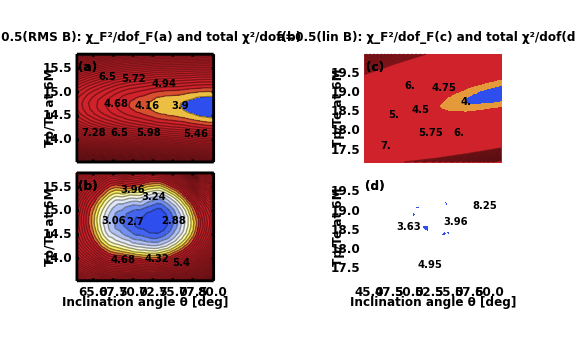

C:\study\accretion\! 2009 fall cfa\GR Polarized modeling\fitthFFLPCP.eps

```mathematica
Round[2418620.(4.9 10^-8)/Mean[{Exp[rhomin],Exp[rhomax]}]]
π/180(180-28.)
2 180/π 0.15
2.23054
```

#### the rest

```mathematica
imp=Partition[Import["E:\\mathematica\\analysis\\poliresa90th223fn-1cr_th.dat"],7];
len=Length[imp];
If[len==Round[par=Sqrt[len]]^2,impx=Transpose[Partition[imp,par],{3,2,1,4}]];mmord={1,1};
thmin=impx[[1,1,1,13]];thmax=impx[[1,-1,1,13]];rhomin=Log[impx[[1,1,1,12]]];rhomax=Log[impx[[1,1,-1,12]]];

tabb=Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu)^2]/7&/@Range[par];
lipFnu3=ListInterpolation[tabb,{{thmin,thmax},{rhomin,rhomax}},InterpolationOrder->mmord];(*for heat; for th in C++*)
tabb=1/12(Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu)^2]+Total[((tofit[[8;;9,5]]-impx[[-4;;-3,#,All,6]])/dCP)^2]+((Log[tofit[[5,3]]]-Log[impx[[-7,#,All,4]]])/dlogLP)^2+Total[((Log[tofit[[8;;9,3]]]-Log[impx[[-4;;-3,#,All,4]]])/dlogLP)^2])&/@Range[par];
lipFnuCPLP3=ListInterpolation[tabb,{{thmin,thmax},{rhomin,rhomax}},InterpolationOrder->mmord];
lcp=ContourPlot[lipFnu3[th,Log[10^-9 rhonor]],{th,thmin,thmax},{rhonor,10^9 Exp[rhomin],10^9 Exp[rhomax]},Contours->40,ContourLabels->(Text[Style[Framed[#3],15],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Inclination angle θ","Accretion rate in 10^-9Msun/year"},BaseStyle->{"Times",16},ImageSize->550,PlotRange->Automatic,ColorFunction->(ColorData["TemperatureMap"][2#+0.3]&)];
xcp=ContourPlot[lipFnuCPLP3[th,Log[10^-9 rhonor]],{th,thmin,thmax},{rhonor,10^9 Exp[rhomin],10^9 Exp[rhomax]},Contours->40,ContourLabels->(Text[Style[Framed[Round[10#3]/10.],15],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Inclination angle θ","Accretion rate in 10^-9Msun/year"},BaseStyle->{"Times",16},ImageSize->550,PlotRange->Automatic,ColorFunction->((ColorData["TemperatureMap"][#-1.])&),ColorFunctionScaling->False];
frac=0.06;sizy=10^9 frac(Exp[rhomax]-Exp[rhomin]);sizx=frac(thmax-thmin);
coords=xcp[[1,2,3,All,2]];
posit=Position[Table[ar=Delete[Abs[(coords[[#]]-coords[[nn]])/{sizx,sizy}&/@Range[Length[coords]]],nn];obst=False;For[kk=1,kk<nn,kk++,If[(ar[[kk,1]]<1)&&(ar[[kk,2]]<1),obst=True]];obst,{nn,Length[coords]-1}],True];
xcp[[1,2,3]]=Delete[xcp[[1,2,3]],posit];
lcp;
xcp
```

```mathematica
imp=Partition[Import["C:\\study\\mathematica\\3DMHD\\poliresa50th191fn-1cr_th.dat"],7];
len=Length[imp];
If[len==Round[par=Sqrt[len]]^2,impx=Transpose[Partition[imp,par],{3,2,1,4}]];mmord={1,1};
thmin=impx[[1,1,1,13]];thmax=impx[[1,-1,1,13]];rhomin=Log[impx[[1,1,1,12]]];rhomax=Log[impx[[1,1,-1,12]]];

tabb=Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu)^2]/7&/@Range[par];
lipFnu3=ListInterpolation[tabb,{{thmin,thmax},{rhomin,rhomax}},InterpolationOrder->mmord];(*for heat; for th in C++*)
tabb=1/12(Total[((tofit[[11-flen+1;;11,2]]-impx[[All,#,All,3]])/dFnu)^2]+Total[((tofit[[8;;9,5]]-impx[[-4;;-3,#,All,6]])/dCP)^2]+((Log[tofit[[5,3]]]-Log[impx[[-7,#,All,4]]])/dlogLP)^2+Total[((Log[tofit[[8;;9,3]]]-Log[impx[[-4;;-3,#,All,4]]])/dlogLP)^2])&/@Range[par];
lipFnuCPLP3=ListInterpolation[tabb,{{thmin,thmax},{rhomin,rhomax}},InterpolationOrder->mmord];
lcp=ContourPlot[lipFnu3[th,Log[10^-9 rhonor]],{th,thmin,thmax},{rhonor,10^9 Exp[rhomin],10^9 Exp[rhomax]},Contours->40,ContourLabels->(Text[Style[Framed[#3],15],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Inclination angle θ","Accretion rate in 10^-9Msun/year"},BaseStyle->{"Times",16},ImageSize->550,PlotRange->Automatic,ColorFunction->(ColorData["TemperatureMap"][2#+0.3]&)];
xcp=ContourPlot[lipFnuCPLP3[th,Log[10^-9 rhonor]],{th,thmin,thmax},{rhonor,10^9 Exp[rhomin],10^9 Exp[rhomax]},Contours->40,ContourLabels->(Text[Style[Framed[Round[10#3]/10.],15],{#1,#2},Background->White]&),Frame->True,FrameLabel->{"Inclination angle θ","Accretion rate in 10^-9Msun/year"},BaseStyle->{"Times",16},ImageSize->550,PlotRange->Automatic,ColorFunction->((ColorData["TemperatureMap"][#-1.])&),ColorFunctionScaling->False];
frac=0.06;sizy=10^9 frac(Exp[rhomax]-Exp[rhomin]);sizx=frac(thmax-thmin);
coords=xcp[[1,2,3,All,2]];
posit=Position[Table[ar=Delete[Abs[(coords[[#]]-coords[[nn]])/{sizx,sizy}&/@Range[Length[coords]]],nn];obst=False;For[kk=1,kk<nn,kk++,If[(ar[[kk,1]]<1)&&(ar[[kk,2]]<1),obst=True]];obst,{nn,Length[coords]-1}],True];
xcp[[1,2,3]]=Delete[xcp[[1,2,3]],posit];
lcp;
xcp
```

1600

```mathematica
Export["C:\\study\\mathematica\\3DMHD\\plot09_ch_cr.pdf",xcp]
Export["C:\\study\\mathematica\\3DMHD\\plot09_ch_cr.eps",xcp]
```

C:\study\mathematica\3DMHD\plot09_ch_cr.pdf

C:\study\mathematica\3DMHD\plot09_ch_cr.eps

### χ^2 analysis

#### linear analysis - all linear LP87, LP231, LP345, CP231, CP345

```mathematica
(*new data*)tofit={{8.450,0.6898,0,0,-0.2500},{14.90,0.9044,0,0,-0.6200},{22.50,1.070,0.1900,131.0,0},{43.00,1.159,0.5041,94.25,0},{87.73,1.841,1.42,-4.,0},{102.0,1.908,0,0,0},{145.0,2.275,0,0,0},{230.9,2.637,7.40,111.5,-1.200},{349.0,3.181,6.50,146.9,-1.500},{674.0,3.286,0,0,0},{857.0,2.867,0,0,0}};
 dFnu={1.,1.,1.,1.,0.080,0.1517,0.2644,0.1414,0.1205,0.3508,0.2404};dCP=0.30;dLP={0.5,0.66,0.61};
Clear[nh,co];ext=1.;acc=16;inord={2,2,2};poi3=50000;Off[NIntegrate::"maxp"];t=TimeUsed[];
(*SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3,AccuracyGoal->acc];*)SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3];
co=0;thlen=50;sptab={0.,0.5,0.7,0.9,0.98};narr=1.1;nF=7;nP=12;avg=False;
fmin=6950;fmax=9950;ind=11;sep=(fmax-fmin)/(ind-1);
Do[
(*gat=Transpose[Table[th=π/thlen(thn-.5);Import["C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\ava"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"in11"<>".dat"],{thn,thlen}],{2,1,3}];
flen=Position[gat[[1;;11,1]],gat[[1,1,1]]][[2,1]]-1;Off[InterpolatingFunction::"dmval",NIntegrate::"slwcon"];
gat=Partition[gat,flen];rholen=Length[Position[gat[[1;;30,1,1,6]],gat[[1,1,1,6]]]];gat=Partition[gat,rholen];dim=Dimensions[gat];hlen=dim[[1]];hmin=Log[gat[[-1,1,1,1,6]]];hmax=Log[gat[[1,1,1,1,6]]];
thmin=π/thlen(1-.5);thmax=π-thmin;rhomax=Log[gat[[1,-1,1,1,7]]/gat[[1,(flen+1)/2,1,1,7]]];
rateint=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];
raterho=ListInterpolation[Log[gat[[All,4,1,All,7]]],{{hmax,hmin},{thmin,thmax}}];
Do[flux[i]=gat[[All,All,i,All,2]];iflux[i][sp]=ListInterpolation[flux[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,flen}];
LP[1]=gat[[All,All,-7,All,3]];LP[2]=gat[[All,All,-4,All,3]];LP[3]=gat[[All,All,-3,All,3]];
CP[1]=gat[[All,All,-4,All,4]];CP[2]=gat[[All,All,-3,All,4]];*)


gaxx=Table[th=π/thlen(thn-.5);Import["C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\poliresa"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>"boo.dat"],{fnum,fmin,fmax,sep},{thn,thlen}];gat=Transpose[Total[gaxx,{1}]/ind,{2,1,3}];
flen=Position[gat[[1;;11,2]],gat[[1,1,2]]][[2,1]]-1;Off[InterpolatingFunction::"dmval",NIntegrate::"slwcon"];
gat=Partition[gat,flen];rholen=Length[Position[gat[[1;;30,1,1,6]],gat[[1,1,1,6]]]];
rholen=Length[Position[gat[[1;;30,1,1,8]],gat[[1,1,1,8]]]];
gat=Partition[gat,rholen];dim=Dimensions[gat];hlen=dim[[1]];hmin=Log[gat[[-1,1,1,1,8]]];hmax=Log[gat[[1,1,1,1,8]]];
thmin=π/thlen(1-.5);thmax=π-thmin;rhomax=Log[gat[[1,-1,1,1,9]]/gat[[1,(flen+1)/2,1,1,9]]];
rateint=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];
raterho=ListInterpolation[Log[gat[[All,4,1,All,9]]],{{hmax,hmin},{thmin,thmax}}];

Do[flux[i]=gat[[All,All,i,All,3]];iflux[i][sp]=ListInterpolation[flux[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,flen}];
LP[1]=gat[[All,All,-7,All,4]];LP[2]=gat[[All,All,-4,All,4]];LP[3]=gat[[All,All,-3,All,4]];
CP[1]=gat[[All,All,-4,All,6]];CP[2]=gat[[All,All,-3,All,6]];


Do[iCPx[i][sp]=ListInterpolation[CP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,2}];
Do[iLPx[i][sp]=ListInterpolation[LP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,3}];
lipFnux[sp]=Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2/(nF-3)];
lipFnuCPLPx[sp]=1/(nP-3)(Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2]+Total[(1/dCP(tofit[[8;;9,5]]-(iCPx[#][sp][heat,rhonor,θ]&/@Range[2])))^2]+((tofit[[5,3]]-(iLPx[1][sp][heat,rhonor,θ]))/dLP[[1]])^2+Total[((tofit[[8;;9,3]]-(iLPx[#][sp][heat,rhonor,θ]&/@{2,3}))/dLP[[2;;3]])^2]);
Fdistx=PDF[ChiSquareDistribution[nF-3],(nF-3) lipFnux[sp]]Sin[θ];
Ldistx=PDF[ChiSquareDistribution[nP-3],(nP-3) lipFnuCPLPx[sp]]Sin[θ];
PFnux=NIntegrate[Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];
PCPLPx=NIntegrate[Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];(*uncomment for computation of probability*)
prob[sp]={PFnux,PCPLPx};
Print[" sp=",sptab[[sp]],"; Probabilities: P(Fnu)=",PFnux,"; PCPLP=",PCPLPx];(*uncomment for computation of probability*)
resFLC[sp]=NMinimize[{lipFnuCPLPx[sp],(hmin<heat<hmax)&&(-rhomax<rhonor<rhomax)&&(thmin<θ<thmax)},{heat,rhonor,θ},Method->"DifferentialEvolution"];
Print["sp=",sptab[[sp]],"; min(χ^2)=",resFLC[sp][[1]]," for F_ν,LP,CP at  rhonor=",Exp[raterho[heat,θ]+rhonor]/.resFLC[sp][[2]],"; heat=",Exp[heat]/.resFLC[sp][[2]],";  θ=",θ/.resFLC[sp][[2]]];
resF[sp]=NMinimize[{lipFnux[sp],(hmin<heat<hmax)&&(-rhomax<rhonor<rhomax)&&(thmin<θ<thmax)},{heat,rhonor,θ},Method->"DifferentialEvolution"];
Print["sp=",sptab[[sp]],"; min(χ^2)=",resF[sp][[1]]," for F_νat  rhonor=",Exp[raterho[heat,θ]+rhonor]/.resF[sp][[2]],"; heat=",Exp[heat]/.resF[sp][[2]],";  θ=",θ/.resF[sp][[2]]];
If[avg,hmean=Exp[1/PFnux NIntegrate[heat Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
rhomean=Re[Exp[1/PFnux NIntegrate[(rateint[heat,θ]+rhonor)Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
θmean=Re[1/PFnux NIntegrate[θ Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
Print["Over Fnu fits:  <h> = ",hmean,";  <Mdot> = ",rhomean,";  <θ>=",θmean];
hmean=Re[Exp[1/PCPLPx NIntegrate[heat Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
θmean=Re[1/PCPLPx NIntegrate[θ Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
rhomean=Re[Exp[1/PCPLPx NIntegrate[(rateint[heat,θ]+rhonor)Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
Print["Over FnuCPLP fits:  <h> = ",hmean,";  <Mdot> = ",rhomean,";  <θ>=",θmean]],{sp,1,5}];
Print["Computed in ",Round[TimeUsed[]-t]," seconds"]
```

{4.48, 2.09, 3.31, 3.91, 3.71} - random exploration
0.00 4.4831 0.7358 0.41680 1051247.91196 7.608e-08
0.50 2.0956 2.0304 0.38473 924988.66162 2.713e-08
0.70 3.3066 2.1546 0.31866 1097040.00000 3.713e-08
0.90 3.9064 2.1426 0.40969 647457.34623 1.015e-08
0.98 3.7110 2.1139 0.40783 414295.83116 1.733e-08

```mathematica
180/π(π-{2.0304,2.1546,2.1426,2.1139})
180/π 0.7358(*spin 0*)
```

```mathematica
resFLC[2][[2]]
```

```mathematica
(*determine flow parameters*)
sp=2;rhonor=(rhonor/.resFLC[sp][[2]]);heat=(Exp[heat/.resFLC[sp][[2]]]);
atab={0.,0.5,0.7,0.9,0.98};sptab={"0","05","07","09","098"};
nmtab={8,8,8,9,9};ncuttab={145,147,149,153,162};a=atab[[sp]];nm=nmtab[[sp]];ncut=ncuttab[[sp]];
xx=Import["C:\\study\\mathematica\\!GRMHD\\a"<>sptab[[sp]]<>"\\Tsmap"<>sptab[[sp]]<>".dat"];
rhoout=130;rmax=3.4 10^5;rcut=xx[[ncut,1]];
rhopo=-Log[rhoout/rhonor/xx[[ncut]][[3]]]/Log[rmax/rcut];
rhocon=rhonor*xx[[ncut,3]];
Ucon=xx[[ncut,2]];ruru={rg->(2 6.67 10^-8 4.5 10^6 2 10^33)/((3 10^10)^2),arcsec->(2 π 8.4 10^3 3.08 10^18)/(360 60 60),pc->3.08 10^18,year->365.35 86400,cc->3. 10^10,Msun->2. 10^33,mp->1.67 10^-24,me->9.1 10^-28,kb->1.38 10^-16,h->6.626 10^-27,ee->4.8 10^-10,keV->1000 1.602 10^-12};
rategs=4.5 10^-8 Msun/year/.ruru;
rtab=xx[[All,1]];rntab=Table[rcut(rcut/rmax)^(-i/100),{i,100}];ρfun=rhocon(r/rcut)^-rhopo;
vrvr=-rategs/(2 cc mp rg^2 r^2 ρinter)/.ruru;dcap=(2.-0.49/((0.7+ cser^2)^2));Tsfun=Ucon(r/rcut)^-0.98;Tstab=xx[[1;;ncut,1;;2]];
Tsinter=Interpolation[Join[Tstab,Transpose[{rntab,Tsfun/.r->#&/@rntab}]]][r];
sysm={tail=(Dts=D[Tsinter,r];νc=8.9 10^-11(Te[r]/(3 10^10))^(-3/2)ρfun/10^7)(2 mp rg^3 r^2 ρfun)/rategs(Tp[r]-Te[r])+2(((√Tp[r])/(√Tp[r]+heat √Te[r]))-1/dcap(1(heat √Te[r])/(√Tp[r]+heat √Te[r])))Dts;Te'[r]==(2Dts-tail)/(dcap+1),Tp'[r]==tail+(2Dts-tail)/(dcap+1)}/.{θe->(kb Te[r])/(me cc^2),cser->√((kb Te[r])/(me cc^2)),cspr->√((kb Tp[r])/(mp cc^2))}/.ruru;
Off[FindRoot::"lstol"];tosol=Flatten[{sysm,{Tp[r]==Tsinter,Te[r]==Tsinter}/.r->rmax}];
solnew=NDSolve[tosol,{Tp,Te},{r,rtab[[1]],rmax}][[1]];
Print["Ṁ=",N[Floor[Exp[rateint[heat,θ]+rhonor]/.resFLC[sp][[2]],10^-10]]," Msun/yr;  θ=",Floor[180/π(π-θ)/.resFLC[sp][[2]],0.1],"°;  Tp/Te=", Floor[Tp[6]/Te[6]/.solnew,0.1]," at 6M; Te[6M]=",N[Floor[Te[6]/.solnew,10^8]]]
Clear[sp,co,rhonor,heat];
```

```mathematica
Do[Ftab=iflux[#][sp][heat,rhonor,θ]&/@Range[7]/.resFLC[sp][[2]];
CPtab=iCPx[#][sp][heat,rhonor,θ]&/@Range[2]/.resFLC[sp][[2]];
LPtab=iLPx[#][sp][heat,rhonor,θ]&/@Range[3]/.resFLC[sp][[2]];
Print[sp," ⇒ ",{Ftab,CPtab,LPtab}],{sp,1,5}]
```

```mathematica
inord->{2,2,2}
```

```mathematica
inord->{1,1,1}
```

```mathematica
dir="C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\";
fmin=6950;fmax=9950;ind=11;sep=(fmax-fmin)/(ind-1);sp=2;thlen=50;sptab={0.,0.5,0.7,0.9,0.98};dir="C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\";th=π/thlen(thn-.5)/.thn->33;
tata=Table[gat=Import[dir<>"poliresa"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>"boo.dat"];
Partition[Partition[gat,7],7][[17,4]],{fnum,fmin,fmax,sep}]
sp=.;
```

```mathematica
tata[[All,All,3]]
tata[[All,1,4]](*LP88*)
tata[[All,4,4]](*LP230*)
tata[[All,5,4]](*LP345*)
tata[[All,4,6]](*CP230*)
tata[[All,5,6]](*CP345*)
```

```mathematica
(*averaging:*)
fmin=6950;fmax=9950;ind=11;sep=(fmax-fmin)/(ind-1);thlen=50;sptab={0.,0.5,0.7,0.9,0.98};dir="C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\";
{Dynamic[sp],Dynamic[thn]}
Do[gat=Table[th=π/thlen(thn-.5);Import[dir<>"poliresa"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>"boo.dat"],{fnum,fmin,fmax,sep}];
roro=Round[Delete[Transpose[Total[gat]/ind],{{1},{7},{10},{11},{12},{13}}],0.001];
tot=Join[ToExpression[ToString[roro[[1;;6]]]],{roro[[7]]}];
Export[dir<>"ava"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"in"<>ToString[ind]<>".dat",Transpose[Join[tot[[1;;3]],Reverse[tot[[4;;5]]],tot[[6;;7]]]]],{sp,1,5},{thn,thlen}]
```

```mathematica
π/thlen(thn-.5)/.{thn->33,thlen->50}(*9,37 - spin 0*)
```

#### x analysis - no LP87, only LP231, LP345, CP231, CP345

```mathematica
tofit={{8.450,0.6898,0,0,-0.2500},{14.90,0.9044,0,0,-0.6200},{22.50,1.070,0.1900,131.0,0},{43.00,1.159,0.5041,94.25,0},{87.73,1.841,1.42,-4.,0},{102.0,1.908,0,0,0},{145.0,2.275,0,0,0},{230.9,2.637,7.40,111.5,-1.200},{349.0,3.181,6.50,146.9,-1.500},{674.0,3.286,0,0,0},{857.0,2.867,0,0,0}};
 dFnu={1.,1.,1.,1.,0.080,0.1517,0.2644,0.1414,0.1205,0.3508,0.2404};dCP=0.30;dLP={0.5,0.66,0.61};
Clear[nh,co];ext=1.;acc=16;inord={2,2,2};poi3=50000;Off[NIntegrate::"maxp"];t=TimeUsed[];
(*SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3,AccuracyGoal->acc];*)SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3];
co=0;thlen=50;sptab={0.,0.5,0.7,0.9,0.98};narr=1.1;nF=7;nP=11;avg=False;
fmin=6950;fmax=9950;ind=11;sep=(fmax-fmin)/(ind-1);
Do[
(*gat=Transpose[Table[th=π/thlen(thn-.5);Import["C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\ava"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"in11"<>".dat"],{thn,thlen}],{2,1,3}];
flen=Position[gat[[1;;11,1]],gat[[1,1,1]]][[2,1]]-1;Off[InterpolatingFunction::"dmval",NIntegrate::"slwcon"];
gat=Partition[gat,flen];rholen=Length[Position[gat[[1;;30,1,1,6]],gat[[1,1,1,6]]]];gat=Partition[gat,rholen];dim=Dimensions[gat];hlen=dim[[1]];hmin=Log[gat[[-1,1,1,1,6]]];hmax=Log[gat[[1,1,1,1,6]]];
thmin=π/thlen(1-.5);thmax=π-thmin;rhomax=Log[gat[[1,-1,1,1,7]]/gat[[1,(flen+1)/2,1,1,7]]];
rateint=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];
raterho=ListInterpolation[Log[gat[[All,4,1,All,7]]],{{hmax,hmin},{thmin,thmax}}];
Do[flux[i]=gat[[All,All,i,All,2]];iflux[i][sp]=ListInterpolation[flux[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,flen}];
LP[1]=gat[[All,All,-7,All,3]];LP[2]=gat[[All,All,-4,All,3]];LP[3]=gat[[All,All,-3,All,3]];
CP[1]=gat[[All,All,-4,All,4]];CP[2]=gat[[All,All,-3,All,4]];*)

gaxx=Table[th=π/thlen(thn-.5);Import["C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\poliresa"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>"boo.dat"],{fnum,fmin,fmax,sep},{thn,thlen}];gat=Transpose[Total[gaxx,{1}]/ind,{2,1,3}];
flen=Position[gat[[1;;11,2]],gat[[1,1,2]]][[2,1]]-1;Off[InterpolatingFunction::"dmval",NIntegrate::"slwcon"];
gat=Partition[gat,flen];rholen=Length[Position[gat[[1;;30,1,1,6]],gat[[1,1,1,6]]]];
rholen=Length[Position[gat[[1;;30,1,1,8]],gat[[1,1,1,8]]]];
gat=Partition[gat,rholen];dim=Dimensions[gat];hlen=dim[[1]];hmin=Log[gat[[-1,1,1,1,8]]];hmax=Log[gat[[1,1,1,1,8]]];
thmin=π/thlen(1-.5);thmax=π-thmin;rhomax=Log[gat[[1,-1,1,1,9]]/gat[[1,(flen+1)/2,1,1,9]]];
rateint=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];
raterho=ListInterpolation[Log[gat[[All,4,1,All,9]]],{{hmax,hmin},{thmin,thmax}}];

Do[flux[i]=gat[[All,All,i,All,3]];iflux[i][sp]=ListInterpolation[flux[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,flen}];
LP[1]=gat[[All,All,-7,All,4]];LP[2]=gat[[All,All,-4,All,4]];LP[3]=gat[[All,All,-3,All,4]];
CP[1]=gat[[All,All,-4,All,6]];CP[2]=gat[[All,All,-3,All,6]];


Do[iCPx[i][sp]=ListInterpolation[CP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,2}];
Do[iLPx[i][sp]=ListInterpolation[LP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,3}];
lipFnux[sp]=Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2/(nF-3)];
lipFnuCPLPx[sp]=1/(nP-3)(Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2]+Total[(1/dCP(tofit[[8;;9,5]]-(iCPx[#][sp][heat,rhonor,θ]&/@Range[2])))^2]+Total[((tofit[[8;;9,3]]-(iLPx[#][sp][heat,rhonor,θ]&/@{2,3}))/dLP[[2;;3]])^2]);
Fdistx=PDF[ChiSquareDistribution[nF-3],(nF-3) lipFnux[sp]]Sin[θ];
Ldistx=PDF[ChiSquareDistribution[nP-3],(nP-3) lipFnuCPLPx[sp]]Sin[θ];
(*hmin=Log[0.25];*)
PFnux=NIntegrate[Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];
PCPLPx=NIntegrate[Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];
prob[sp]={PFnux,PCPLPx};
(*Print[PCPLPz=NIntegrate[Exp[-lipFnuCPLPx[sp]^2/2]Sin[θ],{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];*)
Print[" sp=",sptab[[sp]],"; Probabilities: P(Fnu)=",PFnux,"; PCPLP=",PCPLPx];
resFLC[sp]=NMinimize[{lipFnuCPLPx[sp],(hmin<heat<hmax)&&(-rhomax<rhonor<rhomax)&&(thmin<θ<thmax)},{heat,rhonor,θ},Method->"DifferentialEvolution"];
Print["sp=",sptab[[sp]],"; min(χ^2)=",resFLC[sp][[1]]," for F_ν,LP,CP at  rhonor=",Exp[raterho[heat,θ]+rhonor]/.resFLC[sp][[2]],"; heat=",Exp[heat]/.resFLC[sp][[2]],";  θ=",θ/.resFLC[sp][[2]]];
resF[sp]=NMinimize[{lipFnux[sp],(hmin<heat<hmax)&&(-rhomax<rhonor<rhomax)&&(thmin<θ<thmax)},{heat,rhonor,θ},Method->"DifferentialEvolution"];
Print["sp=",sptab[[sp]],"; min(χ^2)=",resF[sp][[1]]," for F_νat  rhonor=",Exp[raterho[heat,θ]+rhonor]/.resF[sp][[2]],"; heat=",Exp[heat]/.resF[sp][[2]],";  θ=",θ/.resF[sp][[2]]];
If[avg,hmean=Exp[1/PFnux NIntegrate[heat Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
rhomean=Re[Exp[1/PFnux NIntegrate[(rateint[heat,θ]+rhonor)Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
θmean=Re[1/PFnux NIntegrate[θ Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
Print["Over Fnu fits:  <h> = ",hmean,";  <Mdot> = ",rhomean,";  <θ>=",θmean];
hmean=Re[Exp[1/PCPLPx NIntegrate[heat Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
θmean=Re[1/PCPLPx NIntegrate[θ Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
rhomean=Re[Exp[1/PCPLPx NIntegrate[(rateint[heat,θ]+rhonor)Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
Print["Over FnuCPLP fits:  <h> = ",hmean,";  <Mdot> = ",rhomean,";  <θ>=",θmean]],{sp,1,5}];
Print["Computed in ",Round[TimeUsed[]-t]," seconds"]
```

```mathematica
resF[4]
```

```mathematica
sp=5;Ftab=iflux[#][sp][heat,rhonor,θ]&/@Range[7]/.resFLC[sp][[2]];
CPtab=iCPx[#][sp][heat,rhonor,θ]&/@Range[2]/.resFLC[sp][[2]];
LPtab=Exp[iLPx[#][sp][heat,rhonor,θ]]&/@Range[2]/.resFLC[sp][[2]];
{Ftab,CPtab,LPtab}
sp=.;
```

```mathematica
sp=4;Ftab=iflux[#][sp][heat,rhonor,θ]&/@Range[7]/.resFLC[sp][[2]];
CPtab=iCPx[#][sp][heat,rhonor,θ]&/@Range[2]/.resFLC[sp][[2]];
LPtab=Exp[iLPx[#][sp][heat,rhonor,θ]]&/@Range[2]/.resFLC[sp][[2]];
{Ftab,CPtab,LPtab}
sp=.;
```

```mathematica
inverse B
```

```mathematica
direct B
```

```mathematica
el={ListLogLogPlot,ListLogLinearPlot};Clear[totI];xcol=Cyan;myf=14;siz=580;ord=1;
SetOptions[#,Frame->True,BaseStyle->{(*FontFamily->"Arial",*)FontWeight->"Bold",FontSize->myf},PlotStyle->AbsoluteThickness[2.5],FrameStyle->AbsoluteThickness[2.5],FrameTicks->{{Automatic,None},{(*{10,20,50,100,200,500}*){43,88,145,231,349,690},None}}]&/@el;
ax=30;Fran={{40,900},{0.8,3.7}};LPran={{40,860},{0.4,24.}};CPran={{40,860},{-2.,2.2}};angran={{80,860},{80,170}};
imp=Import["E:\\mathematica\\3DMHD\\quicka90in11x.dat"];
imp=Partition[imp,7];
plo[nn_?IntegerQ,style_?ListQ,ax_?NumberQ]:=(fff=Transpose[imp[[nn]]];ftab=fff[[1]];Fnusim=Transpose[{ftab,fff[[2]]}];LPnusim=Transpose[{ftab,fff[[3]]}];CPnusim=Transpose[{ftab,fff[[4]]}];angsim=Delete[Transpose[{ftab,ax+fff[[5]]}],1];
{ListLogLogPlot[Fnusim,Joined->True,PlotRange->Fran,Frame->True,FrameLabel->{{Null,Null},{Null,"F_ν [Jy]"}},ImageSize->siz,
PlotStyle->style],ListLogLogPlot[LPnusim,Joined->True,InterpolationOrder->ord,Frame->True,PlotRange->LPran,FrameLabel->{{Null,Null},{Null,"LP [%]"}},ImageSize->siz,PlotStyle->style],ListLogLinearPlot[CPnusim,Joined->True,InterpolationOrder->ord,Frame->True,FrameLabel->{{Null,Null},{Null,"CP [%]"}},PlotRange->CPran,ImageSize->siz,PlotStyle->style],ListLogLinearPlot[angsim,Joined->True,Frame->True,ImageSize->siz,PlotRange->angran,FrameLabel->{{Null,Null},{Null,"Electric vector position angle [deg]"}},PlotStyle->style]});
```

```mathematica
Graphics[{RGBColor[0,1,0],Disk[]}]
```

```mathematica
tab=Table[plo[i,{AbsoluteThickness[1],RGBColor[0,i/15,1-i/15]},30],{i,15}];
Show[Transpose[tab][[1]]]
Show[Transpose[tab][[2]]]
Show[Transpose[tab][[3]]]
Show[Transpose[tab][[4]]]
```

```mathematica
inverse B
```

```mathematica
direct B
```

#### best analysis - interpolating all the quantities

```mathematica
tofit={{8.450,0.6898,0,0,-0.2500},{14.90,0.9044,0,0,-0.6200},{22.50,1.070,0.1900,131.0,0},{43.00,1.159,0.5041,94.25,0},{87.73,1.841,1.026,-4.,0},{102.0,1.908,0,0,0},{145.0,2.275,0,0,0},{230.9,2.637,7.015,111.5,-1.200},{349.0,3.181,6.143,146.9,-1.500},{674.0,3.286,0,0,0},{857.0,2.867,0,0,0}};tofit[[5,3]]=2.;
(*8.45 - 43GHz - still old data*)
 dFnu={1.,1.,1.,1.,0.080,0.1517,0.2644,0.1414,0.1205,0.3508,0.2404};dCP=0.30;dlogLP={0.19,0.086,0.115};t=TimeUsed[];

Clear[nh,co];ext=1.;acc=16;inord={2,2,2};poi3=50000;Off[NIntegrate::"maxp"];
(*SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3,AccuracyGoal->acc];*)SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3];
co=0;thlen=50;sptab={0.,0.5,0.7,0.9,0.98};narr=1.1;nF=7;nP=12;avg=False;
Do[
gat=Transpose[Table[th=π/thlen(thn-.5);Import["E:\\mathematica\\3DMHD\\ava"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"in11"<>".dat"],{thn,thlen}],{2,1,3}];
flen=Position[gat[[1;;11,1]],gat[[1,1,1]]][[2,1]]-1;Off[InterpolatingFunction::"dmval",NIntegrate::"slwcon"];
gat=Partition[gat,flen];rholen=Length[Position[gat[[1;;30,1,1,6]],gat[[1,1,1,6]]]];gat=Partition[gat,rholen];dim=Dimensions[gat];hlen=dim[[1]];hmin=Log[gat[[-1,1,1,1,6]]];hmax=Log[gat[[1,1,1,1,6]]];
thmin=π/thlen(1-.5);thmax=π-thmin;rhomax=Log[gat[[1,-1,1,1,7]]/gat[[1,(flen+1)/2,1,1,7]]];
(*rateint=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];*)
raterho=ListInterpolation[Log[gat[[All,4,1,All,7]]],{{hmax,hmin},{thmin,thmax}}];
Do[flux[i]=gat[[All,All,i,All,2]];iflux[i][sp]=ListInterpolation[flux[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,flen}];
LP[1]=Log[gat[[All,All,-7,All,3]]];LP[2]=Log[gat[[All,All,-4,All,3]]];LP[3]=Log[gat[[All,All,-3,All,3]]];
CP[1]=gat[[All,All,-4,All,4]];CP[2]=gat[[All,All,-3,All,4]];
Do[iCPx[i][sp]=ListInterpolation[CP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,2}];
Do[iLPx[i][sp]=ListInterpolation[LP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,3}];
lipFnux[sp]=Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2/(nF-3)];
lipFnuCPLPx[sp]=1/(nP-3)(Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2]+Total[(1/dCP(tofit[[8;;9,5]]-(iCPx[#][sp][heat,rhonor,θ]&/@Range[2])))^2]+((Log[tofit[[5,3]]]-(iLPx[1][sp][heat,rhonor,θ]))/dlogLP[[1]])^2+Total[((Log[tofit[[8;;9,3]]]-(iLPx[#][sp][heat,rhonor,θ]&/@{2,3}))/dlogLP[[2;;3]])^2]);
Fdistx=PDF[ChiSquareDistribution[nF-3],(nF-3) lipFnux[sp]]Sin[θ];
Ldistx=PDF[ChiSquareDistribution[nP-3],(nP-3) lipFnuCPLPx[sp]]Sin[θ];
(*hmin=Log[0.25];*)
PFnux=NIntegrate[Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];
PCPLPx=NIntegrate[Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];
prob[sp]={PFnux,PCPLPx};
(*Print[PCPLPz=NIntegrate[Exp[-lipFnuCPLPx[sp]^2/2]Sin[θ],{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];*)
Print[" sp=",sptab[[sp]],"; Probabilities: P(Fnu)=",PFnux,"; PCPLP=",PCPLPx];
resFLC[sp]=NMinimize[{lipFnuCPLPx[sp],(hmin<heat<hmax)&&(-rhomax<rhonor<rhomax)&&(thmin<θ<thmax)},{heat,rhonor,θ},Method->"DifferentialEvolution"];
Print["sp=",sptab[[sp]],"; min(χ^2)=",resFLC[sp][[1]]," for F_ν,LP,CP at  rhonor=",Exp[raterho[heat,θ]+rhonor]/.resFLC[sp][[2]],"; heat=",Exp[heat]/.resFLC[sp][[2]],";  θ=",θ/.resFLC[sp][[2]]];
resF[sp]=NMinimize[{lipFnux[sp],(hmin<heat<hmax)&&(-rhomax<rhonor<rhomax)&&(thmin<θ<thmax)},{heat,rhonor,θ},Method->"DifferentialEvolution"];
Print["sp=",sptab[[sp]],"; min(χ^2)=",resF[sp][[1]]," for F_νat  rhonor=",Exp[raterho[heat,θ]+rhonor]/.resF[sp][[2]],"; heat=",Exp[heat]/.resF[sp][[2]],";  θ=",θ/.resF[sp][[2]]];
If[avg,hmean=Exp[1/PFnux NIntegrate[heat Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
rhomean=Re[Exp[1/PFnux NIntegrate[(rateint[heat,θ]+rhonor)Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
θmean=Re[1/PFnux NIntegrate[θ Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
Print["Over Fnu fits:  <h> = ",hmean,";  <Mdot> = ",rhomean,";  <θ>=",θmean];
hmean=Re[Exp[1/PCPLPx NIntegrate[heat Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
θmean=Re[1/PCPLPx NIntegrate[θ Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
rhomean=Re[Exp[1/PCPLPx NIntegrate[(rateint[heat,θ]+rhonor)Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
Print["Over FnuCPLP fits:  <h> = ",hmean,";  <Mdot> = ",rhomean,";  <θ>=",θmean]],{sp,4,4}];
Print["Computed in ",Round[TimeUsed[]-t]," seconds"]
```

```mathematica
LP87=2% ;
```

```mathematica
inv
```

```mathematica
50000,{2,2,2}
```

```mathematica
50000,{1,1,2}
```

```mathematica
50000,{1,2,1}
```

```mathematica
50000,{2,1,1}
```

```mathematica
50000,{1,1,1}
```

```mathematica
all boosted
```

```mathematica
all non-boosted
```

```mathematica
sp=4;resFLC[sp,co]=NMinimize[{lipFnuCPLPx[4],(0.1+hmin<heat<hmax)&&(-rhomax<rhonor<rhomax)&&(2.0<θ<2.6)},{heat,rhonor,θ},Method->"DifferentialEvolution"];
Print["sp=",sptab[[sp]],"; min(χ^2)=",resFLC[sp,co][[1]]," for F_ν,LP,CP at  rhonor=",Exp[raterho[heat,θ]+rhonor]/.resFLC[sp,co][[2]],"; heat=",Exp[heat]/.resFLC[sp,co][[2]],";  θ=",θ/.resFLC[sp,co][[2]]];
sp=.;
```

```mathematica
0.9, boosted, 0-7
```

```mathematica
0.5, non-boosted
```

```mathematica
0.9, boosted
```

```mathematica
0.5, boosted
```

```mathematica
sp=4;co=0;resFLC[sp,co]=NMinimize[{lipFnuCPLPx[sp],(hmin<heat<hmax)&&(-rhomax<rhonor<rhomax)&&(thmin<θ<thmax)},{heat,rhonor,θ},Method->"RandomSearch"];
Print["sp=",sptab[[sp]],"; min(χ^2)=",resFLC[sp,co][[1]]," for F_ν,LP,CP at  rhonor=",Exp[raterho[heat,θ]+rhonor]/.resFLC[sp,co][[2]],"; heat=",Exp[heat]/.resFLC[sp,co][[2]],";  θ=",θ/.resFLC[sp,co][[2]]];
sp=.;
```

```mathematica
sp=4;heat=Log[0.2];co=0;resFLC[sp,co]=NMinimize[{lipFnuCPLPx[sp],(-rhomax<rhonor<rhomax)&&(thmin<θ<thmax)},{rhonor,θ},Method->"RandomSearch"];
Print["sp=",sptab[[sp]],"; min(χ^2)=",resFLC[sp,co][[1]]," for F_ν,LP,CP at  rhonor=",Exp[raterho[heat,θ]+rhonor]/.resFLC[sp,co][[2]],"; heat=",Exp[heat]/.resFLC[sp,co][[2]],";  θ=",θ/.resFLC[sp,co][[2]]];
sp=.;heat=.;
```

```mathematica
(*determine flow parameters*)
sp=4;co=0;rhonor=(rhonor/.resFLC[sp,co][[2]]);heat=(Exp[heat/.resFLC[sp,co][[2]]]);
atab={0.,0.5,0.7,0.9,0.98};sptab={"0","05","07","09","098"};
nmtab={8,8,8,9,9};ncuttab={145,147,149,153,162};a=atab[[sp]];nm=nmtab[[sp]];ncut=ncuttab[[sp]];
xx=Import["C:\\study\\mathematica\\3DMHD\\Tsmap"<>sptab[[sp]]<>".dat"];
rhoout=130;rmax=3.4 10^5;rcut=xx[[ncut,1]];
rhopo=-Log[rhoout/rhonor/xx[[ncut]][[3]]]/Log[rmax/rcut];
rhocon=rhonor*xx[[ncut,3]];
Ucon=xx[[ncut,2]];ruru={rg->(2 6.67 10^-8 4.5 10^6 2 10^33)/((3 10^10)^2),arcsec->(2 π 8.4 10^3 3.08 10^18)/(360 60 60),pc->3.08 10^18,year->365.35 86400,cc->3. 10^10,Msun->2. 10^33,mp->1.67 10^-24,me->9.1 10^-28,kb->1.38 10^-16,h->6.626 10^-27,ee->4.8 10^-10,keV->1000 1.602 10^-12};
rategs=1.5 10^-8 Msun/year/.ruru;
rtab=xx[[All,1]];rntab=Table[rcut(rcut/rmax)^(-i/100),{i,100}];ρfun=rhocon(r/rcut)^-rhopo;
vrvr=-rategs/(2 cc mp rg^2 r^2 ρinter)/.ruru;dcap=(2.-0.49/((0.7+ cser^2)^2));Tsfun=Ucon(r/rcut)^-0.98;Tstab=xx[[1;;ncut,1;;2]];
Tsinter=Interpolation[Join[Tstab,Transpose[{rntab,Tsfun/.r->#&/@rntab}]]][r];
sysm={tail=(Dts=D[Tsinter,r];νc=8.9 10^-11(Te[r]/(3 10^10))^(-3/2)ρfun/10^7)(2 mp rg^3 r^2 ρfun)/rategs(Tp[r]-Te[r])+2(((√Tp[r])/(√Tp[r]+heat √Te[r]))-1/dcap(1(heat √Te[r])/(√Tp[r]+heat √Te[r])))Dts;Te'[r]==(2Dts-tail)/(dcap+1),Tp'[r]==tail+(2Dts-tail)/(dcap+1)}/.{θe->(kb Te[r])/(me cc^2),cser->√((kb Te[r])/(me cc^2)),cspr->√((kb Tp[r])/(mp cc^2))}/.ruru;
Off[FindRoot::"lstol"];tosol=Flatten[{sysm,{Tp[r]==Tsinter,Te[r]==Tsinter}/.r->rmax}];
solnew=NDSolve[tosol,{Tp,Te},{r,rtab[[1]],rmax}][[1]];
Print["Ṁ=",N[Floor[Exp[rateint[heat,θ]+rhonor]/.resFLC[sp,co][[2]],10^-10]]," Msun/yr;  θ=",Floor[180/π(π-θ)/.resFLC[sp,co][[2]],0.1],"°;  Tp/Te=", Floor[Tp[6]/Te[6]/.solnew,0.1]," at 6M; Te[6M]=",N[Floor[Te[6]/.solnew,10^8]]]
Clear[sp,co,rhonor,heat];
```

```mathematica
chisqF=Table[resF[i,0][[1]],{i,5}]
chisqFLC=Table[resFLC[i,0][[1]],{i,5}]
chisq05F=Table[resF[2,i][[1]],{i,7}](*boosted*)
chisq05FLC=Table[resFLC[2,i][[1]],{i,7}](*boosted*)
```

```mathematica
(*"NelderMead", "DifferentialEvolution", "SimulatedAnnealing" and "RandomSearch". *)
```

```mathematica
chisqFboo={3.6116494688826073,1.7118581693296315,0.10203485802123645,0.040861451912052954,0.03130335960552725};
chisqFnob={4.749449410553588,1.6719417953699511,0.2038945607375132,0.0581573074416609,0.06058174038749031};
chisqFLCboo={6.77409384860362,1.923488888795368,4.026577188368991,3.03696414000554,3.6365119314749563};
chisqFLCnob={4.908819933436118,2.219704563759286,5.090257542045821,3.0241934681053935,10.105163241573656};
chisq05F={1.7306671186587128,0.9479766404071468,2.7880501281067986,2.217177805817168,2.076373378889102,0.543301748308009,1.2680030887729172};
chisq05FLC={2.202065090891869,4.312903912784133,4.368991649788537,2.9197686580331124,2.2803997926233883,1.5108312899428729,2.875748393748631};
```

```mathematica
various co  sp->0.5; boosted->True
```

```mathematica
boosted->True
```

co=0 sp=0.; Probabilities: P(Fnu)=1.69054×10^-6; PCPLP=0.
sp=0.; min(χ^2)=6.77409 for F_ν,LP,CP at  rhonor=792833.; heat=0.439559;  θ=2.10488
sp=0.; min(χ^2)=3.61165 for F_νat  rhonor=477456.; heat=0.57474;  θ=1.5054
co=0 sp=0.5; Probabilities: P(Fnu)=0.00112484; PCPLP=0.0000237955
sp=0.5; min(χ^2)=1.92349 for F_ν,LP,CP at  rhonor=300090.; heat=0.443782;  θ=1.86109
sp=0.5; min(χ^2)=1.71186 for F_νat  rhonor=249196.; heat=0.484702;  θ=1.54965
co=0 sp=0.7; Probabilities: P(Fnu)=0.0175982; PCPLP=2.59823×10^-9
sp=0.7; min(χ^2)=4.02658 for F_ν,LP,CP at  rhonor=462221.; heat=0.470756;  θ=2.04975
sp=0.7; min(χ^2)=0.102035 for F_νat  rhonor=1.30501×10^6; heat=0.276297;  θ=2.39152
co=0 sp=0.9; Probabilities: P(Fnu)=0.00716632; PCPLP=1.29421×10^-6
sp=0.9; min(χ^2)=3.03696 for F_ν,LP,CP at  rhonor=527561.; heat=0.413561;  θ=2.23054
sp=0.9; min(χ^2)=0.0408615 for F_νat  rhonor=1.55622×10^6; heat=0.235789;  θ=2.85625
co=0 sp=0.98; Probabilities: P(Fnu)=0.00876943; PCPLP=4.04138×10^-7
sp=0.98; min(χ^2)=3.63651 for F_ν,LP,CP at  rhonor=304073.; heat=0.423505;  θ=2.20845
sp=0.98; min(χ^2)=0.0313034 for F_νat  rhonor=837925.; heat=0.252411;  θ=0.350239
Computed in 262 seconds

```mathematica
boosted->False
```

```mathematica
chisq[fi_?ListQ]:=(1/(flen+5)(Total[((tofit[[11-flen+1;;11,2]]-(fi[[#,3]]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2]+Total[((tofit[[8;;9,5]]-(fi[[#,6]]&/@{4,5}))/dCP)^2]+((Log[tofit[[5,3]]]-(Log[fi[[1,4]]]))/dlogLP[[1]])^2+Total[((Log[tofit[[8;;9,3]]]-(Log[fi[[#,4]]]&/@{4,5}))/dlogLP[[2;;3]])^2]));
chisq[Import["E:\\mathematica\\analysis\\poliresa50th186fn-1boo.dat"]]
chisq[Import["E:\\mathematica\\analysis\\poliresa50th186fn-1boox.dat"]]
```

```mathematica
Do[res[sp]=NMinimize[{lipFnuCPLPx[sp],(hmin<heat<hmax)&&(-rhomax<rhonor<rhomax)&&(thmin<θ<thmax)},{heat,rhonor,θ},Method->"RandomSearch"];
Print["sp=",sptab[[sp]],"; min(χ^2)=",res[sp][[1]],"  at  rhonor=",Exp[raterho[heat,θ]+rhonor]/.res[sp][[2]],"; heat=",Exp[heat]/.res[sp][[2]],";  θ=",θ/.res[sp][[2]]],{sp,2,2}]
```

```mathematica
sp=2;Fnures[sp]=Table[iflux[i][sp][heat,rhonor,θ]/.res[sp][[2]],{i,7}]
CPres[sp]=Table[iCPx[i][sp][heat,rhonor,θ]/.res[sp][[2]],{i,2}]
LPres[sp]=Exp[Table[iLPx[i][sp][heat,rhonor,θ]/.res[sp][[2]],{i,3}]]
sp=.;
```

#### etc + convergence

```mathematica
acc=7;inord={2,2,2};poi3=20000;Off[NIntegrate::"maxp"];sp=3;SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3];
tabb=Table[Total[((tofit[[11-flen+1;;11,2]]-gat[[nh,#,All,All,3]])/dFnu[[11-flen+1;;11]])^2]/flen&/@Range[7],{nh,hlen}];
lipFnu3[sp]=ListInterpolation[tabb,{{hmax,hmin},{-(rhomax=Log[gat[[1,-1,1,1,9]]/gat[[1,(flen+1)/2,1,1,9]]]),rhomax},{thmin,thmax}},InterpolationOrder->inord];
tabb=Table[1/(flen+5)(Total[((tofit[[11-flen+1;;11,2]]-gat[[nh,#,All,All,3]])/dFnu[[11-flen+1;;11]])^2]+Total[((tofit[[8;;9,5]]-gat[[nh,#,-4;;-3,All,6]])/dCP)^2]+((Log[tofit[[5,3]]]-Log[gat[[nh,#,-7,All,4]]])/dlogLP[[1]])^2+Total[((Log[tofit[[8;;9,3]]]-Log[gat[[nh,#,-4;;-3,All,4]]])/dlogLP[[2;;3]])^2])&/@Range[7],{nh,hlen}];
lipFnuCPLP3[sp]=ListInterpolation[tabb,{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord];

Do[flux[i]=gat[[All,i,All,All,3]];iflux[i][sp]=ListInterpolation[flux[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,flen}];
LP[1]=Log[gat[[All,All,-7,All,4]]];LP[2]=Log[gat[[All,All,-4,All,4]]];LP[3]=Log[gat[[All,All,-3,All,4]]];
CP[1]=gat[[All,All,-4,All,6]];CP[2]=gat[[All,All,-3,All,6]];
Do[iCPx[i][sp]=ListInterpolation[CP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,2}];
Do[iLPx[i][sp]=ListInterpolation[LP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,3}];
lipFnux[sp]=Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2/flen];
lipFnuCPLPx[sp]=1/(flen+5)(Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2]+Total[((tofit[[8;;9,5]]-(iCPx[#][sp][heat,rhonor,θ]&/@Range[2]))/dCP)^2]+((Log[tofit[[5,3]]]-(iLPx[1][sp][heat,rhonor,θ]))/dlogLP[[1]])^2+Total[((Log[tofit[[8;;9,3]]]-(iLPx[#][sp][heat,rhonor,θ]&/@{2,3}))/dlogLP[[2;;3]])^2]);

PFnu=NIntegrate[Fdist,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];
PCPLP=Re[NIntegrate[Ldist,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
Fdist=nF PDF[ChiSquareDistribution[nF],nF lipFnu3[sp][heat,rhonor,θ]]Sin[θ];
Ldist=nP PDF[ChiSquareDistribution[nP],nP lipFnuCPLP3[sp][heat,rhonor,θ]]Sin[θ];

Fdistx=nF PDF[ChiSquareDistribution[nF],nF lipFnux[sp]]Sin[θ];
Ldistx=nF PDF[ChiSquareDistribution[nF],nF lipFnuCPLPx[sp]]Sin[θ];
{Timing[PFnu=NIntegrate[Fdist,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]],
Timing[PFnux=NIntegrate[Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]],
Timing[PCPLP=NIntegrate[Ldist,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]],
Timing[PCPLPx=NIntegrate[Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]}
```

{2,2,2} 50000 {{3.822,0.0211867},{24.96,0.00586229},{3.198,0.0000128981},{40.326,5.0957×10^-8}}
{2.2,2} 20000 {{1.606,0.0206307},{9.984,0.00566532},{1.42,0.0000122634},{16.474,5.09506×10^-8}}
{2,2,2} 10000 {{0.765,0.0187263},{5.444,0.00559189},{0.702,9.44487×10^-6},{8.799,5.07257×10^-8}}
{2,2,2}  5000 {{0.405,0.0131807},{2.762,0.00521403},{0.452,0.0000411049},{4.867,4.89062×10^-8}}
{2,2,2}  2000 {{0.187,0.0117693},{1.264,0.00540056},{0.187,1.00215×10^-13},{2.262,1.68971×10^-11}}

{2,2,2} 50000 {{3.822,0.0211867},{24.96,0.00586229},{3.198,0.0000128981},{40.326,5.0957×10^-8}}
{1,1,2} 50000 {{2.636,0.0079556},{16.692,0.00602731},{2.528,2.09227×10^-14},{28.532,1.22718×10^-8}}
{1,2,1} 50000 {{2.901,0.0207133},{18.783,0.00585993},{2.527,1.58272×10^-12},{30.452,1.50094×10^-8}}
{2,1,1} 50000 {{2.932,0.00788338},{19.048,0.00598503},{2.699,1.84079×10^-6},{31.933,3.33732×10^-8}}
{1,1,1} 50000 {{2.465,0.0077841},{16.193,0.00598609},{2.231,1.0091×10^-14},{26.769,1.01316×10^-8}}

50000 {{2.465,0.0077841},{16.193,0.00598609},{2.231,1.0091×10^-14},{26.769,1.01316×10^-8}}
20000 {{1.092,0.00783267},{6.583,0.00591773},{0.843,1.00471×10^-14},{11.169,1.01387×10^-8}}
10000 {{0.515,0.00594234},{3.416,0.00602385},{0.546,1.00774×10^-14},{5.959,9.9837×10^-9}}
5000 {{0.312,0.00601218},{1.762,0.00569436},{0.312,1.06586×10^-14},{3.183,1.00183×10^-8}}

```mathematica
(*imprecise*)(*Do[res[sp]=NMinimize[{lipFnuCPLP3[sp][heat,rhonor,θ],(hmin<heat<hmax)&&(-rhomax<rhonor<rhomax)&&(thmin<θ<thmax)},{heat,rhonor,θ},Method->"RandomSearch"];
Print["sp=",sptab[[sp]],"; min(χ^2)=",res[sp][[1]],"  at  heat=",Exp[heat]/.res[sp][[2]],";  θ=",θ/.res[sp][[2]]],{sp,3,3}]*)
(*precise*)Do[res[sp]=NMinimize[{lipFnuCPLPx[sp],(hmin<heat<hmax)&&(-rhomax<rhonor<rhomax)&&(thmin<θ<thmax)},{heat,rhonor,θ},Method->"RandomSearch"];
Print["sp=",sptab[[sp]],"; min(χ^2)=",res[sp][[1]],"  at  heat=",Exp[heat]/.res[sp][[2]],";  θ=",θ/.res[sp][[2]]],{sp,3,3}]
```

```mathematica
1
```

```mathematica
LP[1]=Log[gat[[All,All,-7,All,6]]];LP[2]=Log[gat[[All,All,-4,All,6]]];LP[3]=Log[gat[[All,All,-3,All,6]]];
CP[1]=Log[gat[[All,All,-4,All,6]]];CP[2]=Log[gat[[All,All,-3,All,6]]];
```

#### good analysis - interpolating χ^2; integrating simultaneously over heat, rhonor, θ

```mathematica
Clear[nh,co];ext=1.;acc=7;inord={1,1,1};Off[NIntegrate::"maxp"];
co=0;thlen=50;sptab={0.,0.5,0.7,0.9,0.98};poi3=200000;tann=Table[fnum=-1-co;th=π/thlen(thn-.5);ToExpression[Import["E:\\mathematica\\analysis\\poliresa50th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>"boo.dat"]],{thn,thlen}];
```

```mathematica
Clear[nh,co];ext=1.;acc=7;inord={1,1,1};poi3=50000;Off[NIntegrate::"maxp"];SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3];
co=0;thlen=50;sptab={0.,0.5,0.7,0.9,0.98};narr=1.1;nF=7;nP=12;
boosted=True;test="Normal_narrow";test="Normal";
Do[Do[bline=If[boosted,"boo","nob"];
gat=Transpose[Table[fnum=-1-co;th=π/thlen(thn-.5);Import["E:\\mathematica\\analysis\\poliresa"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>bline<>".dat"],{thn,thlen}],{2,1,3}];
flen=Position[gat[[1;;11,1]],gat[[1,1,2]]][[2,1]]-1;Off[InterpolatingFunction::"dmval",NIntegrate::"slwcon"];
gat=Partition[gat,flen];
rholen=Length[Position[gat[[1;;30,1,1,8]],gat[[1,1,1,8]]]];
gat=Partition[gat,rholen];
dim=Dimensions[gat];
hlen=dim[[1]];
tofit={{8.450,0.6898,0,0,-0.2500},{14.90,0.9044,0,0,-0.6200},{22.50,1.070,0.1900,131.0,0},{43.00,1.159,0.5041,94.25,0},{87.73,1.841,1.026,-4.,0},{102.0,1.908,0,0,0},{145.0,2.275,0,0,0},{230.9,2.637,7.015,111.5,-1.200},{349.0,3.181,6.143,146.9,-1.500},{674.0,3.286,0,0,0},{857.0,2.867,0,0,0}};(*8.45 - 43GHz - still old data*)
 dFnu={1.,1.,1.,1.,0.080,0.1517,0.2644,0.1414,0.1205,0.3508,0.2404};dCP=0.30;dlogLP={0.19,0.086,0.115};
(*dFnu=0.33;dCP=0.27;dlogLP=0.26;*)
(*If[test=="Normal_narrow",dFnu*=narr;dCP*=narr;dlogLP*=narr];*)
hmin=Log[gat[[-1,1,1,1,8]]];hmax=Log[gat[[1,1,1,1,8]]];
thmin=gat[[1,1,1,1,-1]];thmax=gat[[1,1,1,-1,-1]];
rateint=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];
raterho=ListInterpolation[Log[gat[[All,4,1,All,9]]],{{hmax,hmin},{thmin,thmax}}];
tabb=Table[Total[((tofit[[11-flen+1;;11,2]]-gat[[nh,#,All,All,3]])/dFnu[[11-flen+1;;11]])^2]/flen&/@Range[7],{nh,hlen}];
lipFnu3[sp]=ListInterpolation[tabb,{{hmax,hmin},{-(rhomax=Log[gat[[1,-1,1,1,9]]/gat[[1,(flen+1)/2,1,1,9]]]),rhomax},{thmin,thmax}},InterpolationOrder->inord];
tabb=Table[1/(flen+5)(Total[((tofit[[11-flen+1;;11,2]]-gat[[nh,#,All,All,3]])/dFnu[[11-flen+1;;11]])^2]+Total[((tofit[[8;;9,5]]-gat[[nh,#,-4;;-3,All,6]])/dCP)^2]+((Log[tofit[[5,3]]]-Log[gat[[nh,#,-7,All,4]]])/dlogLP[[1]])^2+Total[((Log[tofit[[8;;9,3]]]-Log[gat[[nh,#,-4;;-3,All,4]]])/dlogLP[[2;;3]])^2])&/@Range[7],{nh,hlen}];
lipFnuCPLP3[sp]=ListInterpolation[tabb,{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord];
Fdist=nF PDF[ChiSquareDistribution[nF],nF lipFnu3[sp][heat,rhonor,θ]]Sin[θ];
Ldist=nP PDF[ChiSquareDistribution[nP],nP lipFnuCPLP3[sp][heat,rhonor,θ]]Sin[θ];
PFnu=NIntegrate[Fdist,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];
PCPLP=Re[NIntegrate[Ldist,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
Print["co=",co," sp=",sptab[[sp]],"; Probabilities: P(Fnu)=",PFnu,"; PCPLP=",PCPLP];
hmean=Exp[1/PFnu NIntegrate[heat Fdist,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
rhomean=Re[Exp[1/PFnu NIntegrate[(rateint[heat,θ]+rhonor)Fdist,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
θmean=Re[1/PFnu NIntegrate[θ Fdist,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
Print["Over Fnu fits:  <h> = ",hmean,";  <Mdot> = ",rhomean,";  <θ>=",θmean];
hmean=Re[Exp[1/PCPLP NIntegrate[heat Ldist,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
θmean=Re[1/PCPLP NIntegrate[θ Ldist,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
rhomean=Re[Exp[1/PCPLP NIntegrate[(rateint[heat,θ]+rhonor)Ldist,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
Print["Over FnuCPLP fits:  <h> = ",hmean,";  <Mdot> = ",rhomean,";  <θ>=",θmean],{sp,1,5}],{co,0,0}];
```

```mathematica
gat[[1,1,1,All,-1]]
Table[Union[Flatten[Im[Log[gat[[nn,All,All,All,3]]]]]],{nn,40}]
Table[Union[Flatten[Im[Log[gat[[All,All,All,nn,3]]]]]],{nn,50}]
```

```mathematica
boosted->False
```

sp=0.; min(χ^2)=4.80942  at  heat=0.423503;  θ=0.0654353(*only F_ν*)

sp=0.5; min(χ^2)=1.6737  at  heat=0.441151;  θ=1.60216

sp=0.7; min(χ^2)=0.211934  at  heat=0.293292;  θ=0.97389

sp=0.9; min(χ^2)=0.0801883  at  heat=0.259486;  θ=2.67037

sp=0.98; min(χ^2)=0.0804812  at  heat=0.318242;  θ=0.534061

```mathematica
boosted->True
```

sp=0.; min(χ^2)=3.68677  at  heat=0.563586;  θ=1.47665(*fitting F_ν*)

sp=0.5; min(χ^2)=1.72072  at  heat=0.47868;  θ=1.53938

sp=0.7; min(χ^2)=0.128472  at  heat=0.270314;  θ=0.722559

sp=0.9; min(χ^2)=0.0518748  at  heat=0.239142;  θ=2.85887

sp=0.98; min(χ^2)=0.0380303  at  heat=0.259486;  θ=2.7332

```mathematica
Do[res[sp]=NMinimize[{lipFnuCPLP3[sp][heat,rhonor,θ],(hmin<heat<hmax)&&(-rhomax<rhonor<rhomax)&&(thmin<θ<thmax)},{heat,rhonor,θ},Method->"RandomSearch"];
(*res=NMinimize[{lipFnuCPLP3[heat,0,θ],(hmin<heat<hmax)&&(thmin<θ<thmax)},{heat,θ},Method->"RandomSearch"]*)
Print["sp=",sptab[[sp]],"; min(χ^2)=",res[sp][[1]],"  at  heat=",Exp[heat]/.res[sp][[2]],";  θ=",θ/.res[sp][[2]]],{sp,1,5}]
```

```mathematica
Do[res[sp]=NMinimize[{lipFnu3[sp][heat,rhonor,θ],(hmin<heat<hmax)&&(-rhomax<rhonor<rhomax)&&(thmin<θ<thmax)},{heat,rhonor,θ},Method->"RandomSearch"];
(*res=NMinimize[{lipFnuCPLP3[heat,0,θ],(hmin<heat<hmax)&&(thmin<θ<thmax)},{heat,θ},Method->"RandomSearch"]*)
Print["sp=",sptab[[sp]],"; min(χ^2)=",res[sp][[1]],"  at  heat=",Exp[heat]/.res[sp][[2]],";  θ=",θ/.res[sp][[2]]],{sp,1,5}]
```

```mathematica
poi3=100000;Timing[PFnu=Re[NIntegrate[Exp[-(lipFnu3[2][heat,rhonor,θ])^2/2]Sin[θ],{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax},
Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3]]]
deg=12;Timing[PFnux=Re[NIntegrate[deg PDF[ChiSquareDistribution[deg],deg lipFnu3[2][heat,rhonor,θ]]Sin[θ],{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax},Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3]]]
```

```mathematica
dat1=RandomVariate[NormalDistribution[4,0.4],10];
dat2=RandomVariate[NormalDistribution[3.9,0.4],10];
Print[TTest[{dat1,dat2}]," = T-test for equal means of two unknown distributions"]
```

```mathematica
dat=RandomVariate[NormalDistribution[4,0.01],10];
(*dat={3,4,6,3.5,4.1,2.7,2.4,5,4.7,9,10};*)
ldat=RandomVariate[NormalDistribution[4,0.4],100000];
Print[ZTest[dat,0.4,4]," = Z-test to known mean"](*tests that the means are equal for known & unknown distributions*)
Print[ZTest[dat,Automatic,4]," = Z-test to known mean w/ inferred variance"](*=LocationTest[dat,4,"Z"]*)(*tests that the means are equal for dist w/ known mean + unknown variance & unknown distribution*)
Print[TTest[{dat,ldat}]," = T-test for equal means of two unknown distributions"](*tests that the means are equal for unknown normal distributions*)
Print[DistributionFitTest[dat,NormalDistribution[4,0.4],"Kuiper"]," = data was drawn from known distribution - no normality assumption"](*tests that unknown data was drawn from known distribution - tests shape*)
Print[LocationTest[dat,4,"SignedRank"]," = smart test of equality of means"]
ℋ=LocationTest[dat,4,{"TestDataTable",All}]
(*ℋ=DistributionFitTest[dat,NormalDistribution[4,0.4],"HypothesisTestData"]
ℋ["TestDataTable",All]*)
```

```mathematica
Integrate[1/(√(2π)σ)Exp[-x^2/(2 σ^2)],x]
{1/(√(2π)0.01)Exp[-x^2/(2 0.01^2)],1-Erf[x/(√2 0.01)]}/.x->0.01 √(chisq/Length[dat])
```

```mathematica
Integrate[1/(√(2π))Exp[-x^2/2],{x,-∞,+∞}]
```

```mathematica
(*PearsonChiSquareTest[data,NormalDistribution[],"TestStatistic"]*)
(*SurvivalFunction[ChiSquareDistribution[Length[dat]],chisq]*)
(*ZTest[dat,Automatic,4]*)
(*data=RandomVariate[NormalDistribution[],10^4];*)
(*PearsonChiSquareTest[dat,NormalDistribution[μ,0.01]]*)
```

```mathematica
Clear[nh,co];ext=1.;acc=7;inord={1,1,1};Off[NIntegrate::"maxp"];
co=0;thlen=30;sptab={0.,0.5,0.7,0.9,0.98};poi3=200000;
tofit={{8.45,0.68982,0,0,-0.25},{14.9,0.904432,0,0,-0.62},{22.5,1.070321,0.19,131.,0},{43.,1.159432,0.504083,94.25,0},{87.73,1.584437,1.11,102.777778,0},{102.,1.415119,0,0,0},{145.,2.245702,0,0,0},{230.86,2.181906,7.61271,124.25,-1.2},{349.,3.06505,7.03,148.142857,-1.5},{674.,3.203363,0,0,0},{857.,2.786328,0,0,0}};dFnu=0.33;dCP=0.27;dlogLP=0.26;
EVPA=28.5;(*349 minus 230 difference - should be taken with the other sign from the code, because of switching*)dEVPA=20;
Do[gat=Transpose[Table[fnum=-1-co;th=π/thlen(thn-.5);Import["G:\\mathematica\\3DMHD\\odyssey_nnn\\poliresa"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>".dat"],{thn,thlen}],{2,1,3}];
flen=Position[gat[[1;;11,1]],gat[[1,1,2]]][[2,1]]-1;Off[InterpolatingFunction::"dmval",NIntegrate::"slwcon"];gat=Partition[gat,flen];rholen=Length[Position[gat[[1;;30,1,1,8]],gat[[1,1,1,8]]]];gat=Partition[gat,rholen];dim=Dimensions[gat];hlen=dim[[1]];hmin=Log[gat[[-1,1,1,1,8]]];hmax=Log[gat[[1,1,1,1,8]]];thmin=gat[[1,1,1,1,-1]];thmax=gat[[1,1,1,-1,-1]];
rateint=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];
raterho=ListInterpolation[Log[gat[[All,4,1,All,9]]],{{hmax,hmin},{thmin,thmax}}];
tabb=Table[Total[((tofit[[11-flen+1;;11,2]]-gat[[nh,#,All,All,3]])/dFnu)^2]/flen&/@Range[7],{nh,hlen}];
lipFnu3[sp]=ListInterpolation[tabb,{{hmax,hmin},{-(rhomax=Log[gat[[1,-1,1,1,9]]/gat[[1,(flen+1)/2,1,1,9]]]),rhomax},{thmin,thmax}},InterpolationOrder->inord];
tabb=Table[1/(flen+5)(Total[((tofit[[11-flen+1;;11,2]]-gat[[nh,#,All,All,3]])/dFnu)^2]+Total[((tofit[[8;;9,5]]-gat[[nh,#,-4;;-3,All,6]])/dCP)^2]+((Log[tofit[[5,3]]]-Log[gat[[nh,#,-7,All,4]]])/dlogLP)^2+Total[((Log[tofit[[8;;9,3]]]-Log[gat[[nh,#,-4;;-3,All,4]]])/dlogLP)^2])&/@Range[7],{nh,hlen}];
lipFnuCPLP3[sp]=ListInterpolation[tabb,{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],
{sp,1,5}]
```

```mathematica
poi2=10000;Print[Dynamic[sp]," ",Dynamic[thn]];xxlen=20;θmin=0.5 π/xxlen;θmax=π-thmin;Off[NIntegrate::"ncvb"];Do[θFCPLP[sp]=Table[th=π/xxlen(thn-.5);{th,Re[NIntegrate[Exp[-(lipFnuCPLP3[sp][heat,rhonor,th])^2/2],{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi2]]},{thn,xxlen}];
inFCPLP[sp]=Interpolation[θFCPLP[sp]];
FCPLPnorm[sp]=NIntegrate[inFCPLP[sp][θ]Sin[θ],{θ,θmin,θmax}];
θF[sp]=Table[th=π/xxlen(thn-.5);{th,Re[NIntegrate[Exp[-(lipFnu3[sp][heat,rhonor,th])^2/2],{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi2]]},{thn,xxlen}];
inF[sp]=Interpolation[θF[sp]];Fnorm[sp]=NIntegrate[inF[sp][θ]Sin[θ],{θ,θmin,θmax}],{sp,1,5}]
```

```mathematica
thic=3;mysize=20;SetOptions[LogPlot,Frame->True,FrameStyle->AbsoluteThickness[thic],BaseStyle->{mysize,FontWeight->Bold,"Arial"},FrameLabel->{"Inclination angle θ","Normalized probability"},ImageSize->400];col={Black,Green,Brown,Blue,Cyan};Do[FCPLPplot[sp]=LogPlot[(inFCPLP[sp][π/180 θ])/FCPLPnorm[3],{θ,180/π θmin,180/π θmax},PlotRange->{{90,145},{0.001,50}},PlotStyle->{RGBColor[0.,(sp-1)/5,1-(sp-1)/5],AbsoluteThickness[thic]}];
Fplot[sp]=LogPlot[(inF[sp][π/180 θ])/Fnorm[3],{θ,180/π θmin,180/π θmax},PlotRange->{10^-3,10},PlotStyle->{RGBColor[0.,(sp-1)/5,1-(sp-1)/5],AbsoluteThickness[thic]}],{sp,2,5}]
```

```mathematica
Show[Fplot[2],Fplot[3],Fplot[4],Fplot[5]]
Show[FCPLPplot[2],FCPLPplot[3],FCPLPplot[4],FCPLPplot[5]]
```

```mathematica
x
```

```mathematica
500000
```

```mathematica
180-2.1 180/π
inum=100;Table[0.4 1.05^i,{i,0,inum}]
```

co=0sp=0.9; Probabilities: P(Fnu)=0.106694; PCP=0.00599085; PCPLP=0.00337994
co=1sp=0.9; Probabilities: P(Fnu)=0.113083; PCP=0.0132803; PCPLP=0.00116813
co=2sp=0.9; Probabilities: P(Fnu)=0.112195; PCP=0.0119095; PCPLP=0.00778487
co=3sp=0.9; Probabilities: P(Fnu)=0.104497; PCP=0.0015796; PCPLP=0.00103274
co=4sp=0.9; Probabilities: P(Fnu)=0.111346; PCP=0.00663627; PCPLP=0.00184608
co=5sp=0.9; Probabilities: P(Fnu)=0.104272; PCP=0.00541235; PCPLP=0.00234714
co=6sp=0.9; Probabilities: P(Fnu)=0.102503; PCP=0.00318792; PCPLP=0.00179722
co=7sp=0.9; Probabilities: P(Fnu)=0.102453; PCP=0.00423647; PCPLP=0.00170603

co=0sp=0.; Probabilities: P(Fnu)=0.0298885; PCP=0.0000755897; PCPLP=0.0000183222
co=0sp=0.5; Probabilities: P(Fnu)=0.115762; PCP=0.00730309; PCPLP=0.000313557
co=0sp=0.7; Probabilities: P(Fnu)=0.102142; PCP=0.0112416; PCPLP=0.000467259
co=0sp=0.9; Probabilities: P(Fnu)=0.106694; PCP=0.00599085; PCPLP=0.00337994
co=0sp=0.98; Probabilities: P(Fnu)=0.109081; PCP=0.00716387; PCPLP=0.000626817

```mathematica
dx=430;
Table[{6950+(n-1) dx,6950+n dx},{n,7}]
```

#### tables

```mathematica
θFCPLP[5]={{0.03141,-231.268},{0.09424,-216.681},{0.15707,-197.4},{0.21991,-161.096},{0.28274,-126.703},{0.34557,-104.25},{0.4084,-93.5125},{0.47123,-86.8252},{0.53407,-82.6085},{0.5969,-80.1627},{0.65973,-80.8202},{0.72256,-73.2402},{0.78539,-66.9791},{0.84823,-39.4874},{0.91106,-38.5316},{0.97389,-39.7818},{1.03672,-45.0407},{1.09955,-48.864},{1.16238,-59.0883},{1.22522,-72.8118},{1.28805,-89.9272},{1.35088,-97.2574},{1.41371,-97.8079},{1.47654,-85.3478},{1.53938,-75.7693},{1.60221,-70.168},{1.66504,-64.8249},{1.72787,-62.4977},{1.7907,-66.2353},{1.85353,-61.8016},{1.91637,-51.2608},{1.9792,-36.3658},{2.04203,-25.5318},{2.10486,-17.16},{2.16769,-12.2074},{2.23053,-11.949},{2.29336,-15.2586},{2.35619,-21.6635},{2.41902,-32.4496},{2.48185,-44.8285},{2.54469,-55.2633},{2.60752,-54.4715},{2.67035,-46.4255},{2.73318,-52.4624},{2.79601,-74.5247},{2.85884,-95.6883},{2.92168,-134.561},{2.98451,-140.156},{3.04734,-173.},{3.11017,-186.924}};
θFCPLP[4]={{0.03141,-230.848},{0.09424,-122.236},{0.15707,-180.567},{0.21991,-146.313},{0.28274,-152.461},{0.34557,-164.181},{0.4084,-119.93},{0.47123,-146.929},{0.53407,-149.781},{0.5969,-121.592},{0.65973,-94.5023},{0.72256,-75.0945},{0.78539,-58.3431},{0.84823,-43.8553},{0.91106,-34.5317},{0.97389,-31.9139},{1.03672,-33.3664},{1.09955,-41.0646},{1.16238,-49.8572},{1.22522,-51.4018},{1.28805,-58.3552},{1.35088,-66.6306},{1.41371,-71.9067},{1.47654,-75.6421},{1.53938,-73.2605},{1.60221,-77.0598},{1.66504,-66.2061},{1.72787,-55.9779},{1.7907,-49.0163},{1.85353,-49.2274},{1.91637,-48.1785},{1.9792,-27.9366},{2.04203,-23.5499},{2.10486,-21.8688},{2.16769,-15.2214},{2.23053,-9.83949},{2.29336,-16.304},{2.35619,-31.4762},{2.41902,-34.7808},{2.48185,-24.9733},{2.54469,-31.8609},{2.60752,-23.4592},{2.67035,-26.2337},{2.73318,-38.2695},{2.79601,-68.8672},{2.85884,-63.353},{2.92168,-135.219},{2.98451,-220.889},{3.04734,-244.62},{3.11017,-155.703}};
θFCPLP[3]={{0.03141,-293.322},{0.09424,-277.144},{0.15707,-206.942},{0.21991,-168.08},{0.28274,-110.349},{0.34557,-69.6067},{0.4084,-48.8803},{0.47123,-35.5828},{0.53407,-36.1569},{0.5969,-34.9829},{0.65973,-43.1974},{0.72256,-64.7259},{0.78539,-76.2682},{0.84823,-59.078},{0.91106,-51.8187},{0.97389,-49.5989},{1.03672,-45.7939},{1.09955,-51.0512},{1.16238,-47.263},{1.22522,-44.1011},{1.28805,-41.6054},{1.35088,-42.028},{1.41371,-44.9779},{1.47654,-38.453},{1.53938,-37.6322},{1.60221,-38.2901},{1.66504,-35.7971},{1.72787,-32.5439},{1.7907,-22.526},{1.85353,-15.4618},{1.91637,-17.8901},{1.9792,-18.0065},{2.04203,-13.38},{2.10486,-14.1481},{2.16769,-17.2384},{2.23053,-27.0893},{2.29336,-28.5657},{2.35619,-27.7161},{2.41902,-28.8812},{2.48185,-28.9967},{2.54469,-41.3038},{2.60752,-63.8472},{2.67035,-69.0105},{2.73318,-117.024},{2.79601,-142.404},{2.85884,-111.557},{2.92168,-168.512},{2.98451,-249.818},{3.04734,-222.537},{3.11017,-186.595}};
θFCPLP[2]={{0.03141,-237.545},{0.09424,-279.064},{0.15707,-293.425},{0.21991,-212.865},{0.28274,-155.826},{0.34557,-133.468},{0.4084,-120.814},{0.47123,-112.787},{0.53407,-88.1708},{0.5969,-75.1039},{0.65973,-85.523},{0.72256,-91.6716},{0.78539,-104.965},{0.84823,-130.611},{0.91106,-121.364},{0.97389,-110.063},{1.03672,-104.141},{1.09955,-88.7654},{1.16238,-75.3986},{1.22522,-63.7417},{1.28805,-54.2698},{1.35088,-53.149},{1.41371,-43.5009},{1.47654,-39.5477},{1.53938,-38.9243},{1.60221,-27.0997},{1.66504,-22.5565},{1.72787,-16.5132},{1.7907,-10.8913},{1.85353,-8.18165},{1.91637,-8.52503},{1.9792,-8.42317},{2.04203,-10.597},{2.10486,-13.4865},{2.16769,-16.4167},{2.23053,-19.9111},{2.29336,-21.874},{2.35619,-24.2432},{2.41902,-27.3033},{2.48185,-31.0821},{2.54469,-32.0746},{2.60752,-28.7046},{2.67035,-26.062},{2.73318,-26.1559},{2.79601,-24.6129},{2.85884,-36.2213},{2.92168,-54.3425},{2.98451,-113.175},{3.04734,-249.637},{3.11017,-329.922}};
θF[5]={{0.03141,-10.1274},{0.09424,-8.66142},{0.15707,-7.31815},{0.21991,-5.73137},{0.28274,-4.90913},{0.34557,-4.55504},{0.4084,-4.26493},{0.47123,-4.54198},{0.53407,-5.08614},{0.5969,-5.36846},{0.65973,-5.49347},{0.72256,-5.55855},{0.78539,-5.57119},{0.84823,-5.59407},{0.91106,-5.61285},{0.97389,-5.76458},{1.03672,-5.82094},{1.09955,-5.83716},{1.16238,-5.82269},{1.22522,-5.71297},{1.28805,-5.51495},{1.35088,-5.3363},{1.41371,-5.14189},{1.47654,-5.01011},{1.53938,-4.94712},{1.60221,-4.96442},{1.66504,-5.00775},{1.72787,-5.12916},{1.7907,-5.21428},{1.85353,-5.3417},{1.91637,-5.45217},{1.9792,-5.56384},{2.04203,-5.57522},{2.10486,-5.55486},{2.16769,-5.50274},{2.23053,-5.45231},{2.29336,-5.47689},{2.35619,-5.47259},{2.41902,-5.45277},{2.48185,-5.39236},{2.54469,-5.22288},{2.60752,-4.71038},{2.67035,-4.05177},{2.73318,-4.33662},{2.79601,-4.69509},{2.85884,-6.02389},{2.92168,-8.30245},{2.98451,-11.1829},{3.04734,-13.0399},{3.11017,-14.7033}};
θF[4]={{0.03141,-7.1023},{0.09424,-5.99631},{0.15707,-5.46573},{0.21991,-5.10973},{0.28274,-4.89903},{0.34557,-4.95161},{0.4084,-5.52516},{0.47123,-6.69027},{0.53407,-7.5422},{0.5969,-7.8097},{0.65973,-7.88928},{0.72256,-7.80295},{0.78539,-7.72446},{0.84823,-7.66482},{0.91106,-7.75188},{0.97389,-7.87837},{1.03672,-7.9033},{1.09955,-7.85697},{1.16238,-7.79378},{1.22522,-7.62993},{1.28805,-7.25838},{1.35088,-6.85551},{1.41371,-6.29644},{1.47654,-5.88617},{1.53938,-5.67163},{1.60221,-5.65116},{1.66504,-5.90625},{1.72787,-6.38115},{1.7907,-6.95445},{1.85353,-7.25976},{1.91637,-7.53644},{1.9792,-7.60029},{2.04203,-7.52477},{2.10486,-7.46765},{2.16769,-7.32265},{2.23053,-7.12928},{2.29336,-7.02155},{2.35619,-7.05581},{2.41902,-7.04665},{2.48185,-6.97558},{2.54469,-6.67279},{2.60752,-5.97076},{2.67035,-4.80831},{2.73318,-4.42033},{2.79601,-4.58412},{2.85884,-4.86167},{2.92168,-5.16902},{2.98451,-5.57227},{3.04734,-6.13501},{3.11017,-7.26261}};
θF[3]={{0.03141,-25.9411},{0.09424,-24.3479},{0.15707,-22.8514},{0.21991,-20.1507},{0.28274,-17.5288},{0.34557,-14.6566},{0.4084,-11.508},{0.47123,-8.18362},{0.53407,-5.94253},{0.5969,-4.70541},{0.65973,-4.19864},{0.72256,-3.99487},{0.78539,-3.84484},{0.84823,-3.76577},{0.91106,-4.01883},{0.97389,-4.68237},{1.03672,-5.51177},{1.09955,-6.1957},{1.16238,-6.60544},{1.22522,-6.74732},{1.28805,-6.61073},{1.35088,-6.1444},{1.41371,-5.53985},{1.47654,-5.08788},{1.53938,-4.92193},{1.60221,-5.01962},{1.66504,-5.35985},{1.72787,-5.99211},{1.7907,-6.53415},{1.85353,-6.78321},{1.91637,-6.79696},{1.9792,-6.53735},{2.04203,-6.00307},{2.10486,-5.2469},{2.16769,-4.42599},{2.23053,-3.88238},{2.29336,-3.73752},{2.35619,-3.84583},{2.41902,-3.99627},{2.48185,-4.22238},{2.54469,-4.88868},{2.60752,-6.69161},{2.67035,-9.81625},{2.73318,-13.8728},{2.79601,-17.871},{2.85884,-23.1403},{2.92168,-27.0853},{2.98451,-30.5008},{3.04734,-32.4419},{3.11017,-34.1919}};
θF[2]={{0.03141,-22.9031},{0.09424,-21.5987},{0.15707,-20.719},{0.21991,-19.5779},{0.28274,-18.1726},{0.34557,-16.6044},{0.4084,-14.9579},{0.47123,-13.442},{0.53407,-12.2078},{0.5969,-11.109},{0.65973,-10.2453},{0.72256,-9.5181},{0.78539,-8.85615},{0.84823,-8.32679},{0.91106,-7.98195},{0.97389,-7.84721},{1.03672,-7.79457},{1.09955,-7.79339},{1.16238,-7.85015},{1.22522,-7.82517},{1.28805,-7.65273},{1.35088,-7.26969},{1.41371,-6.66926},{1.47654,-6.30813},{1.53938,-6.169},{1.60221,-6.22235},{1.66504,-6.38079},{1.72787,-6.77046},{1.7907,-7.17518},{1.85353,-7.45321},{1.91637,-7.57302},{1.9792,-7.56035},{2.04203,-7.55319},{2.10486,-7.54587},{2.16769,-7.63766},{2.23053,-7.82025},{2.29336,-8.15116},{2.35619,-8.67404},{2.41902,-9.32692},{2.48185,-10.1418},{2.54469,-11.1365},{2.60752,-12.4007},{2.67035,-13.915},{2.73318,-15.7106},{2.79601,-17.6566},{2.85884,-19.6197},{2.92168,-21.3516},{2.98451,-22.7937},{3.04734,-23.8701},{3.11017,-25.2646}};
Fnorm[2]=0.0011212337773897662;Fnorm[3]=0.013895637218861846;Fnorm[4]=0.003489375537699251;Fnorm[5]=0.010320719804867508;
FCPLPnorm[2]=0.000043904150829407224;FCPLPnorm[3]=1.2854899530533667*^-7;FCPLPnorm[4]=1.561961249945853*^-6;FCPLPnorm[5]=6.017011851705533*^-7;
ord=2;
```

### χ^2 for all configurations (Figure 11) - deleted

#### new - averaging over snapshots

```mathematica
sptab={0.,0.5,0.7,0.9,0.98};
Do[gat1=Table[Import["C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\xisqa"<>ToString[Round[100sptab[[sp]]]]<>"in11N"<>ToString[testN]<>".dat"],{testN,7}];
gat2=Table[Import["C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\deepthought\\xisqa"<>ToString[Round[100sptab[[sp]]]]<>"in11N"<>ToString[testN]<>".dat"],{testN,7}];
gat1=Delete[gat1,Position[gat1,$Failed]];ssx1=Sort[Flatten[gat1,1],#1[[2]]<#2[[2]]&];ss1=ssx1[[All,2]];ssx2=Sort[Flatten[gat2,1],#1[[2]]<#2[[2]]&];ss2=ssx2[[All,2]];
Print[ListLogPlot[{ss1[[1;;-10]],ss2[[1;;-10]]},PlotRange->{0.9ss1[[1]],1.1ss1[[-10]]},PlotLabel->"spin = "<>ToString[sptab[[sp]]],PlotStyle->{Red,Blue},ImageSize->300],"  icc gives: min(χ^2)=",ss1[[1]],";  gcc gives: min(χ^2)=",ss2[[1]]];Print[ssx2[[1]]];,{sp,5}];
(*{4.48,2.09,3.31,3.91,3.71}*)
```

```mathematica
Do[gat2=Table[Import["C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\deepthought\\xisqa50in"<>ToString[co]<>"N"<>ToString[testN]<>".dat"],{testN,7}];
ssx2=Sort[Flatten[gat2,1],#1[[2]]<#2[[2]]&];ss2=ssx2[[All,2]];
Print[ListLogPlot[ss2[[1;;-10]],PlotRange->{0.9ss2[[1]],1.1ss2[[-10]]},PlotLabel->"window = "<>ToString[co],PlotStyle->Blue,ImageSize->300],";  gcc gives: min(χ^2)=",ss2[[1]]];Print[ssx2[[1]]];,{co,6}];
```

```mathematica
chisqF={6.695329,0.21319,0.29149,0.11951,0.12347};
chisqFLC={4.478,2.095,3.306,3.906,3.71};
chisq05FLC={3.839,5.523,3.235,2.491,2.546,2.348};
tmin=6950;jum=500;Table[{tmin+jum i,tmin+jum (i+1)},{i,0,5}];tim=2Table[tmin+jum (i+1/2),{i,0,5}];
sptab={0.,0.5,0.7,0.9,0.98};sxx=sptab/(√(1.2-sptab))+0.25;txx=risco/.a->sptab;stick=Transpose[{sxx,sptab}];
lle=ListPlot[{Transpose[{sxx,chisqF}],Transpose[{sxx,chisqFLC}]},Joined->True,PlotStyle->{{AbsoluteThickness[2],Red},{AbsoluteThickness[2],Blue}},Frame->True,FrameTicks->{{Automatic,None},{stick,None}},FrameStyle->AbsoluteThickness[2.5],BaseStyle->{FontWeight->"Bold",FontSize->14},
PlotRange->{All,{-0.2,7}},PlotLabel->"(a) reduced χ^2 for various spins a_*",Axes->False];
lri=ListPlot[Transpose[{tim,chisq05FLC}],Joined->True,PlotStyle->{AbsoluteThickness[2],Blue},Frame->True,FrameStyle->AbsoluteThickness[2.5],PlotRange->{All,{1.5,7}},BaseStyle->{FontWeight->"Bold",FontSize->14},PlotLabel->"(b) for a_*=0.5 for different averaging periods",Axes->False];
lgr=GraphicsRow[{lle,lri},ImageSize->700,Epilog->{Black,Text[Style["spin a_* ",16,Bold],ImageScaled[{0.4,0.037}]],Text[Style["time [M]",16,Bold],ImageScaled[{0.94,0.034}]],Text[Style["Δχ^2/dof~1",16,Bold],ImageScaled[{0.8,0.6}]]},BaseStyle->{FontWeight->"Bold",FontSize->13}]
Export["C:\\study\\accretion\\! 2009 3fall cfa\\GR Polarized modeling\\!svn\\"<>"probabilities.eps",lgr]
```

#### computation

```mathematica
0.9, boosted, 4-7
```

```mathematica
0.9, boosted, 0-2
```

```mathematica
(*PFnu={0.029888473117124725,0.11576225835126357,0.1021416716052561,0.10669424545163775,0.1090809767278269};
PCPLP={0.000018322201118716728,0.00031355696494507446,0.00046725928487918126,0.0033799404833830186,0.0006268172324242625};
PCPLP09={0.0011681287867020846,0.007784869490778616,0.001032741791482769,0.0018460835586507891,0.0023471441775633093,0.0017972240971333468,0.0017060286754168978};
PFnu09={0.1130826,0.11219527570585637,0.10449747463717049,0.11134642628525881,0.10427193400248641,0.10250334637071327,0.10245272031065529};*)
chisqFboo={6.320386570544563,3.580219047092071,0.17856100153716378,0.07150754084609268,0.05478087930967269};
chisqFnob={8.311536468468779,3.67499754035438,0.3568154812906481,0.10177528802290657,0.10601804567810805};
chisqFLCboo={9.032125131471492,5.771637280989387,5.368769584491988,4.049285520007386,4.848682575299941};
chisqFLCnob={6.545093244581491,3.67499754035438,6.787010056061094,5.529408960518567,13.473550988764874};
chisq09F={0.060963726605707945,0.04197525908598914,0.12232301335016174,0.07094357826100815,0.7506279264932736,1.062497572531079,0.3126819882460815};
chisq09FLC={4.623880759440321,2.906247371048607,5.486386247336712,4.511348689100931,5.988666292107806,4.250554961170413,5.166923812921367};
Thread[{tmin,tmax}={6950,7380}];jum=430;Table[{tmin+jum i,tmax+jum i},{i,0,6}];tim=Table[tmin+tmax+2jum i,{i,0,6}]
sptab={0.,0.5,0.7,0.9,0.98};sptab={0.,0.5,0.7,0.9,0.98};sxx=sptab/(√(1.2-sptab))+0.25;txx=risco/.a->sptab;stick=Transpose[{sxx,sptab}];
lle=ListPlot[{Transpose[{sxx,chisqFboo}],Transpose[{sxx,chisqFnob}],Transpose[{sxx,chisqFLCboo}],Transpose[{sxx,chisqFLCnob}]},Joined->True,PlotStyle->{{AbsoluteThickness[2],Red},{AbsoluteThickness[2],AbsoluteDashing[{10,7}],Red},{AbsoluteThickness[2],AbsoluteDashing[0],Blue},{AbsoluteThickness[2],AbsoluteDashing[{10,7}],Blue}},Frame->True,FrameTicks->{{Automatic,None},{stick,None}},FrameStyle->AbsoluteThickness[2.5],BaseStyle->{FontWeight->"Bold",FontSize->14},
PlotRange->{All,{-0.2,9}},PlotLabel->"(a) reduced χ^2 for various spins a_*"];
lri=ListPlot[{Transpose[{tim,chisq09F}],Transpose[{tim,chisq09FLC}]},Joined->True,PlotStyle->{{AbsoluteThickness[2],AbsoluteDashing[0],Red},{AbsoluteThickness[2],Blue}},Frame->True,FrameStyle->AbsoluteThickness[2.5],PlotRange->{All,{-0.2,9}},BaseStyle->{FontWeight->"Bold",FontSize->14},PlotLabel->"(b) for a_*=0.9 for different averaging periods"];
lgr=GraphicsRow[{lle,lri},ImageSize->700,Epilog->{Black,(*Text[Style["(a) ",16,Bold],ImageScaled[{0.03,0.05}]],Text[Style["(b)",16,Bold],ImageScaled[{0.535,0.03}]],*)Text[Style["spin a_* ",16,Bold],ImageScaled[{0.4,0.037}]],Text[Style["time [M]",16,Bold],ImageScaled[{0.94,0.034}]],Text[Style["Δχ^2/dof~1",16,Bold],ImageScaled[{0.7,0.7}]]},BaseStyle->{FontWeight->"Bold",FontSize->13}]
Export["C:\\study\\accretion\\! 2009 fall cfa\\GR Polarized modeling\\"<>"probabilities.eps",lgr]
```

#### for thesis defense

```mathematica
(*PFnu={0.029888473117124725,0.11576225835126357,0.1021416716052561,0.10669424545163775,0.1090809767278269};
PCPLP={0.000018322201118716728,0.00031355696494507446,0.00046725928487918126,0.0033799404833830186,0.0006268172324242625};
PCPLP09={0.0011681287867020846,0.007784869490778616,0.001032741791482769,0.0018460835586507891,0.0023471441775633093,0.0017972240971333468,0.0017060286754168978};
PFnu09={0.1130826,0.11219527570585637,0.10449747463717049,0.11134642628525881,0.10427193400248641,0.10250334637071327,0.10245272031065529};*)
chisqFboo={6.320386570544563,3.580219047092071,0.17856100153716378,0.07150754084609268,0.05478087930967269};
chisqFnob={8.311536468468779,3.67499754035438,0.3568154812906481,0.10177528802290657,0.10601804567810805};
chisqFLCboo={9.032125131471492,5.771637280989387,5.368769584491988,4.049285520007386,4.848682575299941};
chisqFLCnob={6.545093244581491,3.67499754035438,6.787010056061094,5.529408960518567,13.473550988764874};
chisq09F={0.060963726605707945,0.04197525908598914,0.12232301335016174,0.07094357826100815,0.7506279264932736,1.062497572531079,0.3126819882460815};
chisq09FLC={4.623880759440321,2.906247371048607,5.486386247336712,4.511348689100931,5.988666292107806,4.250554961170413,5.166923812921367};
Thread[{tmin,tmax}={6950,7380}];jum=430;Table[{tmin+jum i,tmax+jum i},{i,0,6}];tim=Table[tmin+tmax+2jum i,{i,0,6}]
sptab={0.,0.5,0.7,0.9,0.98};sptab={0.,0.5,0.7,0.9,0.98};sxx=sptab/(√(1.2-sptab))+0.25;txx=risco/.a->sptab;stick=Transpose[{sxx,sptab}];
lle=ListPlot[{Transpose[{sxx,chisqFboo}](*,Transpose[{sxx,chisqFnob}]*),Transpose[{sxx,chisqFLCboo}](*,Transpose[{sxx,chisqFLCnob}]*)},Joined->True,PlotStyle->{{AbsoluteThickness[2],Red},{AbsoluteThickness[2],AbsoluteDashing[0],Blue},{AbsoluteThickness[2],AbsoluteDashing[{10,7}],Blue}},Frame->True,FrameTicks->{{Automatic,None},{stick,None}},FrameStyle->AbsoluteThickness[2.5],BaseStyle->{FontWeight->"Bold",FontSize->14},
PlotRange->{All,{-0.2,9}}]
lgr=GraphicsRow[{lle,lri},ImageSize->700,Epilog->{Black,(*Text[Style["(a) ",16,Bold],ImageScaled[{0.03,0.05}]],Text[Style["(b)",16,Bold],ImageScaled[{0.535,0.03}]],*)Text[Style["spin a_* ",16,Bold],ImageScaled[{0.4,0.037}]],Text[Style["time [M]",16,Bold],ImageScaled[{0.94,0.034}]],Text[Style["Δχ^2/dof~1",16,Bold],ImageScaled[{0.7,0.7}]]},BaseStyle->{FontWeight->"Bold",FontSize->13}];
Export["C:\\study\\accretion\\thesis\\! defense\\"<>"probabilities.eps",lle,"CompressionLevel"->0]
```

```mathematica
lle
```

```mathematica
tim
2Table[{tmin+jum i,tmax+jum i},{i,0,6}]
```

#### the rest

```mathematica
lx=ListLogPlot[{Transpose[{sxx,PFnu}],Transpose[{sxx,PCPLP}]},Joined->True,PlotStyle->{{AbsoluteThickness[2],Red},{AbsoluteThickness[2],Blue}},Frame->True,FrameTicks->{{Automatic,None},{stick,None}},FrameStyle->AbsoluteThickness[2.5],BaseStyle->{FontWeight->"Bold",FontSize->14},PlotRange->{All,{10^-3.5,0.15}},PlotLabel->"Total probability to have such spin",ImageSize->350,FrameLabel->{"spin a"},Epilog->{Black,Text[Style["fitting F_ν,LP,CP ",16,Bold],ImageScaled[{0.7,0.45}]],Text[Style["fitting only F_ν",16,Bold],ImageScaled[{0.7,0.82}]]}]
Export["C:\\Users\\roman\\Desktop\\pdocs\\probabilities.eps",lx]
```

```mathematica
sp=3;co=0;splen=5;ext=1.;acc=7;inord={2,2,2};mmm="LocalAdaptive";fl=1. 10^-20;
z1=1+(1-a^2)^(1/3)((1+a)^(1/3)+(1-a)^(1/3));z2=(3 a^2+z1^2)^(1/2);risco=3+z2-((3-z1)(3+z1+2z2))^(1/2);rimax=Log[1.risco]/.a->0;rimin=Log[risco]/.a->0.98;
(*thlen=30;ttick=Transpose[{txx,sptab}];
ListLogPlot[sxx,Joined->True,Frame->True,FrameTicks->{{stick,None},{Automatic,None}}]
ListLogPlot[txx,Joined->True,Frame->True,FrameTicks->{{ttick,None},{Automatic,None}}]*)
```

```mathematica
risco/.a->0.6
```

```mathematica
dist=1/(√(2π)σ)Exp[-x^2/(2 σ^2)];
Integrate[dist,{x,-∞,+∞},Assumptions->{σ>0}]
Simplify[√Integrate[x^2 dist,{x,-∞,+∞},Assumptions->{σ>0}],σ>0]
td=Table[dist/.σ->1.,{x,-10,10,0.01}];
Distribution
```

### Correlated flux (*warning: requires a lot of free memory*) (new Figure 10)

#### From Jon’s simulations

```mathematica
fmin=6000;fmax=6001;ind=2;sep=(fmax-fmin)/(ind-1);
plo[sp_?IntegerQ,style_?ListQ]:=(SetSharedVariable[sp];
furtab=ParallelTable[ruru={rg->(2 6.67 10^-8 4.5 10^6 2 10^33)/((3 10^10)^2),arcsec->(2 π 8.4 10^3 3.08 10^18)/(360 60 60),pc->3.08 10^18,year->365.35 86400,cc->3. 10^10,Msun->2. 10^33,mp->1.67 10^-24,me->9.1 10^-28,kb->1.38 10^-16,h->6.626 10^-27,ee->4.8 10^-10,keV->1000 1.602 10^-12};
dir="E:\\GRMHD\\thickdisk7\\images\\th238\\f230\\";
fname=Switch[sp,0,"shotimag93.75th238f230fn",1,"shotimag0th73fn"];
namefile=dir<>fname<>ToString[fnum]<>"_201.dat";
fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[(π-params[[2]]) 1000]/1000.;nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];partres=Partition[Partition[inten,5],nxy+1];Close[fi11];
partres[[1,1,1]]=0.;
dat=Reverse[partres[[All,All,1]],2];nn=nxy+1;(*dat=Table[Exp[-5((2x)/nn-1)^2]Exp[-7((2y)/nn-1)^2],{y,nn},{x,nn}];*)
pixel=(2maxy)/nxy 10^6 rg/(2arcsec)/.ruru;
side=pixel nxy/2(*μas - from center to edge*);a=side(2.π)/(360 60 60) 10^-6;(*a of mabase Gλ*)
mabase=7;bb=mabase 10^9.;step=2 bb/nxy;ran=Range[-bb,bb,step];Dimensions[dat];Dimensions[ran];
DFT2D[m_,n_]:=Sum[dat[[k+nn/2,l+nn/2]] Exp[-2π ⅈ m (2a k)/nn]Exp[-2π ⅈ n(2a l)/nn],{k,-nn/2+1,nn/2},{l,-nn/2+1,nn/2}];Print[fnum];
res2D=Abs[DFT2D[ran,n]/.n->ran],{fnum,fmin,fmax,sep}];
ruru={rg->(2 6.67 10^-8 4.5 10^6 2 10^33)/((3 10^10)^2),arcsec->(2 π 8.4 10^3 3.08 10^18)/(360 60 60),pc->3.08 10^18,year->365.35 86400,cc->3. 10^10,Msun->2. 10^33,mp->1.67 10^-24,me->9.1 10^-28,kb->1.38 10^-16,h->6.626 10^-27,ee->4.8 10^-10,keV->1000 1.602 10^-12};
dir="E:\\GRMHD\\thickdisk7\\images\\th238\\f230\\";
fname=Switch[sp,0,"shotimag93.75th238f230fn",1,"shotimag0th73fn"];
namefile=dir<>fname<>"6000_201.dat";
fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[(π-params[[2]]) 1000]/1000.;nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];partres=Partition[Partition[inten,5],nxy+1];Close[fi11];
partres[[1,1,1]]=0.;
dat=Reverse[partres[[All,All,1]],2];nn=nxy+1;(*dat=Table[Exp[-5((2x)/nn-1)^2]Exp[-7((2y)/nn-1)^2],{y,nn},{x,nn}];*)
Print["1 pixel = ",pixel=(2maxy)/nxy 10^6 rg/(2arcsec)/.ruru," μas"];
side=pixel nxy/2(*μas - from center to edge*);Print["Center-edge angle in rad = ",a=side(2.π)/(360 60 60) 10^-6];(*a of mabase Gλ*)
mabase=7;bb=mabase 10^9.;step=2 bb/nxy;ran=Range[-bb,bb,step];res2D=Total[furtab]/ind;
inter=ListInterpolation[res2D,{{-mabase,mabase},{-mabase,mabase}}];Nin=inter[0,0];flux0=2.637;
flux0=Switch[sp,0,2.4];
θsc=170°;dir=(90-180/π ArcTan[1.33/3.5])°;mysize=20;expr=flux0/Nin inter[y Cos[ξ]-x Sin[ξ],x Cos[ξ]+y Sin[ξ]] 2^(-((y Cos[θsc]-x Sin[θsc])/7)^2-((x Cos[θsc]+y Sin[θsc])/3.8)^2)/.{x->-t Sin[dir],y->t Cos[dir]};
{minsp=Minimize[expr/.t->3.5,ξ],maxsp=Maximize[expr/.t->3.5,ξ]};totf=flux0/Nin inter[y Cos[ξ]-x Sin[ξ],x Cos[ξ]+y Sin[ξ]] 2^(-((y Cos[θsc]-x Sin[θsc])/7)^2-((x Cos[θsc]+y Sin[θsc])/3.8)^2)/.{x->-t Sin[dir],y->t Cos[dir]};sizepl=LogPlot[{totf/.minsp[[2]],totf/.maxsp[[2]]}(*{totf/.ξ->1.,totf/.ξ->2.5}*),{t,0,4},PlotRange->{0.1,3.2},Epilog->{AbsoluteThickness[3],Line[{{3.5,Log[0.25]},{3.5,Log[0.47]}}]},PlotStyle->{Join[style,{AbsoluteThickness[2],AbsoluteDashing[{3,5}]}],Join[style,{AbsoluteThickness[2]}]},FrameLabel->{{"F_ν [Jy]",Null},{"baseline [Gλ]","Correlated flux vs. baseline"}},Frame->True,FrameStyle->AbsoluteThickness[3],ImageSize->500,BaseStyle->{FontSize->mysize,"Arial",FontWeight->Bold}]);

{{"quicka0in21.dat",Brown},{"quicka50in21.dat",Red},{"quicka70in21.dat",Green},{"quicka90in21.dat",Cyan},{"quicka98in21.dat",Orange}};
pl0=plo[0,{Brown}];
(*pl0=plo[dir<>"quicka0in21.dat",{AbsoluteThickness[2.5],AbsoluteDashing[{3,5}],Brown},22];
pl50=plo[dir<>"quicka50in21.dat",{AbsoluteThickness[2.5],Red},62];
pl70=plo[dir<>"quicka70in21.dat",{AbsoluteThickness[2.5],AbsoluteDashing[{10,7}],Green},62];
pl90=plo[dir<>"quicka90in21.dat",{AbsoluteThickness[2.5],Cyan},46];
pl98=plo[dir<>"quicka98in21.dat",{AbsoluteThickness[2.5],DotDashed,Orange},50];*)
```

```mathematica
pl0
```

```mathematica
238
```

```mathematica
237
```

#### New calculations

```mathematica
fmin=6850;fmax=9850;ind=21;sep=(fmax-fmin)/(ind-1);
plo[sp_?IntegerQ,style_?ListQ]:=(SetSharedVariable[sp];
furtab=ParallelTable[ruru={rg->(2 6.67 10^-8 4.5 10^6 2 10^33)/((3 10^10)^2),arcsec->(2 π 8.4 10^3 3.08 10^18)/(360 60 60),pc->3.08 10^18,year->365.35 86400,cc->3. 10^10,Msun->2. 10^33,mp->1.67 10^-24,me->9.1 10^-28,kb->1.38 10^-16,h->6.626 10^-27,ee->4.8 10^-10,keV->1000 1.602 10^-12};
dir="C:\\study\\mathematica\\!GRMHD\\!2012Feb_full\\";
fname=Switch[sp,1,"shotimag0th73fn",2,"shotimag50th184fn",3,"shotimag70th201fn",4,"shotimag90th220fn",5,"shotimag98th214fn"];
namefile=dir<>fname<>ToString[fnum]<>".dat";
fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[(π-params[[2]]) 1000]/1000.;nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];partres=Partition[Partition[inten,5],nxy+1];Close[fi11];
partres[[1,1,1]]=0.;
dat=Reverse[partres[[All,All,1]],2];nn=nxy+1;(*dat=Table[Exp[-5((2x)/nn-1)^2]Exp[-7((2y)/nn-1)^2],{y,nn},{x,nn}];*)
pixel=(2maxy)/nxy 10^6 rg/(2arcsec)/.ruru;
side=pixel nxy/2(*μas - from center to edge*);a=side(2.π)/(360 60 60) 10^-6;(*a of mabase Gλ*)
mabase=7;bb=mabase 10^9.;step=2 bb/nxy;ran=Range[-bb,bb,step];Dimensions[dat];Dimensions[ran];
DFT2D[m_,n_]:=Sum[dat[[k+nn/2,l+nn/2]] Exp[-2π ⅈ m (2a k)/nn]Exp[-2π ⅈ n(2a l)/nn],{k,-nn/2+1,nn/2},{l,-nn/2+1,nn/2}];Print[fnum];
res2D=Abs[DFT2D[ran,n]/.n->ran],{fnum,fmin,fmax,sep}];
ruru={rg->(2 6.67 10^-8 4.5 10^6 2 10^33)/((3 10^10)^2),arcsec->(2 π 8.4 10^3 3.08 10^18)/(360 60 60),pc->3.08 10^18,year->365.35 86400,cc->3. 10^10,Msun->2. 10^33,mp->1.67 10^-24,me->9.1 10^-28,kb->1.38 10^-16,h->6.626 10^-27,ee->4.8 10^-10,keV->1000 1.602 10^-12};dir="C:\\study\\mathematica\\!GRMHD\\!2012Feb_full\\";
fname=Switch[sp,1,"shotimag0th73fn",2,"shotimag50th184fn",3,"shotimag70th201fn",4,"shotimag90th220fn",5,"shotimag98th214fn"];
namefile=dir<>fname<>"6850.dat";
fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[(π-params[[2]]) 1000]/1000.;nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];partres=Partition[Partition[inten,5],nxy+1];Close[fi11];
partres[[1,1,1]]=0.;
dat=Reverse[partres[[All,All,1]],2];nn=nxy+1;(*dat=Table[Exp[-5((2x)/nn-1)^2]Exp[-7((2y)/nn-1)^2],{y,nn},{x,nn}];*)
Print["1 pixel = ",pixel=(2maxy)/nxy 10^6 rg/(2arcsec)/.ruru," μas"];
side=pixel nxy/2(*μas - from center to edge*);Print["Center-edge angle in rad = ",a=side(2.π)/(360 60 60) 10^-6];(*a of mabase Gλ*)
mabase=7;bb=mabase 10^9.;step=2 bb/nxy;ran=Range[-bb,bb,step];res2D=Total[furtab]/ind;
inter=ListInterpolation[res2D,{{-mabase,mabase},{-mabase,mabase}}];Nin=inter[0,0];flux0=2.637;
flux0=Switch[sp,1,3.131,2,2.859,3,2.858,4,2.915,5,2.862];
θsc=170°;dir=(90-180/π ArcTan[1.33/3.5])°;mysize=20;expr=flux0/Nin inter[y Cos[ξ]-x Sin[ξ],x Cos[ξ]+y Sin[ξ]] 2^(-((y Cos[θsc]-x Sin[θsc])/7)^2-((x Cos[θsc]+y Sin[θsc])/3.8)^2)/.{x->-t Sin[dir],y->t Cos[dir]};
{minsp=Minimize[expr/.t->3.5,ξ],maxsp=Maximize[expr/.t->3.5,ξ]};totf=flux0/Nin inter[y Cos[ξ]-x Sin[ξ],x Cos[ξ]+y Sin[ξ]] 2^(-((y Cos[θsc]-x Sin[θsc])/7)^2-((x Cos[θsc]+y Sin[θsc])/3.8)^2)/.{x->-t Sin[dir],y->t Cos[dir]};sizepl=LogPlot[{totf/.minsp[[2]],totf/.maxsp[[2]]}(*{totf/.ξ->1.,totf/.ξ->2.5}*),{t,0,4},PlotRange->{0.1,3.2},Epilog->{AbsoluteThickness[3],Line[{{3.5,Log[0.25]},{3.5,Log[0.47]}}]},PlotStyle->{Join[style,{AbsoluteThickness[2],AbsoluteDashing[{3,5}]}],Join[style,{AbsoluteThickness[2]}]},FrameLabel->{{"F_ν [Jy]",Null},{"baseline [Gλ]","Correlated flux vs. baseline"}},Frame->True,FrameStyle->AbsoluteThickness[3],ImageSize->500,BaseStyle->{FontSize->mysize,"Arial",FontWeight->Bold}]);

{{"quicka0in21.dat",Brown},{"quicka50in21.dat",Red},{"quicka70in21.dat",Green},{"quicka90in21.dat",Cyan},{"quicka98in21.dat",Orange}};
pl0=plo[1,{Brown}];
pl50=plo[2,{Red}];
pl70=plo[3,{Green}];
pl90=plo[4,{Cyan}];
pl98=plo[5,{Orange}];
finsize=Show[{pl0,pl50,pl70,pl90,pl98}]
(*pl0=plo[dir<>"quicka0in21.dat",{AbsoluteThickness[2.5],AbsoluteDashing[{3,5}],Brown},22];
pl50=plo[dir<>"quicka50in21.dat",{AbsoluteThickness[2.5],Red},62];
pl70=plo[dir<>"quicka70in21.dat",{AbsoluteThickness[2.5],AbsoluteDashing[{10,7}],Green},62];
pl90=plo[dir<>"quicka90in21.dat",{AbsoluteThickness[2.5],Cyan},46];
pl98=plo[dir<>"quicka98in21.dat",{AbsoluteThickness[2.5],DotDashed,Orange},50];*)
```

```mathematica
finsize=Show[{pl50,pl98}]
```

```mathematica
Export["C:\\study\\accretion\\! 2009 3fall cfa\\GR Polarized modeling\\!svn\\"<>"sizepl.eps",finsize]
```

```mathematica
ruru={rg->(2 6.67 10^-8 4.5 10^6 2 10^33)/((3 10^10)^2),arcsec->(2 π 8.4 10^3 3.08 10^18)/(360 60 60),pc->3.08 10^18,year->365.35 86400,cc->3. 10^10,Msun->2. 10^33,mp->1.67 10^-24,me->9.1 10^-28,kb->1.38 10^-16,h->6.626 10^-27,ee->4.8 10^-10,keV->1000 1.602 10^-12};dir="C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\deepthought\\2\\";namefile=dir<>"shotimag50th203fn6950.dat";
fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[(π-params[[2]]) 1000]/1000.;nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];partres=Partition[Partition[inten,5],nxy+1];Close[fi11];
partres[[1,1,1]]=0.;
dat=Reverse[partres[[All,All,1]],2];nn=nxy+1;(*dat=Table[Exp[-5((2x)/nn-1)^2]Exp[-7((2y)/nn-1)^2],{y,nn},{x,nn}];*)
Print["1 pixel = ",pixel=(2maxy)/nxy 10^6 rg/(2arcsec)/.ruru," μas"];
side=pixel nxy/2(*μas - from center to edge*);Print["Center-edge angle in rad = ",a=side(2.π)/(360 60 60) 10^-6];(*a of mabase Gλ*)
mabase=7;bb=mabase 10^9.;step=2 bb/nxy;ran=Range[-bb,bb,step];
res2D=Total[furtab05]/ind;
inter05=ListInterpolation[res2D,{{-mabase,mabase},{-mabase,mabase}}];Nin05=inter05[0,0];flux0=2.637;

θsc=170°;dir=(90-180/π ArcTan[1.33/3.5])°;mysize=20;expr=flux0/Nin05 inter05[y Cos[ξ]-x Sin[ξ],x Cos[ξ]+y Sin[ξ]] 2^(-((y Cos[θsc]-x Sin[θsc])/7)^2-((x Cos[θsc]+y Sin[θsc])/3.8)^2)/.{x->-t Sin[dir],y->t Cos[dir]};
{min05=Minimize[expr/.t->3.5,ξ],max05=Maximize[expr/.t->3.5,ξ]}
totf=flux0/Nin05 inter05[y Cos[ξ]-x Sin[ξ],x Cos[ξ]+y Sin[ξ]] 2^(-((y Cos[θsc]-x Sin[θsc])/7)^2-((x Cos[θsc]+y Sin[θsc])/3.8)^2)/.{x->-t Sin[dir],y->t Cos[dir]};sizepl05=LogPlot[{totf/.min05[[2]],totf/.max05[[2]]}(*{totf/.ξ->1.,totf/.ξ->2.5}*),{t,0,4},PlotRange->{0.1,3.0},Epilog->{AbsoluteThickness[3],Line[{{3.5,Log[0.25]},{3.5,Log[0.47]}}]},PlotStyle->{{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Blue}},FrameLabel->{{"F_ν [Jy]",Null},{"baseline [Gλ]","Correlated flux vs. baseline"}},Frame->True,FrameStyle->AbsoluteThickness[3],ImageSize->500,BaseStyle->{FontSize->mysize,"Arial",FontWeight->Bold}];
sizepl=Show[sizepl05]
(*θsc=170°;dir=(90-180/π ArcTan[1.33/3.5])°;expr=flux0/Nin09 inter09[y Cos[ξ]-x Sin[ξ],x Cos[ξ]+y Sin[ξ]] 2^(-((y Cos[θsc]-x Sin[θsc])/7)^2-((x Cos[θsc]+y Sin[θsc])/3.8)^2)/.{x->-t Sin[dir],y->t Cos[dir]};
{min09=Minimize[expr/.t->3.5,ξ],max09=Maximize[expr/.t->3.5,ξ]}
totf=flux0/Nin09 inter09[y Cos[ξ]-x Sin[ξ],x Cos[ξ]+y Sin[ξ]] 2^(-((y Cos[θsc]-x Sin[θsc])/7)^2-((x Cos[θsc]+y Sin[θsc])/3.8)^2)/.{x->-t Sin[dir],y->t Cos[dir]};sizepl09=LogPlot[{totf/.min09[[2]],totf/.max09[[2]]}(*{totf/.ξ->1.,totf/.ξ->2.5}*),{t,0,4},PlotRange->{0.1,2.5},Epilog->{Thick,Line[{{3.5,Log[0.25]},{3.5,Log[0.47]}}]},PlotStyle->{{AbsoluteThickness[3],AbsoluteDashing[{5,4}],Red},{AbsoluteThickness[3],AbsoluteDashing[{5,4}],Blue}},FrameLabel->{{"F_ν [Jy]",Null},{"baseline [Gλ]","Correlated flux vs. baseline"}},Frame->True,FrameStyle->AbsoluteThickness[3],ImageSize->500,BaseStyle->{18,"Arial",FontWeight->Bold}];
sizepl=Show[{sizepl05,sizepl09}]*)

(*Export["C:\\study\\accretion\\! 2009 3fall cfa\\GR Polarized modeling\\!svn\\"<>"sizepl.eps",sizepl]*)
Print["Suppression due to scattering = ",2^(-((y Cos[θsc]-x Sin[θsc])/7)^2-((x Cos[θsc]+y Sin[θsc])/3.8)^2)/.{x->-t Sin[dir],y->t Cos[dir]}/.t->3.5," at 3.5Gλ in Fourier"]
```

```mathematica
1
```

#### tests for fast DFT (Discrete Fourier Transform)

```mathematica
namefile="E:\\mathematica\\analysis\\size\\1\\shotimag50th188fn-1boo.dat";
fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[(π-params[[2]]) 1000]/1000.;nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];partres=Partition[Partition[inten,5],nxy+1];Close[fi11];
dat=Reverse[partres[[All,All,1]],2];nn=nxy+1;(*dat=Table[Exp[-5((2x)/nn-1)^2]Exp[-7((2y)/nn-1)^2],{y,nn},{x,nn}];*)

ruru={rg->(2 6.67 10^-8 4.5 10^6 2 10^33)/((3 10^10)^2),arcsec->(2 π 8.4 10^3 3.08 10^18)/(360 60 60),pc->3.08 10^18,year->365.35 86400,cc->3. 10^10,Msun->2. 10^33,mp->1.26 10^-24,me->9.1 10^-28,kb->1.38 10^-16,h->6.626 10^-27,ee->4.8 10^-10,keV->1000 1.602 10^-12};
Print["1 pixel = ",pixel=(2maxy)/nxy 10^6 rg/(2arcsec)/.ruru," μas"];
side=pixel nxy/2(*μas - from center to edge*);Print["Center-edge angle in rad = ",a=side(2.π)/(360 60 60) 10^-6];(*a of mabase Gλ*)
mabase=7;bb=mabase 10^9.;step=2 bb/nxy;ran=Range[-bb,bb,step];Dimensions[dat];Dimensions[ran];
DFT2D[m_,n_]:=Sum[dat[[k+nn/2,l+nn/2]] Exp[-2π ⅈ m (2a k)/nn]Exp[-2π ⅈ n(2a l)/nn],{k,-nn/2+1,nn/2},{l,-nn/2+1,nn/2}]
res2D=Abs[DFT2D[ran,n]/.n->ran];
GraphicsRow[{ListDensityPlot[res2D],ListDensityPlot[dat]},ImageSize->600]
(*wide in y direction, narrow in x direction*)
```

```mathematica
DFT1D[m_]:=Sum[dat[[k+nn/2,nn/2]] Exp[-2π ⅈ m (2bb)/nn (2a k)/nn],{k,-nn/2+1,nn/2}];(*1/(√n) Table[Sum[Exp[(2π ⅈ(r-1)(s-1))/n],{r,1,n}],{s,1,n}]*)
DFT1Dx:=Table[Sum[dat[[k+nn/2,nn/2]] Exp[2π ⅈ m (2bb)/nn (2a k)/nn],{k,-nn/2+1,nn/2}],{m,-nn/2,nn/2}];
DFT1Z:=Table[Sum[dat[[r+nn/2,nn/2]]Exp[(4bb a)/nn(2π ⅈ r s)/nn],{r,-nn/2+1,nn/2}],{s,1,nn}];
res1D=Abs[DFT1D[Range[-nn/2,nn/2]]];
res1Dx=Abs[DFT1Dx];
fur=Fourier[dat[[All,nn/2]],FourierParameters->{1,(4bb a)/nn}][[1;;nn/2]];
res1Z=Abs[Join[Reverse[fur],fur]];
res1Zx=Abs[DFT1Z];
{ListPlot[res1D],ListPlot[res1Dx],ListPlot[res1Z],ListPlot[res1Zx]};
ListPlot[{res1D,res1Z}]
```

```mathematica
res1Z=Abs[Join[Reverse[fur],fur]];
rere=Abs[DFT2D];
```

```mathematica
Timing[fur=Abs[Fourier[dat,FourierParameters->{1,(4bb a)/nn}]];]
ListDensityPlot[fur]
```

### Estimating best θ (Figure 13) - deleted

#### new confidence intervals

```mathematica
(*new data*)tofit={{8.450,0.6898,0,0,-0.2500},{14.90,0.9044,0,0,-0.6200},{22.50,1.070,0.1900,131.0,0},{43.00,1.159,0.5041,94.25,0},{87.73,1.841,1.42,-4.,0},{102.0,1.908,0,0,0},{145.0,2.275,0,0,0},{230.9,2.637,7.40,111.5,-1.200},{349.0,3.181,6.50,146.9,-1.500},{674.0,3.286,0,0,0},{857.0,2.867,0,0,0}};
 dFnu={1.,1.,1.,1.,0.080,0.1517,0.2644,0.1414,0.1205,0.3508,0.2404};dCP=0.30;dLP={0.5,0.66,0.61};
Clear[nh,co];ext=1.;acc=16;inord={2,2,2};poi3=50000;Off[NIntegrate::"maxp"];t=TimeUsed[];
(*SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3,AccuracyGoal->acc];*)SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3];
co=0;thlen=50;sptab={0.,0.5,0.7,0.9,0.98};narr=1.1;nF=7;nP=12;avg=False;
Do[
gat=Transpose[Table[th=π/thlen(thn-.5);Import["C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\ava"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"in11"<>".dat"],{thn,thlen}],{2,1,3}];
flen=Position[gat[[1;;11,1]],gat[[1,1,1]]][[2,1]]-1;Off[InterpolatingFunction::"dmval",NIntegrate::"slwcon"];
gat=Partition[gat,flen];rholen=Length[Position[gat[[1;;30,1,1,6]],gat[[1,1,1,6]]]];gat=Partition[gat,rholen];dim=Dimensions[gat];hlen=dim[[1]];hmin=Log[gat[[-1,1,1,1,6]]];hmax=Log[gat[[1,1,1,1,6]]];
thmin=π/thlen(1-.5);thmax=π-thmin;rhomax=Log[gat[[1,-1,1,1,7]]/gat[[1,(flen+1)/2,1,1,7]]];
(*rateint=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];*)
raterho=ListInterpolation[Log[gat[[All,4,1,All,7]]],{{hmax,hmin},{thmin,thmax}}];
Do[flux[i]=gat[[All,All,i,All,2]];iflux[i][sp]=ListInterpolation[flux[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,flen}];
LP[1]=gat[[All,All,-7,All,3]];LP[2]=gat[[All,All,-4,All,3]];LP[3]=gat[[All,All,-3,All,3]];
CP[1]=gat[[All,All,-4,All,4]];CP[2]=gat[[All,All,-3,All,4]];
Do[iCPx[i][sp]=ListInterpolation[CP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,2}];
Do[iLPx[i][sp]=ListInterpolation[LP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,3}];
lipFnux[sp]=Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2/(nF-3)];
lipFnuCPLPx[sp]=1/(nP-3)(Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2]+Total[(1/dCP(tofit[[8;;9,5]]-(iCPx[#][sp][heat,rhonor,θ]&/@Range[2])))^2]+((tofit[[5,3]]-(iLPx[1][sp][heat,rhonor,θ]))/dLP[[1]])^2+Total[((tofit[[8;;9,3]]-(iLPx[#][sp][heat,rhonor,θ]&/@{2,3}))/dLP[[2;;3]])^2]);
Fdistx=PDF[ChiSquareDistribution[nF-3],(nF-3) lipFnux[sp]]Sin[θ];
Ldistx=PDF[ChiSquareDistribution[nP-3],(nP-3) lipFnuCPLPx[sp]]Sin[θ],{sp,2,2}]
```

```mathematica
poi2=5000(*enough resolution for 2D*);Print[Dynamic[sp]," ",Dynamic[thn]];xxlen=100;θmin=0.5 π/xxlen;θmax=π-thmin;Off[NIntegrate::"ncvb"];Do[θFCPLP[sp]=Table[th=π/xxlen(thn-.5);{th,ni=Log[NIntegrate[Fdistx(*Ldistx*)/.θ->th,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi2]];ni},{thn,xxlen}];inFCPLP[sp]=Interpolation[θFCPLP[sp]];FCPLPnorm[sp]=NIntegrate[Exp[inFCPLP[sp][θ]],{θ,θmin,θmax}],{sp,2,2}]
```

```mathematica
ToExpression[ToString[Floor[θFCPLP[2],10^-5.]]]
FCPLPnorm[2]
```

```mathematica
θF[2]={{0.0157,-9.69771},{0.04712,-8.59289},{0.07853,-8.07653},{0.10995,-7.73419},{0.14137,-7.47816},{0.17278,-7.27607},{0.2042,-7.10974},{0.23561,-6.96804},{0.26703,-6.84687},{0.29845,-6.74},{0.32986,-6.64415},{0.36128,-6.55633},{0.39269,-6.47782},{0.42411,-6.40985},{0.45553,-6.35166},{0.48694,-6.30368},{0.51836,-6.26514},{0.54977,-6.23501},{0.58119,-6.21381},{0.61261,-6.20044},{0.64402,-6.19736},{0.67544,-6.20876},{0.70685,-6.2352},{0.73827,-6.27574},{0.76969,-6.33061},{0.8011,-6.39683},{0.83252,-6.48155},{0.86393,-6.59084},{0.89535,-6.72904},{0.92676,-6.90034},{0.95818,-7.10012},{0.9896,-7.31995},{1.02101,-7.55886},{1.05243,-7.81949},{1.08384,-8.0856},{1.11526,-8.34064},{1.14668,-8.56877},{1.17809,-8.74714},{1.20951,-8.87217},{1.24092,-8.95141},{1.27234,-8.97792},{1.30376,-8.93708},{1.33517,-8.85908},{1.36659,-8.7502},{1.398,-8.6487},{1.42942,-8.59874},{1.46084,-8.57841},{1.49225,-8.54537},{1.52367,-8.54152},{1.55508,-8.61891},{1.5865,-8.74983},{1.61792,-8.92269},{1.64933,-9.11432},{1.68075,-9.31073},{1.71216,-9.4834},{1.74358,-9.62093},{1.77499,-9.70106},{1.80641,-9.69507},{1.83783,-9.61213},{1.86924,-9.45456},{1.90066,-9.22805},{1.93207,-8.93264},{1.96349,-8.59227},{1.99491,-8.23195},{2.02632,-7.87187},{2.05774,-7.52263},{2.08915,-7.19115},{2.12057,-6.88411},{2.15199,-6.61339},{2.1834,-6.38524},{2.21482,-6.19763},{2.24623,-6.05091},{2.27765,-5.94043},{2.30907,-5.86174},{2.34048,-5.81374},{2.3719,-5.79336},{2.40331,-5.7954},{2.43473,-5.8155},{2.46615,-5.84938},{2.49756,-5.89581},{2.52898,-5.95118},{2.56039,-6.0157},{2.59181,-6.08843},{2.62322,-6.16587},{2.65464,-6.24921},{2.68606,-6.34071},{2.71747,-6.43855},{2.74889,-6.54253},{2.7803,-6.65378},{2.81172,-6.77487},{2.84314,-6.90944},{2.87455,-7.05382},{2.90597,-7.21803},{2.93738,-7.41675},{2.9688,-7.65346},{3.00022,-7.93888},{3.03163,-8.27856},{3.06305,-8.69407},{3.09446,-9.27076},{3.12588,-10.419}};
θFCPLP[2]={{0.00523,-85.8886},{0.0157,-85.0174},{0.02617,-84.6823},{0.03665,-84.4724},{0.04712,-84.2955},{0.05759,-84.1102},{0.06806,-83.8901},{0.07853,-83.6154},{0.08901,-83.2706},{0.09948,-82.7677},{0.10995,-82.1361},{0.12042,-81.4602},{0.13089,-80.7369},{0.14137,-79.9787},{0.15184,-79.1566},{0.16231,-78.3261},{0.17278,-77.4616},{0.18325,-76.5043},{0.19373,-75.4502},{0.2042,-74.2959},{0.21467,-73.039},{0.22514,-71.7021},{0.23561,-70.272},{0.24609,-68.7267},{0.25656,-67.0726},{0.26703,-65.3162},{0.2775,-63.4751},{0.28797,-61.623},{0.29845,-59.7218},{0.30892,-57.6768},{0.31939,-55.5049},{0.32986,-53.2247},{0.34033,-50.8565},{0.35081,-48.2234},{0.36128,-45.4639},{0.37175,-42.8381},{0.38222,-40.3643},{0.39269,-38.0576},{0.40317,-35.9306},{0.41364,-33.9663},{0.42411,-32.2338},{0.43458,-30.7629},{0.44505,-29.5275},{0.45553,-28.5038},{0.466,-27.6693},{0.47647,-27.0407},{0.48694,-26.6017},{0.49741,-26.2647},{0.50789,-25.9865},{0.51836,-25.6847},{0.52883,-25.348},{0.5393,-24.5406},{0.54977,-23.4281},{0.56025,-22.5273},{0.57072,-21.8339},{0.58119,-21.35},{0.59166,-21.0773},{0.60213,-21.3515},{0.61261,-22.0238},{0.62308,-22.724},{0.63355,-23.4627},{0.64402,-24.2481},{0.65449,-25.0855},{0.66497,-26.106},{0.67544,-27.2491},{0.68591,-28.2964},{0.69638,-29.3034},{0.70685,-30.2605},{0.71733,-31.1881},{0.7278,-32.4024},{0.73827,-33.9276},{0.74874,-35.4567},{0.75921,-36.9536},{0.76969,-38.4024},{0.78016,-39.7535},{0.79063,-40.8452},{0.8011,-41.4266},{0.81157,-41.7292},{0.82205,-41.9469},{0.83252,-42.1078},{0.84299,-42.1363},{0.85346,-41.2355},{0.86393,-39.2598},{0.8744,-37.4715},{0.88488,-36.0172},{0.89535,-34.8954},{0.90582,-34.0768},{0.91629,-33.7502},{0.92676,-33.7683},{0.93724,-33.8697},{0.94771,-34.0391},{0.95818,-34.3166},{0.96865,-34.6835},{0.97912,-35.4505},{0.9896,-36.4417},{1.00007,-37.2645},{1.01054,-37.9448},{1.02101,-38.5039},{1.03148,-38.9506},{1.04196,-39.3756},{1.05243,-39.0649},{1.0629,-38.1663},{1.07337,-37.1799},{1.08384,-36.2567},{1.09432,-35.4346},{1.10479,-34.5412},{1.11526,-33.5644},{1.12573,-32.693},{1.1362,-31.9473},{1.14668,-31.3835},{1.15715,-31.0397},{1.16762,-31.5201},{1.17809,-32.5718},{1.18856,-33.5691},{1.19904,-34.5085},{1.20951,-35.3834},{1.21998,-36.1823},{1.23045,-36.6207},{1.24092,-36.5588},{1.2514,-36.2914},{1.26187,-36.0043},{1.27234,-35.865},{1.28281,-35.9458},{1.29328,-37.0792},{1.30376,-38.9058},{1.31423,-40.4515},{1.3247,-41.6648},{1.33517,-42.5067},{1.34564,-42.9537},{1.35612,-42.4609},{1.36659,-41.3236},{1.37706,-40.2674},{1.38753,-39.3404},{1.398,-38.552},{1.40848,-37.8918},{1.41895,-36.7386},{1.42942,-35.3122},{1.43989,-34.1691},{1.45036,-33.2338},{1.46084,-32.5387},{1.47131,-32.1107},{1.48178,-32.7388},{1.49225,-34.2076},{1.50272,-35.6021},{1.5132,-36.8346},{1.52367,-37.8276},{1.53414,-38.5138},{1.54461,-38.4181},{1.55508,-37.6582},{1.56556,-36.8273},{1.57603,-35.991},{1.5865,-35.1736},{1.59697,-34.3835},{1.60744,-33.8107},{1.61792,-33.3624},{1.62839,-32.8132},{1.63886,-32.1782},{1.64933,-31.4198},{1.6598,-30.5529},{1.67028,-29.2529},{1.68075,-27.6748},{1.69122,-26.1659},{1.70169,-24.7556},{1.71216,-23.4814},{1.72263,-22.3517},{1.73311,-21.5369},{1.74358,-20.9664},{1.75405,-20.4163},{1.76452,-19.8667},{1.77499,-19.3107},{1.78547,-18.7501},{1.79594,-18.064},{1.80641,-17.3097},{1.81688,-16.6343},{1.82735,-16.0519},{1.83783,-15.5839},{1.8483,-15.2476},{1.85877,-15.3189},{1.86924,-15.4593},{1.87971,-15.272},{1.89019,-14.874},{1.90066,-14.4166},{1.91113,-13.9967},{1.9216,-13.9823},{1.93207,-14.2421},{1.94255,-14.4155},{1.95302,-14.5023},{1.96349,-14.492},{1.97396,-14.3652},{1.98443,-13.6158},{1.99491,-12.5038},{2.00538,-11.7229},{2.01585,-11.2653},{2.02632,-11.0708},{2.03679,-11.073},{2.04727,-11.3159},{2.05774,-11.697},{2.06821,-12.1009},{2.07868,-12.5327},{2.08915,-13.0019},{2.09963,-13.5173},{2.1101,-14.1235},{2.12057,-14.849},{2.13104,-15.6094},{2.14151,-16.3477},{2.15199,-17.0256},{2.16246,-17.6154},{2.17293,-17.8729},{2.1834,-17.9114},{2.19387,-18.07},{2.20435,-18.3766},{2.21482,-18.8397},{2.22529,-19.4646},{2.23576,-20.5647},{2.24623,-22.0169},{2.25671,-23.4614},{2.26718,-24.8793},{2.27765,-26.2513},{2.28812,-27.5328},{2.29859,-28.7562},{2.30907,-29.7579},{2.31954,-30.542},{2.33001,-31.2023},{2.34048,-31.8091},{2.35095,-32.406},{2.36143,-32.8953},{2.3719,-33.1632},{2.38237,-33.5358},{2.39284,-34.1284},{2.40331,-34.954},{2.41379,-36.0094},{2.42426,-37.612},{2.43473,-38.6761},{2.4452,-39.0901},{2.45567,-39.2827},{2.46615,-39.5589},{2.47662,-40.057},{2.48709,-41.17},{2.49756,-42.2095},{2.50803,-42.7716},{2.51851,-43.1892},{2.52898,-43.601},{2.53945,-44.0259},{2.54992,-44.86},{2.56039,-45.6917},{2.57086,-46.2637},{2.58134,-46.8017},{2.59181,-47.4144},{2.60228,-48.1398},{2.61275,-49.3311},{2.62322,-50.805},{2.6337,-52.1943},{2.64417,-53.4478},{2.65464,-54.6231},{2.66511,-55.7468},{2.67558,-57.0688},{2.68606,-58.5003},{2.69653,-59.8068},{2.707,-60.9956},{2.71747,-62.0612},{2.72794,-62.9912},{2.73842,-63.6423},{2.74889,-64.0603},{2.75936,-64.3858},{2.76983,-64.6144},{2.7803,-64.744},{2.79078,-64.7738},{2.80125,-64.3842},{2.81172,-63.733},{2.82219,-63.1782},{2.83266,-62.7889},{2.84314,-62.5925},{2.85361,-62.6067},{2.86408,-63.2334},{2.87455,-64.2819},{2.88502,-65.2943},{2.8955,-66.2662},{2.90597,-67.1913},{2.91644,-68.0611},{2.92691,-68.9827},{2.93738,-69.8333},{2.94786,-70.4844},{2.95833,-70.8957},{2.9688,-71.0566},{2.97927,-70.971},{2.98974,-70.3307},{3.00022,-69.3453},{3.01069,-68.4372},{3.02116,-67.625},{3.03163,-66.9185},{3.0421,-66.3255},{3.05258,-65.8556},{3.06305,-65.5003},{3.07352,-65.324},{3.08399,-65.3297},{3.09446,-65.551},{3.10494,-66.0333},{3.11541,-66.843},{3.12588,-68.1034},{3.13635,-70.2611}};
ord=1;FCPLPnorm[2]=1.0156786300798763*^-6;Fnorm[2]=0.003244898444768984;
inFCPLP[2]=Interpolation[θFCPLP[2],InterpolationOrder->ord];
inF[2]=Interpolation[θF[2],InterpolationOrder->ord];
```

```mathematica
thic=3;mysize=20;SetOptions[LogPlot,Frame->True,FrameStyle->AbsoluteThickness[thic],BaseStyle->{mysize,FontWeight->Bold},FrameLabel->{"Inclination angle θ [deg]","Probability density"},ImageSize->500];col={Black,Green,Brown,Blue,Cyan};xxlen=100;θmin=0.5 π/xxlen;θmax=π-θmin;
Do[FCPLPplot[sp]=LogPlot[{Exp[inFCPLP[sp][π-π/180 θ]]/FCPLPnorm[2],Exp[inF[sp][π-π/180 θ]]/Fnorm[2]},{θ,180/π θmin,180/π θmax},PlotRange->{{50,80},{1.5 10^-2.,30}},PlotStyle->{{RGBColor[0.,(sp-1)/5,1-(sp-1)/5],AbsoluteThickness[thic]},{Red,AbsoluteThickness[thic],AbsoluteDashing[{10,7}]}}],{sp,2,2}]
(*Fplot[sp]=LogPlot[Exp[inF[sp][π-π/180 θ]]/Fnorm[4],{θ,180/π θmin,180/π θmax},PlotRange->{10^-2,10},PlotStyle->{RGBColor[0.,(sp-1)/5,1-(sp-1)/5],AbsoluteThickness[thic]}]
Show[Fplot[2],Fplot[3],Fplot[4],Fplot[5]]*)
thpl=Show[FCPLPplot[2],(*FCPLPplot[3],FCPLPplot[4],FCPLPplot[5],*)PlotLabel->"ρ(θ,a_*=0.5|χ^2)"]
Export["C:\\study\\accretion\\! 2009 3fall cfa\\GR Polarized modeling\\!svn\\thpl.eps",thpl,"EmbeddedFonts"->All]
```

```mathematica
sp=2;θfun=Exp[inFCPLP[sp][π-θ]]/FCPLPnorm[sp];θmin=0.8;θmax=1.7;Off[NIntegrate::nlim];Off[NIntegrate::izero];
nno=NIntegrate[θfun,{θ,θmin,θmax}]
θcent=θx/.FindRoot[nno/2==NIntegrate[θfun,{θ,θmin,θx}],{θx,(θmin+θmax)/2}];
θintmin=θx/.FindRoot[0.05nno==NIntegrate[θfun,{θ,θmin,θx}],{θx,θcent}];
θintmax=θx/.FindRoot[0.05nno==NIntegrate[θfun,{θ,θx,θmax}],{θx,θcent}];
Print["Central value for the inclination angle = ",180/π θcent,"°"];
Print["90% confidence interval for inclination angle: ",180/π{θintmin,θintmax},"°"]
sp=.;
```

#### confidence intervals

```mathematica
tofit={{8.450,0.6898,0,0,-0.2500},{14.90,0.9044,0,0,-0.6200},{22.50,1.070,0.1900,131.0,0},{43.00,1.159,0.5041,94.25,0},{87.73,1.841,1.026,-4.,0},{102.0,1.908,0,0,0},{145.0,2.275,0,0,0},{230.9,2.637,7.015,111.5,-1.200},{349.0,3.181,6.143,146.9,-1.500},{674.0,3.286,0,0,0},{857.0,2.867,0,0,0}};(*8.45 - 43GHz - still old data*)
 dFnu={1.,1.,1.,1.,0.080,0.1517,0.2644,0.1414,0.1205,0.3508,0.2404};dCP=0.30;dlogLP={0.19,0.086,0.115};t=TimeUsed[];

Clear[nh,co];ext=1.;acc=16;inord={2,2,2};poi3=20000;Off[NIntegrate::"maxp"];
(*SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3,AccuracyGoal->acc];*)SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3];
co=0;thlen=50;sptab={0.,0.5,0.7,0.9,0.98};narr=1.1;nF=7;nP=12;
boosted=False;avg=False;test="Normal_narrow";test="Normal";
Do[Do[bline=If[boosted,"boo","nob"];
gat=Transpose[Table[fnum=-1-co;th=π/thlen(thn-.5);Import["E:\\mathematica\\analysis\\poliresa"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>bline<>".dat"],{thn,thlen}],{2,1,3}];
flen=Position[gat[[1;;11,1]],gat[[1,1,2]]][[2,1]]-1;Off[InterpolatingFunction::"dmval",NIntegrate::"slwcon"];
gat=Partition[gat,flen];
rholen=Length[Position[gat[[1;;30,1,1,8]],gat[[1,1,1,8]]]];
gat=Partition[gat,rholen];
dim=Dimensions[gat];
hlen=dim[[1]];
(*dFnu=0.33;dCP=0.27;dlogLP=0.26;*)(*If[test=="Normal_narrow",dFnu*=narr;dCP*=narr;dlogLP*=narr];*)
hmin=Log[gat[[-1,1,1,1,8]]];hmax=Log[gat[[1,1,1,1,8]]];
thmin=gat[[1,1,1,1,-1]];thmax=gat[[1,1,1,-1,-1]];rhomax=Log[gat[[1,-1,1,1,9]]/gat[[1,(flen+1)/2,1,1,9]]];
rateint=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];
raterho=ListInterpolation[Log[gat[[All,4,1,All,9]]],{{hmax,hmin},{thmin,thmax}}];
Do[flux[i]=gat[[All,All,i,All,3]];iflux[i][sp]=ListInterpolation[flux[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,flen}];
LP[1]=Log[gat[[All,All,-7,All,4]]];LP[2]=Log[gat[[All,All,-4,All,4]]];LP[3]=Log[gat[[All,All,-3,All,4]]];
CP[1]=gat[[All,All,-4,All,6]];CP[2]=gat[[All,All,-3,All,6]];
Do[iCPx[i][sp]=ListInterpolation[CP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,2}];
Do[iLPx[i][sp]=ListInterpolation[LP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,3}];
lipFnux[sp]=Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2/flen];
lipFnuCPLPx[sp]=1/(flen+5)(Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2]+Total[((tofit[[8;;9,5]]-(iCPx[#][sp][heat,rhonor,θ]&/@Range[2]))/dCP)^2]+((Log[tofit[[5,3]]]-(iLPx[1][sp][heat,rhonor,θ]))/dlogLP[[1]])^2+Total[((Log[tofit[[8;;9,3]]]-(iLPx[#][sp][heat,rhonor,θ]&/@{2,3}))/dlogLP[[2;;3]])^2]);
Fdistx[sp]=nF PDF[ChiSquareDistribution[nF],nF lipFnux[sp]]Sin[θ];
Ldistx[sp]=nF PDF[ChiSquareDistribution[nF],nF lipFnuCPLPx[sp]]Sin[θ],{sp,2,2}],{co,0,0}];
```

```mathematica
poi2=10000;Print[Dynamic[sp]," ",Dynamic[thn]];xxlen=100;θmin=0.5 π/xxlen;θmax=π-thmin;Off[NIntegrate::"ncvb"];Do[θFCPLPx[sp]=Table[th=π/xxlen(thn-.5);{th,ni=Log[NIntegrate[Ldistx[sp]/.θ->th,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi2]];ni},{thn,xxlen}];inFCPLP[sp]=Interpolation[θFCPLP[sp]];FCPLPnormx[sp]=NIntegrate[Exp[inFCPLPx[sp][θ]]Sin[θ],{θ,θmin,θmax}];
(*θF[sp]=Table[th=π/xxlen(thn-.5);{th,Log[NIntegrate[Fdistx[sp]/.θ->th,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi2]]},{thn,xxlen}];
inF[sp]=Interpolation[θF[sp]];Fnorm[sp]=NIntegrate[Exp[inF[sp][θ]]Sin[θ],{θ,θmin,θmax}]*),{sp,2,2}]
```

```mathematica
sp=4;inFCPLP[sp]=Interpolation[θFCPLPx[sp]];FCPLPnormx[sp]=NIntegrate[Exp[inFCPLP[sp][θ]]Sin[θ],{θ,θmin,θmax}]
sp=.;
```

```mathematica
ToExpression[ToString[Floor[θFCPLPx[4],10^-5.]]]
FCPLPnormx[4]
```

```mathematica
θFCPLP[4]={{0.0157,-269.371},{0.04712,-202.627},{0.07853,-134.796},{0.10995,-147.52},{0.14137,-164.382},{0.17278,-170.703},{0.2042,-130.388},{0.23561,-166.167},{0.26703,-151.201},{0.29845,-161.818},{0.32986,-164.441},{0.36128,-158.011},{0.39269,-117.793},{0.42411,-154.697},{0.45553,-149.417},{0.48694,-164.707},{0.51836,-156.865},{0.54977,-145.052},{0.58119,-129.098},{0.61261,-114.061},{0.64402,-100.524},{0.67544,-89.1962},{0.70685,-79.492},{0.73827,-70.8764},{0.76969,-62.8647},{0.8011,-54.6202},{0.83252,-47.2263},{0.86393,-40.8429},{0.89535,-36.2166},{0.92676,-33.3141},{0.95818,-32.0638},{0.9896,-31.6424},{1.02101,-32.4211},{1.05243,-34.8943},{1.08384,-38.8086},{1.11526,-44.4144},{1.14668,-48.4919},{1.17809,-49.2953},{1.20951,-50.2486},{1.24092,-52.9009},{1.27234,-56.4343},{1.30376,-60.6078},{1.33517,-64.8887},{1.36659,-67.6031},{1.398,-70.3478},{1.42942,-73.6323},{1.46084,-75.7928},{1.49225,-74.1931},{1.52367,-73.1237},{1.55508,-75.4679},{1.5865,-77.5033},{1.61792,-74.1846},{1.64933,-68.7115},{1.68075,-63.267},{1.71216,-58.0986},{1.74358,-54.4375},{1.77499,-50.6072},{1.80641,-49.004},{1.83783,-49.9936},{1.86924,-47.7866},{1.90066,-49.0823},{1.93207,-37.458},{1.96349,-29.7078},{1.99491,-25.9748},{2.02632,-24.7645},{2.05774,-22.1446},{2.08915,-22.5362},{2.12057,-20.1841},{2.15199,-16.8008},{2.1834,-13.4068},{2.21482,-10.2875},{2.24623,-10.487},{2.27765,-13.7969},{2.30907,-19.5913},{2.34048,-27.3015},{2.3719,-35.4131},{2.40331,-39.1995},{2.43473,-31.6439},{2.46615,-26.5349},{2.49756,-26.8363},{2.52898,-30.9926},{2.56039,-28.5973},{2.59181,-24.2206},{2.62322,-22.7526},{2.65464,-24.4379},{2.68606,-29.1126},{2.71747,-34.7137},{2.74889,-43.8553},{2.7803,-59.2755},{2.81172,-64.9347},{2.84314,-59.5511},{2.87455,-74.6704},{2.90597,-109.853},{2.93738,-180.543},{2.9688,-213.025},{3.00022,-235.759},{3.03163,-249.521},{3.06305,-229.21},{3.09446,-181.434},{3.12588,-133.267}};
θFCPLPx[4]={{0.0157,-338.351},{0.04712,-187.509},{0.07853,-98.1804},{0.10995,-67.8677},{0.14137,-64.6542},{0.17278,-73.9027},{0.2042,-58.165},{0.23561,-31.9573},{0.26703,-33.6843},{0.29845,-52.3862},{0.32986,-59.298},{0.36128,-80.6994},{0.39269,-90.7804},{0.42411,-130.854},{0.45553,-161.311},{0.48694,-152.325},{0.51836,-142.956},{0.54977,-131.732},{0.58119,-119.338},{0.61261,-101.718},{0.64402,-85.5237},{0.67544,-72.0685},{0.70685,-60.1125},{0.73827,-48.7365},{0.76969,-38.8526},{0.8011,-31.2151},{0.83252,-25.2337},{0.86393,-20.714},{0.89535,-17.4679},{0.92676,-15.964},{0.95818,-15.4409},{0.9896,-16.1336},{1.02101,-17.7928},{1.05243,-20.5505},{1.08384,-24.3925},{1.11526,-28.8156},{1.14668,-34.2944},{1.17809,-39.823},{1.20951,-42.4941},{1.24092,-46.3876},{1.27234,-50.1579},{1.30376,-53.4066},{1.33517,-55.829},{1.36659,-57.7371},{1.398,-59.6306},{1.42942,-62.8006},{1.46084,-64.7735},{1.49225,-64.9064},{1.52367,-64.2697},{1.55508,-60.6874},{1.5865,-58.1164},{1.61792,-58.8894},{1.64933,-60.8006},{1.68075,-61.9772},{1.71216,-61.1208},{1.74358,-57.5326},{1.77499,-53.5234},{1.80641,-50.7972},{1.83783,-49.3368},{1.86924,-47.0292},{1.90066,-43.017},{1.93207,-38.0751},{1.96349,-33.3356},{1.99491,-29.1944},{2.02632,-25.4267},{2.05774,-21.9425},{2.08915,-18.8146},{2.12057,-16.2572},{2.15199,-14.4217},{2.1834,-13.4324},{2.21482,-13.494},{2.24623,-15.1559},{2.27765,-19.1569},{2.30907,-25.5276},{2.34048,-34.0445},{2.3719,-45.1134},{2.40331,-57.5196},{2.43473,-63.3901},{2.46615,-40.2897},{2.49756,-26.9414},{2.52898,-19.7796},{2.56039,-15.6535},{2.59181,-13.2141},{2.62322,-11.8165},{2.65464,-12.0823},{2.68606,-13.2059},{2.71747,-15.8172},{2.74889,-23.4324},{2.7803,-34.8519},{2.81172,-47.6506},{2.84314,-65.9541},{2.87455,-100.634},{2.90597,-138.064},{2.93738,-172.894},{2.9688,-204.603},{3.00022,-300.025},{3.03163,-339.35},{3.06305,-353.654},{3.09446,-377.304},{3.12588,-345.611}};
FCPLPnorm[4]=1.573270040406384*^-6;FCPLPnormx[4]=3.6631833694467267*^-7;ord=1;
inFCPLP[4]=Interpolation[θFCPLP[4],InterpolationOrder->ord];inFCPLPx[4]=Interpolation[θFCPLPx[4],InterpolationOrder->ord];
```

```mathematica
thic=3;mysize=20;SetOptions[LogPlot,Frame->True,FrameStyle->AbsoluteThickness[thic],BaseStyle->{mysize,FontWeight->Bold},FrameLabel->{"Inclination angle θ [deg]","Probability density"},ImageSize->500];col={Black,Green,Brown,Blue,Cyan};xxlen=100;θmin=0.5 π/xxlen;θmax=π-θmin;
Do[FCPLPplot[sp]=LogPlot[{Exp[inFCPLP[sp][π-π/180 θ]]/FCPLPnorm[4],Exp[inFCPLPx[sp][π-π/180 θ]]/FCPLPnormx[4]},{θ,180/π θmin,180/π θmax},PlotRange->{{40,67},{1.5 10^-2.,30}},PlotStyle->{{RGBColor[0.,(sp-1)/5,1-(sp-1)/5],AbsoluteThickness[thic]},{RGBColor[0.,(sp-1)/5,1-(sp-1)/5],AbsoluteThickness[thic],AbsoluteDashing[{10,7}]}}],{sp,4,4}]
(*Fplot[sp]=LogPlot[Exp[inF[sp][π-π/180 θ]]/Fnorm[4],{θ,180/π θmin,180/π θmax},PlotRange->{10^-2,10},PlotStyle->{RGBColor[0.,(sp-1)/5,1-(sp-1)/5],AbsoluteThickness[thic]}]
Show[Fplot[2],Fplot[3],Fplot[4],Fplot[5]]*)
thpl=Show[FCPLPplot[4],(*FCPLPplot[3],FCPLPplot[4],FCPLPplot[5],*)PlotLabel->"ρ(θ,a_*=0.9|χ^2); RMS b and linear b models"]
Export["C:\\study\\accretion\\! 2009 fall cfa\\GR Polarized modeling\\"<>"thpl.eps",thpl,"EmbeddedFonts"->All]
```

```mathematica
PCPLP={0.,0.000043904150829407224,1.2854899530533667*^-7,1.561961249945853*^-6,6.017011851705533*^-7};
θfun=Sum[Exp[inFCPLPx[sp][π-π/180 θ]]PCPLP[[sp]],{sp,4,4}];θmin=0.6;θmax=1.3;
LogPlot[θfun,{θ,35,85}]
θmean=NIntegrate[θ Sum[Exp[inFCPLPx[sp][π-θ]]PCPLP[[sp]]Sin[θ],{sp,4,4}],{θ,θmin,θmax}]/(nno=NIntegrate[Sum[Exp[inFCPLPx[sp][π-θ]]PCPLP[[sp]]Sin[θ],{sp,4,4}],{θ,θmin,θmax}]);
Off[NIntegrate::"nlim"]
δmax=FindRoot[0.05nno==NIntegrate[Sum[Exp[inFCPLPx[sp][π-θ]]PCPLP[[sp]]Sin[θ],{sp,4,4}],{θ,θmean+δ,θmax}],{δ,0.01}]
δmin=FindRoot[0.05nno==NIntegrate[Sum[Exp[inFCPLPx[sp][π-θ]]PCPLP[[sp]]Sin[θ],{sp,4,4}],{θ,θmin,θmean-δ}],{δ,0.01}]
Print["Expectation value for the inclination angle = ",180/π θmean,"°"]
Print["90% confidence interval for inclination angle: ",180/π{θmean-δ/.δmin,θmean+δ/.δmax},"°"]
```

```mathematica
not boosted
```

```mathematica
boosted
```

```mathematica
20
```

### inclined images (new Figure 11) - done

#### cloud - changing density - for talks

```mathematica
(*0.5*)Clear[totI];dir="E:\\GRMHD\\movies\\cloud\\dens1000\\";
Off[InterpolatingFunction::dmval];
fmin=6950;fmax=9950;ind=11;sep=(fmax-fmin)/(ind-1);
sss=1.0;
ph05=(180-89.0)°;(*from actual mean position angles*)
taxx=Table[namefile=dir<>"shotimag50th203fn"<>ToString[fnum]<>".dat";fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[Round[180/π(π-params[[2]]) 10]/10.];nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];Close[fi11];partres=Partition[Partition[inten,5],nxy+1],{fnum,fmin,fmax,sep}];
partres=Total[taxx,{1}]/ind;
de=10^-20.;
li05=ListInterpolation[Log[partres[[All,All,1]]+de],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
scale05=Log[Mean[Sort[Flatten[partres[[All,All,1]]]][[-10;;-5]]]];

(*scale05=Log[Max[partres[[All,All,1]]]];*)csc=1;mysize=20;
con=10;(*contrast con⇒luminosity con times lower is black,max luminosity is white*)totI05=DensityPlot[rr=(li05[y Cos[ph05]+x Sin[ph05],-y Sin[ph05]+x Cos[ph05]]-scale05)/Log[con]+1,{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},ImageSize->400,PlotPoints->150,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,ClippingStyle->Automatic,Epilog->{Text[Style[I09line="For 10x accretion rate",mysize+10,Bold,Pink],Scaled[{0.5,0.9}],{0,0},{1,0},Background->Black]}]
Export[dir<>"totI.jpg",totI05,"CompressionLevel"->0,ImageSize->450]
partres[[1,1]]=partres[[1,2]];hei=2./nxy;mult=66.4648*maxy*maxy*hei*hei;
Print["Total flux is ",mult Total[Flatten[partres[[All,All,1]]]],"Jy"]
```

```mathematica
{{1.,3.079418479144744},{1.5,4.632430584217032},{2.,6.027383075037517},{3.,8.568277326565086},{4.5,12.102163230180082},{7.0,17.63300821494997},{10.0,23.51507062480937}}
```

#### new averaged image

```mathematica
Clear[totI];dir="C:\\study\\mathematica\\!GRMHD\\!2012Feb_full\\";
Off[InterpolatingFunction::dmval];
fmin=6850;fmax=9850;ind=21;sep=(fmax-fmin)/(ind-1);
fmin=fmax=8650;ind=1;
taxx=Table[namefile="C:\\study\\mathematica\\!GRMHD\\shotimag0th73fn8650_301.dat";fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[Round[180/π(π-params[[2]]) 10]/10.];nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];Close[fi11];partres=Partition[Partition[inten,5],nxy+1],{fnum,fmin,fmax,sep}];
partres=Total[taxx,{1}]/ind;de=10^-20.;
li09=ListInterpolation[Log[partres[[All,All,1]]+de],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
scale09=Log[Mean[Sort[Flatten[partres[[All,All,1]]]][[-10;;-5]]]];
csc=1;mysize=20;sss=0.83;
ph05=(180-115.30)°;ph09=(180-120.29)°;(*from actual mean position angles*)
con=20;(*contrast con⇒luminosity con times lower is black,max luminosity is white*)totI09=DensityPlot[rr=(li09[y Cos[ph09]+x Sin[ph09],-y Sin[ph09]+x Cos[ph09]]-scale09)/Log[con]+1,{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},ImageSize->400,PlotPoints->150,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,ClippingStyle->Automatic,Epilog->{Text[Style[I05line="total  I_ν: a_*="<>ToString[a]<>",  "<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",mysize-2,Bold,Pink],Scaled[{0.5,0.9}],{0,0},{1,0},Background->Black]}]
```

```mathematica
incorrect lookup for transformation matrix, but correct lookup for quantities
```

```mathematica
Fully cut polar region
```

```mathematica
nxy
```

```mathematica
dd=20;ListDensityPlot[partres[[(nxy-1)/2-dd;;(nxy-1)/2+dd ,(nxy-1)/2+2dd;;(nxy-1)/2+3dd ,1]]];
Histogram[papa]
Histogram[Flatten[partres[[2;;-1,2;;-1,1]]],"Log"];
Histogram[Flatten[(√(partres[[2;;-1,2;;-1,2]]^2+partres[[2;;-1,2;;-1,3]]^2))/partres[[2;;-1,2;;-1,1]]],"Log"]
Histogram[Flatten[Abs[partres[[2;;-1,2;;-1,3]]/partres[[2;;-1,2;;-1,1]]]],"Log"]
```

```mathematica
Clear[totI];dir="C:\\study\\mathematica\\!GRMHD\\!2012Feb_full\\";
Off[InterpolatingFunction::dmval];
fmin=6850;fmax=9850;ind=21;sep=(fmax-fmin)/(ind-1);
taxx=Table[namefile=dir<>"shotimag98th214fn"<>ToString[fnum]<>"_401.dat";fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[Round[180/π(π-params[[2]]) 10]/10.];nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];Close[fi11];partres=Partition[Partition[inten,5],nxy+1],{fnum,fmin,fmax,sep}];
partres=Total[taxx,{1}]/ind;
de=10^-20.;
li09=ListInterpolation[Log[partres[[All,All,1]]+de],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
scale09=Log[Mean[Sort[Flatten[partres[[All,All,1]]]][[-10;;-5]]]];
csc=1;mysize=20;sss=0.83;
ph05=(180-115.30)°;ph09=(180-120.29)°;(*from actual mean position angles*)
con=20;(*contrast con⇒luminosity con times lower is black,max luminosity is white*)totI09=DensityPlot[rr=(li09[y Cos[ph09]+x Sin[ph09],-y Sin[ph09]+x Cos[ph09]]-scale09)/Log[con]+1,{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},ImageSize->400,PlotPoints->150,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,ClippingStyle->Automatic,Epilog->{Text[Style[I05line="total  I_ν: a_*="<>ToString[a]<>",  "<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",mysize-2,Bold,Pink],Scaled[{0.5,0.9}],{0,0},{1,0},Background->Black]}]


(*0.5*)Clear[totI];dir="C:\\study\\mathematica\\!GRMHD\\!2012Feb_full\\";
Off[InterpolatingFunction::dmval];
fmin=6850;fmax=9850;ind=21;sep=(fmax-fmin)/(ind-1);
taxx=Table[namefile=dir<>"shotimag50th184fn"<>ToString[fnum]<>"_401.dat";fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[Round[180/π(π-params[[2]]) 10]/10.];nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];Close[fi11];partres=Partition[Partition[inten,5],nxy+1],{fnum,fmin,fmax,sep}];
partres=Total[taxx,{1}]/ind;
de=10^-20.;
li05=ListInterpolation[Log[partres[[All,All,1]]+de],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
scale05=Log[Mean[Sort[Flatten[partres[[All,All,1]]]][[-10;;-5]]]];
linQ=ListInterpolation[partres[[All,All,2]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linU=ListInterpolation[partres[[All,All,3]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linV=ListInterpolation[partres[[All,All,4]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
scale05=Log[Max[partres[[All,All,1]]]];csc=1;mysize=20;
con=20;(*contrast con⇒luminosity con times lower is black,max luminosity is white*)totI05=DensityPlot[rr=(li05[y Cos[ph05]+x Sin[ph05],-y Sin[ph05]+x Cos[ph05]]-scale05)/Log[con]+1,{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},ImageSize->400,PlotPoints->150,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,ClippingStyle->Automatic,Epilog->{Text[Style[I09line="total  I_ν: a_*="<>ToString[a]<>",  "<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",mysize-2,Bold,Pink],Scaled[{0.5,0.9}],{0,0},{1,0},Background->Black]}];

scV=8. 10^-6;scL=Log[0.00007];
totV05=DensityPlot[res=linV[y Cos[ph05]+x Sin[ph05],-y Sin[ph05]+x Cos[ph05]],{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},PlotPoints->200,ImageSize->400,ColorFunction->Function[{n},r=n/scV;If[r>0,RGBColor[2r,r,r],RGBColor[-r,-r,-2r]]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},Epilog->{Text[Style[Vline="V: a_*="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,  θ="<>ToString[th]<>"°",mysize,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic];(*Red - positive, Blue - negative*)
totQU05=VectorDensityPlot[{A=linQ[y Cos[ph05]+x Sin[ph05],-y Sin[ph05]+x Cos[ph05]];B=linU[y Cos[ph05]+x Sin[ph05],-y Sin[ph05]+x Cos[ph05]];ann=ArcTan[A,B]/2;Cos[ann],-Sin[ann]},{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},VectorPoints->40,VectorStyle->Arrowheads[0],StreamStyle->{Arrowheads[0],RGBColor[1,0.5,0.5]},StreamPoints->50,StreamScale->Full,MaxRecursion->2,ImageSize->400,ColorFunction->Function[{x,y,vx,vy,n},w=(1/2 Log[linQ[y Cos[ph05]+x Sin[ph05],-y Sin[ph05]+x Cos[ph05]]^2+linU[y Cos[ph05]+x Sin[ph05],-y Sin[ph05]+x Cos[ph05]]^2]-scL)/Log[con]+1;RGBColor[2 w csc,w csc,w csc]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},Epilog->{Text[Style[QUline="√(Q^2) & field: a_*="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,  θ="<>ToString[th]<>"°",mysize-3,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]}];
```

```mathematica
AppendTo[$Path,"C:\\Program Files\\Wolfram Research\\Mathematica\\LevelScheme-3.52"];Get["LevelScheme`"];
ratio=0.25;ysc=10;num=15;xsc=ratio ysc;fcol[a_]:=a^2.;fnI[i_]:=0.05 20^i;
nf[scV_]:=(z=Floor[Log[10,scV]];ToString[Floor[10^-z scV,0.01]]<>"e"<>ToString[z]);
gr=Graphics[{{RGBColor[0.8,1,1.0],Rectangle[{0,-0.05ysc},{xsc,1.05ysc}]},Table[{GrayLevel[i],Rectangle[{0.05xsc,-0.1/num ysc+(ysc i)/(num+1)num},{0.4xsc,-0.1/num ysc+(ysc (i num+1))/(num+1)}]},{i,0,1,1/num}],Black,Table[Text[Style[ToString[Floor[fcol[i]+10^-6.,0.01]],16],{0.7xsc,-0.1/num ysc+(ysc(i num+0.5))/(num+1)}],{i,0,1,1/num}]}];
Show[gr,PlotRange->{{0,xsc},{-0.05ysc,ysc}}];dr=0.95;
{grI09=Graphics[{{RGBColor[0.8,1,1.0],Rectangle[{0,-0.05ysc},{xsc,1.05ysc}]},Table[{rr=Log[fnI[i]]/Log[con]+1;RGBColor[2rr csc,rr csc,rr csc],Rectangle[{0.05xsc,-0.1/num ysc+dr(ysc i)/(num+1)num},{0.4xsc,-0.1/num ysc+dr(ysc (i num+1))/(num+1)}]},{i,0,1,1/num}],Black,Table[Text[Style[ToString[NumberForm[fnI[i],{2,2}]],16],{0.7xsc,-0.1/num ysc+dr(ysc(i num+0.5))/(num+1)}],{i,0,1,1/num}],Text[Style["x"<>ToString[NumberForm[Exp[scale09],3]],16],{0.5xsc,0.98ysc}]}],
grI05=Graphics[{{RGBColor[0.8,1,1.0],Rectangle[{0,-0.05ysc},{xsc,1.05ysc}]},Table[{rr=Log[fnI[i]]/Log[con]+1;RGBColor[2rr csc,rr csc,rr csc],Rectangle[{0.05xsc,-0.1/num ysc+dr(ysc i)/(num+1)num},{0.4xsc,-0.1/num ysc+dr(ysc (i num+1))/(num+1)}]},{i,0,1,1/num}],Black,Table[Text[Style[ToString[NumberForm[fnI[i],{2,2}]],16],{0.7xsc,-0.1/num ysc+dr(ysc(i num+0.5))/(num+1)}],{i,0,1,1/num}],Text[Style["x"<>ToString[NumberForm[Exp[scale05],3]],16],{0.5xsc,0.98ysc}]}],grQU=Graphics[{{RGBColor[0.8,1,1.0],Rectangle[{0,-0.05ysc},{xsc,1.05ysc}]},Table[{rr=Log[fnI[i]]/Log[con]+1;RGBColor[2rr csc,rr csc,rr csc],Rectangle[{0.05xsc,-0.1/num ysc+dr(ysc i)/(num+1)num},{0.4xsc,-0.1/num ysc+dr(ysc (i num+1))/(num+1)}]},{i,0,1,1/num}],Black,Table[Text[Style[ToString[NumberForm[fnI[i],{2,2}]],16],{0.7xsc,-0.1/num ysc+dr(ysc(i num+0.5))/(num+1)}],{i,0,1,1/num}],Text[Style["x"<>ToString[NumberForm[Exp[scL],{5,5}]],16],{0.5xsc,0.98ysc}]}],grV=Graphics[{{RGBColor[0.8,1,1.0],Rectangle[{0,-0.05ysc},{xsc,1.05ysc}]},Table[{r=2i-1;If[r>0,RGBColor[2r,r,r],RGBColor[-r,-r,-2r]],Rectangle[{0.05xsc,-0.1/num ysc+dr(ysc i)/(num+1)num},{0.4xsc,-0.1/num ysc+dr(ysc (i num+1))/(num+1)}]},{i,0,1,1/num}],Black,Table[Text[Style[ToString[NumberForm[2i-1.,{2,2}]],16],{0.7xsc,-0.1/num ysc+dr(ysc(i num+0.5))/(num+1)}],{i,0,1,1/num}],Text[Style["x"<>nf[scV],16],{0.5xsc,0.98ysc}]}]}
```

```mathematica
siz=1.2{-9,9};lt=LinTicks[-8,8,4,4];
figv=Figure[
{ScaledLabel[{0.50,0.98},"images of total and polarized intensities for best-fitting models",FontSize->mysize+1,FontWeight->Bold,Offset->{0,1}],
ScaledLabel[{0.68,0.45},Vline,Color->Pink,Background->Black,FontSize->mysize-2,FontWeight->Bold,Offset->{0,1}],
ScaledLabel[{0.36,0.45},I05line,Color->Pink,Background->Black,FontSize->mysize-2,FontWeight->Bold,Offset->{0,1}],
ScaledLabel[{0.36,0.88},I09line,Color->Pink,Background->Black,FontSize->mysize-2,FontWeight->Bold,Offset->{0,1}],
ScaledLabel[{0.68,0.90},QUline,Color->Pink,Background->Black,FontSize->mysize-2,FontWeight->Bold,Offset->{0,1}],
Multipanel[{{0,1},{0,1}},{2,4},XPlotRanges->{{0,xsc},siz,siz,{0,xsc}},YPlotRanges->{{{-0.05ysc,1.02ysc},siz,siz,{-0.05ysc,1.02ysc}},{{-0.05ysc,1.02ysc},siz,siz,{-0.05ysc,1.02ysc}}},
XFrameLabels->None,BufferB->2,YFrameLabels->None,BufferL->2,TickFontSize->mysize,FontSize->mysize,
XFrameTicks->{None,lt,lt,None},YFrameTicks->{{None,lt,lt,None},{None,lt,lt,None}},XPanelSizes->{0.3,1,1,0.3},YPanelSizes->1,XGapSizes->{0.15,0.0,0.05},YGapSizes->{0.0},
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,-1},Thickness->2,TickNudge->{-5,{-5,0},0,0},FontFamily->"Times",FontWeight->Bold],
FigurePanel[{1,1},PanelLetter->None],RawGraphics[grI05,Layer->0],
FigurePanel[{1,2},PanelLetter->"(a)",ShowTickLabelsInterior->{True,True,False,False}],RawGraphics[totI05,Layer->0],
FigurePanel[{1,3},PanelLetter->"(b)"],RawGraphics[totQU05,Layer->0],
FigurePanel[{1,4},PanelLetter->None],RawGraphics[grQU,Layer->0],
FigurePanel[{2,1},PanelLetter->None],RawGraphics[grI09,Layer->0],
FigurePanel[{2,2},PanelLetter->"(c)",ShowTickLabelsInterior->{True,True,False,False}],RawGraphics[totI09,Layer->0],
FigurePanel[{2,3},PanelLetter->"(d)"],RawGraphics[totV05,Layer->0],
FigurePanel[{2,4},PanelLetter->None],RawGraphics[grV,Layer->0]},
PlotRange->{{-0.05,1.05},{-0.05,1.10}},ImageSize->{1155,850}(*{1100,800}*)]
```

```mathematica
siz=1.2{-9,9};lt=LinTicks[-8,8,4,4];
figX=Figure[
{ScaledLabel[{0.36,0.88},I09line,Color->Pink,Background->Black,FontSize->mysize-2,FontWeight->Bold,Offset->{0,1}],
ScaledLabel[{0.68,0.88},I05line,Color->Pink,Background->Black,FontSize->mysize-2,FontWeight->Bold,Offset->{0,1}],Multipanel[{{0,1},{0,1}},{1,4},XPlotRanges->{{0,xsc},siz,siz,{0,xsc}},YPlotRanges->{{{-0.05ysc,1.05ysc},siz,siz,{-0.05ysc,1.05ysc}}(*,{{-0.05ysc,1.02ysc},siz,siz,{-0.05ysc,1.02ysc}}*)},
XFrameLabels->None,BufferB->2,YFrameLabels->None,BufferL->2,TickFontSize->mysize,FontSize->mysize,
XFrameTicks->{None,lt,lt,None},YFrameTicks->{{None,lt,lt,None}(*,{None,lt,lt,None}*)},XPanelSizes->{0.3,1,1,0.3},YPanelSizes->1,XGapSizes->{0.15,0.0,0.05},
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,-1},Thickness->2,TickNudge->{-5,{-5,0},0,0},FontFamily->"Times",FontWeight->Bold],
FigurePanel[{1,1},PanelLetter->None],RawGraphics[grI05,Layer->0],
FigurePanel[{1,2},PanelLetter->"(a)",ShowTickLabelsInterior->{True,True,False,False}],RawGraphics[totI05,Layer->0],
FigurePanel[{1,3},PanelLetter->"(b)"],RawGraphics[totI09,Layer->0],
FigurePanel[{1,4},PanelLetter->None],RawGraphics[grI09,Layer->0]},
PlotRange->{{-0.05,1.05},{-0.1,1.05}},ImageSize->{1155,430}(*{1100,800}*)]
```

```mathematica
myf=15;(*imagepl=GraphicsGrid[{{totI09,totV09},{totI05,totQU09}},BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->16},PlotLabel->"images of total and polarized intensities for best-fitting models"]
Export["C:\\study\\accretion\\! 2009 fall cfa\\GR Polarized modeling\\"<>"images.pdf",imagepl,"AllowRasterization"->True, ImageResolution->150]*)
(*Export["C:\\study\\accretion\\! 2009 3fall cfa\\GR Polarized modeling\\!svn\\"<>"images.eps",figv,"AllowRasterization"->True, ImageResolution->150]*)
```

```mathematica
Export["C:\\Users\\roman\\Desktop\\faculty\\totI05.eps",totI05,"AllowRasterization"->True, ImageResolution->150]
Export["C:\\Users\\roman\\Desktop\\faculty\\totI09.eps",totI09,"AllowRasterization"->True, ImageResolution->150]
Export["C:\\Users\\roman\\Desktop\\faculty\\totIX.eps",figX,"AllowRasterization"->True, ImageResolution->150]
```

```mathematica
Print[10(*number of variables to describe geodesics*) 4(*number of bytes*) 256(*r*) 64(*position θ*) 64(*angle θ'*)64(*angle ϕ'*)," bytes - lookup table"]
```

#### old single snapshots

```mathematica
Clear[totI];dir="E:\\mathematica\\analysis\\size\\3\\";
namefile=dir<>"shotimag90th218fn-1nob.dat";
(*namefile="E:\\mathematica\\analysis\\size\\2\\shotimag90th265fn-1nob.dat";*)
Off[InterpolatingFunction::dmval];
fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[Round[180/π(π-params[[2]]) 10]/10.];nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];partres=Partition[Partition[inten,5],nxy+1];Close[fi11];

li05=ListInterpolation[Log[partres[[All,All,1]]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
(*linQ=ListInterpolation[partres[[All,All,2]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linU=ListInterpolation[partres[[All,All,3]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linV=ListInterpolation[partres[[All,All,4]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];*)
scale05=Log[Max[partres[[All,All,1]]]];csc=1;ph05=(180-123.6)°;ph09=(180-121.2)°;mysize=20;sss=0.9;
con=20;(*contrast con⇒luminosity con times lower is black,max luminosity is white*)totI05=DensityPlot[rr=(li05[y Cos[ph05]+x Sin[ph05],-y Sin[ph05]+x Cos[ph05]]-scale05)/Log[con]+1,{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},ImageSize->400,PlotPoints->150,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,ClippingStyle->Automatic,Epilog->{Text[Style[I05line="total  I_ν: a_*="<>ToString[a]<>"(lin b),  "<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",mysize-2,Bold,Pink],Scaled[{0.5,0.9}],{0,0},{1,0},Background->Black]}];

namefile=dir<>"shotimag90th223fn-1boo.dat";
fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[Round[180/π(π-params[[2]]) 10]/10.];nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];partres=Partition[Partition[inten,5],nxy+1];Close[fi11];
li09=ListInterpolation[Log[partres[[All,All,1]]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linQ=ListInterpolation[partres[[All,All,2]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linU=ListInterpolation[partres[[All,All,3]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linV=ListInterpolation[partres[[All,All,4]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
scale09=Log[Max[partres[[All,All,1]]]];csc=1;mysize=20;
con=20;(*contrast con⇒luminosity con times lower is black,max luminosity is white*)totI09=DensityPlot[rr=(li09[y Cos[ph09]+x Sin[ph09],-y Sin[ph09]+x Cos[ph09]]-scale09)/Log[con]+1,{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},ImageSize->400,PlotPoints->150,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,ClippingStyle->Automatic,Epilog->{Text[Style[I09line="total  I_ν: a_*="<>ToString[a]<>"(RMS b),  "<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",mysize-2,Bold,Pink],Scaled[{0.5,0.9}],{0,0},{1,0},Background->Black]}];

scV=5. 10^-6;scL=Log[0.0003];
totV09=DensityPlot[res=linV[y Cos[ph09]+x Sin[ph09],-y Sin[ph09]+x Cos[ph09]],{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},PlotPoints->200,ImageSize->400,ColorFunction->Function[{n},r=n/scV;If[r>0,RGBColor[2r,r,r],RGBColor[-r,-r,-2r]]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},Epilog->{Text[Style[Vline="V: a_*="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,  θ="<>ToString[th]<>"°",mysize,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic];(*Red - positive, Blue - negative*)
totQU09=VectorDensityPlot[{A=linQ[y Cos[ph09]+x Sin[ph09],-y Sin[ph09]+x Cos[ph09]];B=linU[y Cos[ph09]+x Sin[ph09],-y Sin[ph09]+x Cos[ph09]];ann=ArcTan[A,B]/2;Cos[ann],-Sin[ann]},{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},VectorPoints->40,VectorStyle->Arrowheads[0],StreamStyle->{Arrowheads[0],RGBColor[1,0.5,0.5]},StreamPoints->50,StreamScale->Full,MaxRecursion->2,ImageSize->400,ColorFunction->Function[{x,y,vx,vy,n},w=(1/2 Log[linQ[y Cos[ph09]+x Sin[ph09],-y Sin[ph09]+x Cos[ph09]]^2+linU[y Cos[ph09]+x Sin[ph09],-y Sin[ph09]+x Cos[ph09]]^2]-scL)/Log[con]+1;RGBColor[2 w csc,w csc,w csc]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},Epilog->{Text[Style[QUline="√(Q^2) & field: a_*="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,  θ="<>ToString[th]<>"°",mysize-3,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]}];
```

```mathematica
Get["C:\\Program Files\\Wolfram Research\\Mathematica\\LevelScheme-3.45\\LevelScheme.m"];
ratio=0.25;ysc=10;num=15;xsc=ratio ysc;fcol[a_]:=a^2.;fnI[i_]:=0.05 20^i;
nf[scV_]:=(z=Floor[Log[10,scV]];ToString[Floor[10^-z scV,0.01]]<>"e"<>ToString[z]);
gr=Graphics[{{RGBColor[0.8,1,1.0],Rectangle[{0,-0.05ysc},{xsc,1.05ysc}]},Table[{GrayLevel[i],Rectangle[{0.05xsc,-0.1/num ysc+(ysc i)/(num+1)num},{0.4xsc,-0.1/num ysc+(ysc (i num+1))/(num+1)}]},{i,0,1,1/num}],Black,Table[Text[Style[ToString[Floor[fcol[i]+10^-6.,0.01]],16],{0.7xsc,-0.1/num ysc+(ysc(i num+0.5))/(num+1)}],{i,0,1,1/num}]}];
Show[gr,PlotRange->{{0,xsc},{-0.05ysc,ysc}}];dr=0.95;
{grI09=Graphics[{{RGBColor[0.8,1,1.0],Rectangle[{0,-0.05ysc},{xsc,1.05ysc}]},Table[{rr=Log[fnI[i]]/Log[con]+1;RGBColor[2rr csc,rr csc,rr csc],Rectangle[{0.05xsc,-0.1/num ysc+dr(ysc i)/(num+1)num},{0.4xsc,-0.1/num ysc+dr(ysc (i num+1))/(num+1)}]},{i,0,1,1/num}],Black,Table[Text[Style[ToString[NumberForm[fnI[i],{2,2}]],16],{0.7xsc,-0.1/num ysc+dr(ysc(i num+0.5))/(num+1)}],{i,0,1,1/num}],Text[Style["x"<>ToString[NumberForm[Exp[scale09],3]],16],{0.5xsc,0.98ysc}]}],
grI05=Graphics[{{RGBColor[0.8,1,1.0],Rectangle[{0,-0.05ysc},{xsc,1.05ysc}]},Table[{rr=Log[fnI[i]]/Log[con]+1;RGBColor[2rr csc,rr csc,rr csc],Rectangle[{0.05xsc,-0.1/num ysc+dr(ysc i)/(num+1)num},{0.4xsc,-0.1/num ysc+dr(ysc (i num+1))/(num+1)}]},{i,0,1,1/num}],Black,Table[Text[Style[ToString[NumberForm[fnI[i],{2,2}]],16],{0.7xsc,-0.1/num ysc+dr(ysc(i num+0.5))/(num+1)}],{i,0,1,1/num}],Text[Style["x"<>ToString[NumberForm[Exp[scale05],3]],16],{0.5xsc,0.98ysc}]}],grQU=Graphics[{{RGBColor[0.8,1,1.0],Rectangle[{0,-0.05ysc},{xsc,1.05ysc}]},Table[{rr=Log[fnI[i]]/Log[con]+1;RGBColor[2rr csc,rr csc,rr csc],Rectangle[{0.05xsc,-0.1/num ysc+dr(ysc i)/(num+1)num},{0.4xsc,-0.1/num ysc+dr(ysc (i num+1))/(num+1)}]},{i,0,1,1/num}],Black,Table[Text[Style[ToString[NumberForm[fnI[i],{2,2}]],16],{0.7xsc,-0.1/num ysc+dr(ysc(i num+0.5))/(num+1)}],{i,0,1,1/num}],Text[Style["x"<>ToString[NumberForm[Exp[scL],{5,5}]],16],{0.5xsc,0.98ysc}]}],grV=Graphics[{{RGBColor[0.8,1,1.0],Rectangle[{0,-0.05ysc},{xsc,1.05ysc}]},Table[{r=2i-1;If[r>0,RGBColor[2r,r,r],RGBColor[-r,-r,-2r]],Rectangle[{0.05xsc,-0.1/num ysc+dr(ysc i)/(num+1)num},{0.4xsc,-0.1/num ysc+dr(ysc (i num+1))/(num+1)}]},{i,0,1,1/num}],Black,Table[Text[Style[ToString[NumberForm[2i-1.,{2,2}]],16],{0.7xsc,-0.1/num ysc+dr(ysc(i num+0.5))/(num+1)}],{i,0,1,1/num}],Text[Style["x"<>nf[scV],16],{0.5xsc,0.98ysc}]}]}
```

```mathematica
siz=1.05{-9,9};lt=LinTicks[-8,8,4,4];
figv=Figure[
{ScaledLabel[{0.50,0.98},"images of total and polarized intensities for best-fitting models",FontSize->mysize+1,FontWeight->Bold,Offset->{0,1}],
ScaledLabel[{0.68,0.45},Vline,Color->Pink,Background->Black,FontSize->mysize-2,FontWeight->Bold,Offset->{0,1}],
ScaledLabel[{0.36,0.45},I05line,Color->Pink,Background->Black,FontSize->mysize-2,FontWeight->Bold,Offset->{0,1}],
ScaledLabel[{0.36,0.88},I09line,Color->Pink,Background->Black,FontSize->mysize-2,FontWeight->Bold,Offset->{0,1}],
ScaledLabel[{0.68,0.90},QUline,Color->Pink,Background->Black,FontSize->mysize-2,FontWeight->Bold,Offset->{0,1}],
Multipanel[{{0,1},{0,1}},{2,4},XPlotRanges->{{0,xsc},siz,siz,{0,xsc}},YPlotRanges->{{{-0.05ysc,1.02ysc},siz,siz,{-0.05ysc,1.02ysc}},{{-0.05ysc,1.02ysc},siz,siz,{-0.05ysc,1.02ysc}}},
XFrameLabels->None,BufferB->2,YFrameLabels->None,BufferL->2,TickFontSize->mysize,FontSize->mysize,
XFrameTicks->{None,lt,lt,None},YFrameTicks->{{None,lt,lt,None},{None,lt,lt,None}},XPanelSizes->{0.3,1,1,0.3},YPanelSizes->1,XGapSizes->{0.15,0.0,0.05},YGapSizes->{0.0},
Background->White,PanelLetterBackground->White,PanelLetterFontColor->Black,
PanelLetterCorner->{-1,-1},Thickness->2,TickNudge->{-5,{-5,0},0,0},FontFamily->"Times",FontWeight->Bold],
FigurePanel[{1,1},PanelLetter->None],RawGraphics[grI09,Layer->0],
FigurePanel[{1,2},PanelLetter->"(a)",ShowTickLabelsInterior->{True,True,False,False}],RawGraphics[totI09,Layer->0],
FigurePanel[{1,3},PanelLetter->"(b)"],RawGraphics[totQU09,Layer->0],
FigurePanel[{1,4},PanelLetter->None],RawGraphics[grQU,Layer->0],
FigurePanel[{2,1},PanelLetter->None],RawGraphics[grI05,Layer->0],
FigurePanel[{2,2},PanelLetter->"(c)",ShowTickLabelsInterior->{True,True,False,False}],RawGraphics[totI05,Layer->0],
FigurePanel[{2,3},PanelLetter->"(d)"],RawGraphics[totV09,Layer->0],
FigurePanel[{2,4},PanelLetter->None],RawGraphics[grV,Layer->0]},
PlotRange->{{-0.05,1.05},{-0.05,1.10}},ImageSize->{1155,850}(*{1100,800}*)]
```

```mathematica
myf=15;(*imagepl=GraphicsGrid[{{totI09,totV09},{totI05,totQU09}},BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->16},PlotLabel->"images of total and polarized intensities for best-fitting models"]
Export["C:\\study\\accretion\\! 2009 fall cfa\\GR Polarized modeling\\"<>"images.pdf",imagepl,"AllowRasterization"->True, ImageResolution->150]*)
Export["C:\\study\\accretion\\! 2009 fall cfa\\GR Polarized modeling\\"<>"images.eps",figv,"AllowRasterization"->True, ImageResolution->150]
```

#### for Einstein Fellowship

```mathematica
con=20;(*contrast con⇒luminosity con times lower is black,max luminosity is white*)totI09=DensityPlot[rr=(li[y Cos[ph09]+x Sin[ph09],-y Sin[ph09]+x Cos[ph09]]-scale)/Log[con]+1,{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},ImageSize->400,PlotPoints->150,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,ClippingStyle->Automatic,Epilog->{Text[Style["total  I_ν: a="<>ToString[a]<>",   ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th]<>"°",mysize-2,Bold,Pink],Scaled[{0.5,0.9}],{0,0},{1,0},Background->Black]}];

scV=3.5 10^-6;scL=Log[0.0003];
totV09=DensityPlot[res=linV[y Cos[ph09]+x Sin[ph09],-y Sin[ph09]+x Cos[ph09]],{x,-sss maxy,sss maxy},{y,-sss maxy,sss maxy},PlotPoints->200,ImageSize->400,ColorFunction->Function[{n},r=n/scV;If[r>0,RGBColor[2r,r,r],RGBColor[-r,-r,-2r]]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},Epilog->{Text[Style["V: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,  θ="<>ToString[th]<>"°",mysize,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic];(*Red - positive, Blue - negative*)myf=15;imagepl=GraphicsRow[{totI09,totV09},BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->16}(*,PlotLabel->"images of total and circular polarized intensities for best-fitting models"*)]
dirx="C:\\Users\\roman\\Desktop\\pdocs\\Einstein\\";
Export[dirx<>"images.eps",imagepl,"AllowRasterization"->True, ImageResolution->150]
```

```mathematica
d=8.3 10^3 3.08 10^18;
rg=2 4.3 10^6 2 10^33 6.67 10^-8/(3 10^10)^2;
Print[rg/(2π d)360 60 60 10^6,"μas in 1r_g(=2GM/c^2)"]
```

### Estimating best Position Angle ξ - done

```mathematica
ss=1.644;EV231=3 5.3;EV349=3 2.2;(*uncertainties*)
rel00=Simplify[180-(x231-(ang230+RM/231^2))/.Solve[ang230+RM/231^2+x349-x231-ang349-RM/349^2==0,RM][[1]]/.{x231->111.5,x349->146.9}]
rel11=Simplify[180-(x231-(ang230+RM/231^2))/.Solve[ang230+RM/231^2+x349-x231-ang349-RM/349^2==0,RM][[1]]/.{x231->111.5+ss EV231,x349->146.9-ss EV349}]
Print["Spin    0.: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->102.15,ang349->126.62}," mean=",(a1+a2)/2](*quicka0in21_60.dat*)
Print["Spin   0.5: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->80.97,ang349->86.02}," mean=",(a1+a2)/2](*quicka50in21_60.dat*)
Print["Spin   0.7: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->121.31,ang349->86.51}," mean=",(a1+a2)/2](*quicka70in21_60.dat*)
Print["Spin   0.9: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->109.35,ang349->102.99}," mean=",(a1+a2)/2](*quicka90in21_60.dat*)
Print["Spin  0.98: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->103.85,ang349->98.85}," mean=",(a1+a2)/2](*quicka98in21_60.dat*)
Print["Spin 0.5 N1: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->94.11,ang349->71.53}," mean=",(a1+a2)/2](*quicka50in21_various.dat*)
Print["Spin 0.5 N2: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->77.87,ang349->83.46}," mean=",(a1+a2)/2](*quicka50in21_various.dat*)
Print["Spin 0.5 N3: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->93.01,ang349->58.77}," mean=",(a1+a2)/2](*quicka50in21_various.dat*)
Print["Spin 0.5 N4: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->79.06,ang349->85.29}," mean=",(a1+a2)/2](*quicka50in21_various.dat*)
Print["Spin 0.5 N5: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->87.15,ang349->77.70}," mean=",(a1+a2)/2](*quicka50in21_various.dat*)
Print["Spin 0.5 N6: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->86.49,ang349->89.25}," mean=",(a1+a2)/2](*quicka50in21_various.dat*)
Print["Spin    0. fast light: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->97.74,ang349->133.96}," mean=",(a1+a2)/2](*quicka0in21_0.dat*)
Print["Spin   0.5 fast light: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->89.58,ang349->84.51}," mean=",(a1+a2)/2](*quicka50in21_0.dat*)
Print["Spin   0.7 fast light: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->94.78,ang349->101.34}," mean=",(a1+a2)/2](*quicka70in21_0.dat*)
Print["Spin   0.9 fast light: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->108.12,ang349->102.43}," mean=",(a1+a2)/2](*quicka90in21_0.dat*)
Print["Spin  0.98 fast light: ξ_min,ξ_max= ", {a1,a2}={rel00,rel11}/.{ang230->107.56,ang349->100.08}," mean=",(a1+a2)/2](*quicka98in21_0.dat*)
```

```mathematica
(*Inclination angles*)Round[180/π(π-{1.9202,1.8716,1.8609,1.8431,1.8871,1.8080}),0.1]
Round[180/π(π-{π-0.7231,1.8726,2.1054,2.2109,2.1351}),0.1]
```

```mathematica
(*gat[[nh,#,-4;;-3,All,4]]*)
(*fitting 124.25° at 230GHz and slope of +24° between 230 & 345 GHz*)
(*{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}*)
(*12.55-0.8 ang230+1.8 ang345*)
Clear[nh,co];ext=1.;acc=7;inord={1,1,1};Off[NIntegrate::"maxp"];
co=0;thlen=30;sptab={0.,0.5,0.7,0.9,0.98};poi3=200000;
tofit={{8.45,0.68982,0,0,-0.25},{14.9,0.904432,0,0,-0.62},{22.5,1.070321,0.19,131.,0},{43.,1.159432,0.504083,94.25,0},{87.73,1.584437,1.11,102.777778,0},{102.,1.415119,0,0,0},{145.,2.245702,0,0,0},{230.86,2.181906,7.61271,124.25,-1.2},{349.,3.06505,7.03,148.142857,-1.5},{674.,3.203363,0,0,0},{857.,2.786328,0,0,0}};dFnu=0.33;dCP=0.27;dlogLP=0.26;
EVPA=28.5;(*349 minus 230 difference - should be taken with the other sign from the code, because of switching*)dEVPA=20;
Do[gat=Transpose[Table[fnum=-1-co;th=π/thlen(thn-.5);Import["C:\\study\\mathematica\\3DMHD\\poliresa\\poliresa"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>".dat"],{thn,thlen}],{2,1,3}];
flen=Position[gat[[1;;11,1]],gat[[1,1,2]]][[2,1]]-1;Off[InterpolatingFunction::"dmval",NIntegrate::"slwcon"];gat=Partition[gat,flen];rholen=Length[Position[gat[[1;;30,1,1,8]],gat[[1,1,1,8]]]];gat=Partition[gat,rholen];dim=Dimensions[gat];hlen=dim[[1]];hmin=Log[gat[[-1,1,1,1,8]]];hmax=Log[gat[[1,1,1,1,8]]];thmin=gat[[1,1,1,1,-1]];thmax=gat[[1,1,1,-1,-1]];
rateint=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];
raterho=ListInterpolation[Log[gat[[All,4,1,All,9]]],{{hmax,hmin},{thmin,thmax}}];
tabb=Table[Total[((tofit[[11-flen+1;;11,2]]-gat[[nh,#,All,All,3]])/dFnu)^2]/flen&/@Range[7],{nh,hlen}];
lipFnu3[sp]=ListInterpolation[tabb,{{hmax,hmin},{-(rhomax=Log[gat[[1,-1,1,1,9]]/gat[[1,(flen+1)/2,1,1,9]]]),rhomax},{thmin,thmax}},InterpolationOrder->inord];
tabb=Table[1/(flen+5)(Total[((tofit[[11-flen+1;;11,2]]-gat[[nh,#,All,All,3]])/dFnu)^2]+Total[((tofit[[8;;9,5]]-gat[[nh,#,-4;;-3,All,6]])/dCP)^2]+((Log[tofit[[5,3]]]-Log[gat[[nh,#,-7,All,4]]])/dlogLP)^2+Total[((Log[tofit[[8;;9,3]]]-Log[gat[[nh,#,-4;;-3,All,4]]])/dlogLP)^2])&/@Range[7],{nh,hlen}];
lipFnuCPLP3[sp]=ListInterpolation[tabb,{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord];
PA[sp]=ListInterpolation[(*Mod[2.063061075394515-0.7796756282875511 gat[[All,All,-4,All,5]]+1.7796756282875512gat[[All,All,-3,All,5]]*)Mod[5.5-0.7797gat[[All,All,-4,All,5]]+1.7797 gat[[All,All,-3,All,5]](*12.55-0.8gat[[All,All,-4,All,5]]+1.8gat[[All,All,-3,All,5]]*),180],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord];PFnu[sp]=Re[NIntegrate[Exp[-(lipFnu3[sp][heat,rhonor,θ])^2/2]Sin[θ],{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax},Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3]];
PCPLP[sp]=Re[NIntegrate[Exp[-(lipFnuCPLP3[sp][heat,rhonor,θ])^2/2]Sin[θ],{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax},Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3]];
ξF[sp]=Re[1/PFnu[sp] NIntegrate[PA[sp][heat,rhonor,θ] Exp[-(lipFnu3[sp][heat,rhonor,θ])^2/2]Sin[θ],{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax},Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3]];
ξFCPLP[sp]=Re[1/PCPLP[sp] NIntegrate[PA[sp][heat,rhonor,θ]Exp[-(lipFnuCPLP3[sp][heat,rhonor,θ])^2/2]Sin[θ],{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax},Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3]];
dξ[sp]=Re[1/PCPLP[sp] NIntegrate[(PA[sp][heat,rhonor,θ]-ξFCPLP[sp])^2 Exp[-(lipFnuCPLP3[sp][heat,rhonor,θ])^2/2]Sin[θ],{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax},Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3]];Print[sp," ",ξF[sp]," ",ξFCPLP[sp]," ",√dξ[sp]],{sp,1,5}]
```

```mathematica
Plot[PA[2][Log[heat],0,1.93731],{heat,Exp[hmin],Exp[hmax]},PlotRange->All]
Plot[PA[4][Log[heat],0,2.14674],{heat,Exp[hmin],Exp[hmax]},PlotRange->All]
{lipFnuCPLP3[2][Log[0.359703],0,1.93731],PA[2][Log[0.359703],0,1.93731]}
{lipFnuCPLP3[4][Log[0.345315],0,2.14674],PA[4][Log[0.345315],0,2.14674]}
(*lipFnuCPLP3[2][Log[0.345315],0,2.14674]*)
```

```mathematica
Simplify[Integrate[1/(√(2π)σ)Exp[-x^2/(2 σ^2)],{x,-∞,+∞},GenerateConditions->False],σ>0]
Simplify[Integrate[x^2 1/(√(2π)σ)Exp[-x^2/(2 σ^2)],{x,-∞,+∞},GenerateConditions->False],σ>0]
```

```mathematica
ξprob=Sum[1/(√(2π dξ[sp]))Exp[-(ξ-ξFCPLP[sp])^2/(2dξ[sp])]PCPLP[sp],{sp,1,5}];(*Plot[ξprob,{ξ,80,120}];*)
ξtot=NIntegrate[ξprob,{ξ,0,180}]
ξ00=ξ0/.Quiet[FindRoot[ξtot/2==NIntegrate[ξprob,{ξ,ξ0,180}],{ξ0,100}]]
ξmin=ξm/.Quiet[FindRoot[ξtot/20==NIntegrate[ξprob,{ξ,50,ξm}],{ξm,60}]]
ξmax=ξm/.Quiet[FindRoot[ξtot/20==NIntegrate[ξprob,{ξ,ξm,180}],{ξm,100}]]
Print["90% confidence interval: (",ξmin,",",ξmax,") ;  ξ0=",ξ00]
```

```mathematica
(2.6*20)/(√10)
```

```mathematica
Mean[{149.8,90.8,122.3,137.3,116.4,86.6}]
Mean[{152.7,142.5,151.5,158.7}]
```

```mathematica
final
```

### Estimating best Te at 6M - now done by the code

#### best computations

```mathematica
tofit={{8.450,0.6898,0,0,-0.2500},{14.90,0.9044,0,0,-0.6200},{22.50,1.070,0.1900,131.0,0},{43.00,1.159,0.5041,94.25,0},{87.73,1.841,1.42,-4.,0},{102.0,1.908,0,0,0},{145.0,2.275,0,0,0},{230.9,2.637,7.40,111.5,-1.200},{349.0,3.181,6.50,146.9,-1.500},{674.0,3.286,0,0,0},{857.0,2.867,0,0,0}};
 dFnu={1.,1.,1.,1.,0.080,0.1517,0.2644,0.1414,0.1205,0.3508,0.2404};dCP=0.30;dLP={0.5,0.66,0.61};

sp=2;fmin=6950;fmax=9950;ind=11;sep=(fmax-fmin)/(ind-1);thlen=50;
Clear[nh,co];ext=1.;acc=16;inord={2,2,2};poi3=20000;Off[NIntegrate::"maxp"];t=TimeUsed[];
SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3];
co=0;thlen=50;sptab={0.,0.5,0.7,0.9,0.98};xptab={"0","05","07","09","098"};nF=7;nP=12;
gaxx=Table[th=π/thlen(thn-.5);Import["C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\poliresa"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>"boo.dat"],{fnum,fmin,fmax,sep},{thn,thlen}];gat=Transpose[Total[gaxx,{1}]/ind,{2,1,3}];
flen=Position[gat[[1;;11,2]],gat[[1,1,2]]][[2,1]]-1;Off[InterpolatingFunction::"dmval",NIntegrate::"slwcon"];
gat=Partition[gat,flen];rholen=Length[Position[gat[[1;;30,1,1,6]],gat[[1,1,1,6]]]];
rholen=Length[Position[gat[[1;;30,1,1,8]],gat[[1,1,1,8]]]];
gat=Partition[gat,rholen];dim=Dimensions[gat];hlen=dim[[1]];hmin=Log[gat[[-1,1,1,1,8]]];hmax=Log[gat[[1,1,1,1,8]]];
thmin=π/thlen(1-.5);thmax=π-thmin;rhomax=Log[gat[[1,-1,1,1,9]]/gat[[1,(flen+1)/2,1,1,9]]];
rateint=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];
raterho=ListInterpolation[Log[gat[[All,4,1,All,9]]],{{hmax,hmin},{thmin,thmax}}];
Do[flux[i]=gat[[All,All,i,All,3]];iflux[i][sp]=ListInterpolation[flux[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,flen}];
LP[1]=gat[[All,All,-7,All,4]];LP[2]=gat[[All,All,-4,All,4]];LP[3]=gat[[All,All,-3,All,4]];
CP[1]=gat[[All,All,-4,All,6]];CP[2]=gat[[All,All,-3,All,6]];
Do[iCPx[i][sp]=ListInterpolation[CP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,2}];
Do[iLPx[i][sp]=ListInterpolation[LP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,3}];
lipFnux[sp]=Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2/(nF-3)];
lipFnuCPLPx[sp]=1/(nP-3)(Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2]+Total[(1/dCP(tofit[[8;;9,5]]-(iCPx[#][sp][heat,rhonor,θ]&/@Range[2])))^2]+((tofit[[5,3]]-(iLPx[1][sp][heat,rhonor,θ]))/dLP[[1]])^2+Total[((tofit[[8;;9,3]]-(iLPx[#][sp][heat,rhonor,θ]&/@{2,3}))/dLP[[2;;3]])^2]);
Fdistx=PDF[ChiSquareDistribution[nF-3],(nF-3) lipFnux[sp]]Sin[θ];
Ldistx=PDF[ChiSquareDistribution[nP-3],(nP-3) lipFnuCPLPx[sp]]Sin[θ];
Ts06[sp]=Interpolation[Transpose[Transpose[Import["C:\\study\\mathematica\\!GRMHD\\a"<>xptab[[sp]]<>"\\Tsmap"<>xptab[[sp]]<>".dat"]][[1;;2]]]][6];
TpTein[sp]=Interpolation[Transpose[{Log[gat[[All,4,1,16,8]]],2Ts06[sp]/gat[[All,4,1,16,11]]}]];
```

```mathematica
sp=2;Exp[{Temin=Log[TpTein[sp][hmin]],Temax=Log[TpTein[sp][hmax]]}]
Tenum=100;Tevar=Range[Temin,Temax,(Temax-Temin)/Tenum];θtab=gat[[1,1,1,All,-1]];
htab=Table[TT/.FindRoot[Log[TpTein[sp][TT]]==Tevar[[i]],{TT,(hmin+hmax)/2}],{i,Length[Tevar]}];

poi2=3000;
SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi2];
Dynamic[i]
Tetab[sp]=Table[{Tevar[[i]],Log[NIntegrate[Ldistx/.heat->htab[[i]],{θ,thmin,thmax},{rhonor,-rhomax,rhomax}]]},{i,Length[Tevar]}];
ord=2;inFCPLP[sp]=Interpolation[Tetab[sp],InterpolationOrder->ord];
FCPLPnorm[sp]=NIntegrate[Exp[inFCPLP[sp][TT]],{TT,Temin,Temax}];
```

```mathematica
ToExpression[ToString[Floor[Tetab[2],10^-5.]]]
FCPLPnorm[2]
```

```mathematica
sp=2;rate=.;Tetab[2]={{22.8782,-94.3671},{22.9042,-91.6191},{22.9301,-89.2194},{22.9561,-87.9609},{22.9821,-86.7285},{23.0081,-84.9474},{23.034,-83.645},{23.06,-83.5394},{23.086,-83.9829},{23.112,-84.4143},{23.1379,-85.0653},{23.1639,-85.6281},{23.1899,-86.2697},{23.2159,-86.6435},{23.2418,-87.4778},{23.2678,-88.2071},{23.2938,-87.8082},{23.3198,-86.253},{23.3457,-83.9744},{23.3717,-80.4318},{23.3977,-76.1726},{23.4237,-73.5983},{23.4496,-71.6091},{23.4756,-68.0372},{23.5016,-63.2897},{23.5276,-58.0705},{23.5535,-52.9418},{23.5795,-46.874},{23.6055,-40.9531},{23.6315,-35.2896},{23.6574,-30.1311},{23.6834,-25.8028},{23.7094,-22.8996},{23.7354,-21.3606},{23.7613,-21.0007},{23.7873,-21.6891},{23.8133,-23.502},{23.8393,-25.4134},{23.8652,-27.2639},{23.8912,-29.308},{23.9172,-31.1458},{23.9432,-29.8605},{23.9691,-26.1224},{23.9951,-23.8393},{24.0211,-22.6553},{24.047,-20.992},{24.073,-18.8664},{24.099,-17.0233},{24.125,-15.9238},{24.1509,-15.8132},{24.1769,-15.4612},{24.2029,-14.6269},{24.2289,-13.6228},{24.2548,-12.6696},{24.2808,-12.0475},{24.3068,-11.5877},{24.3328,-11.3931},{24.3587,-11.4713},{24.3847,-11.619},{24.4107,-11.8969},{24.4367,-12.3436},{24.4626,-12.8979},{24.4886,-13.5851},{24.5146,-14.2819},{24.5406,-15.0322},{24.5665,-15.999},{24.5925,-17.3353},{24.6185,-19.0886},{24.6445,-21.2468},{24.6704,-23.6918},{24.6964,-26.3741},{24.7224,-29.4129},{24.7484,-32.7799},{24.7743,-36.6794},{24.8003,-40.6961},{24.8263,-44.5064},{24.8523,-47.9587},{24.8782,-51.9046},{24.9042,-56.8016},{24.9302,-62.1887},{24.9562,-68.0498},{24.9821,-74.3351},{25.0081,-80.0345},{25.0341,-85.5328},{25.06,-90.9537},{25.086,-97.2591},{25.112,-104.659},{25.138,-113.351},{25.1639,-122.396},{25.1899,-132.232},{25.2159,-142.363},{25.2419,-151.329},{25.2678,-158.026},{25.2938,-163.012},{25.3198,-167.421},{25.3458,-171.153},{25.3717,-174.694},{25.3977,-178.534},{25.4237,-182.727},{25.4497,-187.199},{25.4756,-191.803}};
FCPLPnorm[2]=1.7457361398265796*^-6;rate=.;inFCPLP[sp]=Interpolation[Tetab[sp],InterpolationOrder->ord];
func=Exp[inFCPLP[sp][TT]]/FCPLPnorm[sp];
nno=NIntegrate[func,{TT,Temin,Temax}]

Off[NIntegrate::nlim];Off[NIntegrate::izero];
Te0=Exp[Tex]/.FindRoot[nno/2==NIntegrate[func,{TT,Temin,Tex}],{Tex,Log[4 10^10]}];
Telmin=Exp[Tex]/.FindRoot[0.05nno==NIntegrate[func,{TT,Temin,Tex}],{Tex,Log[Te0]}];
Telmax=Exp[Tex]/.FindRoot[0.05nno==NIntegrate[func,{TT,Tex,Temax}],{Tex,Log[Te0]}];
Print["Central value is = ",Te0,"K"]
Print["90% confidence interval for Te at 6M: ",{Telmin,Telmax}," K"];sp=.;
```

#### new computations

```mathematica
tofit={{8.450,0.6898,0,0,-0.2500},{14.90,0.9044,0,0,-0.6200},{22.50,1.070,0.1900,131.0,0},{43.00,1.159,0.5041,94.25,0},{87.73,1.841,1.42,-4.,0},{102.0,1.908,0,0,0},{145.0,2.275,0,0,0},{230.9,2.637,7.40,111.5,-1.200},{349.0,3.181,6.50,146.9,-1.500},{674.0,3.286,0,0,0},{857.0,2.867,0,0,0}};
 dFnu={1.,1.,1.,1.,0.080,0.1517,0.2644,0.1414,0.1205,0.3508,0.2404};dCP=0.30;dLP={0.5,0.66,0.61};

sp=2;fmin=6950;fmax=9950;ind=11;sep=(fmax-fmin)/(ind-1);thlen=50;
Clear[nh,co];ext=1.;acc=16;inord={2,2,2};poi3=20000;Off[NIntegrate::"maxp"];t=TimeUsed[];
SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3];
co=0;thlen=50;sptab={0.,0.5,0.7,0.9,0.98};xptab={"0","05","07","09","098"};nF=7;nP=12;
gaxx=Table[th=π/thlen(thn-.5);Import["C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\poliresa"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>"boo.dat"],{fnum,fmin,fmax,sep},{thn,thlen}];gat=Transpose[Total[gaxx,{1}]/ind,{2,1,3}];
flen=Position[gat[[1;;11,2]],gat[[1,1,2]]][[2,1]]-1;Off[InterpolatingFunction::"dmval",NIntegrate::"slwcon"];
gat=Partition[gat,flen];rholen=Length[Position[gat[[1;;30,1,1,6]],gat[[1,1,1,6]]]];
rholen=Length[Position[gat[[1;;30,1,1,8]],gat[[1,1,1,8]]]];
gat=Partition[gat,rholen];dim=Dimensions[gat];hlen=dim[[1]];hmin=Log[gat[[-1,1,1,1,8]]];hmax=Log[gat[[1,1,1,1,8]]];
thmin=π/thlen(1-.5);thmax=π-thmin;rhomax=Log[gat[[1,-1,1,1,9]]/gat[[1,(flen+1)/2,1,1,9]]];
rateint[sp]=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];
raterho=ListInterpolation[Log[gat[[All,4,1,All,9]]],{{hmax,hmin},{thmin,thmax}}];
Do[flux[i]=gat[[All,All,i,All,3]];iflux[i][sp]=ListInterpolation[flux[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,flen}];
LP[1]=gat[[All,All,-7,All,4]];LP[2]=gat[[All,All,-4,All,4]];LP[3]=gat[[All,All,-3,All,4]];
CP[1]=gat[[All,All,-4,All,6]];CP[2]=gat[[All,All,-3,All,6]];
Do[iCPx[i][sp]=ListInterpolation[CP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,2}];
Do[iLPx[i][sp]=ListInterpolation[LP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,3}];
lipFnux[sp]=Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2/(nF-3)];
lipFnuCPLPx[sp]=1/(nP-3)(Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2]+Total[(1/dCP(tofit[[8;;9,5]]-(iCPx[#][sp][heat,rhonor,θ]&/@Range[2])))^2]+((tofit[[5,3]]-(iLPx[1][sp][heat,rhonor,θ]))/dLP[[1]])^2+Total[((tofit[[8;;9,3]]-(iLPx[#][sp][heat,rhonor,θ]&/@{2,3}))/dLP[[2;;3]])^2]);
Fdistx=PDF[ChiSquareDistribution[nF-3],(nF-3) lipFnux[sp]]Sin[θ];
Ldistx=PDF[ChiSquareDistribution[nP-3],(nP-3) lipFnuCPLPx[sp]]Sin[θ];
PFnux=NIntegrate[Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];
PCPLPx=NIntegrate[Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];(*uncomment for computation of probability*)
prob[sp]={PFnux,PCPLPx};
Print[" sp=",sptab[[sp]],"; Probabilities: P(Fnu)=",PFnux,"; PCPLP=",PCPLPx];(*uncomment for computation of probability*)
Ts06[sp]=Interpolation[Transpose[Transpose[Import["C:\\study\\mathematica\\!GRMHD\\a"<>xptab[[sp]]<>"\\Tsmap"<>xptab[[sp]]<>".dat"]][[1;;2]]]][6];
TpTein[sp]=Interpolation[Transpose[{Log[gat[[All,4,1,16,8]]],2Ts06[sp]/gat[[All,4,1,16,11]]}]];
TeF[sp]=Re[1/PFnux NIntegrate[TpTein[sp][heat] Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
TeFCPLP[sp]=Re[1/PCPLPx NIntegrate[TpTein[sp][heat]Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
dTe[sp]=Re[1/PCPLPx NIntegrate[(TpTein[sp][heat]-TeFCPLP[sp])^2 Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]^(1/2);
Print[sp," F_ν fit gives ",TeF[sp],"K;  FCPLP fit gives ",TeFCPLP[sp],"K;  dTe=",dTe[sp]]
sp=.;
```

```mathematica
Teprob=Sum[1/(√(2π)dTe[sp])Exp[-(Te-TeFCPLP[sp])^2/(2 dTe[sp]^2)],{sp,2,2}];Plot[Teprob,{Te,2.5 10^10,5 10^10},PlotRange->All]
Tetot=Quiet[NIntegrate[Teprob,{Te,0,10^11}]]
T00=T0/.Quiet[FindRoot[Tetot/2==NIntegrate[Teprob,{Te,T0,10^11}],{T0,3.8 10^10}]]
Temin=Tm/.Quiet[FindRoot[Tetot/20==NIntegrate[Teprob,{Te,0,Tm}],{Tm,0.9T00}]];
Temax=Tm/.Quiet[FindRoot[Tetot/20==NIntegrate[Teprob,{Te,Tm,10^11}],{Tm,1.1T00}]];
Print["90% confidence interval: (",Temin,",",Temax,") ;  Te0=",T00, "  dTe=",Temax-T00]
```

#### old computations

```mathematica
sptab={"0","05","07","09","098"};sp=4;
Ts06[sp]=Interpolation[Transpose[Transpose[Import["C:\\study\\mathematica\\3DMHD\\Tsmap"<>sptab[[sp]]<>".dat"]][[1;;2]]]][6]
```

```mathematica
tofit={{8.450,0.6898,0,0,-0.2500},{14.90,0.9044,0,0,-0.6200},{22.50,1.070,0.1900,131.0,0},{43.00,1.159,0.5041,94.25,0},{87.73,1.841,1.026,-4.,0},{102.0,1.908,0,0,0},{145.0,2.275,0,0,0},{230.9,2.637,7.015,111.5,-1.200},{349.0,3.181,6.143,146.9,-1.500},{674.0,3.286,0,0,0},{857.0,2.867,0,0,0}};(*8.45 - 43GHz - still old data*)
 dFnu={1.,1.,1.,1.,0.080,0.1517,0.2644,0.1414,0.1205,0.3508,0.2404};dCP=0.30;dlogLP={0.19,0.086,0.115};t=TimeUsed[];

Clear[nh,co];ext=1.;acc=16;inord={2,2,2};poi3=20000;Off[NIntegrate::"maxp",InterpolatingFunction::"dmval",NIntegrate::"slwcon"];
(*SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3,AccuracyGoal->acc];*)SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3];
co=0;thlen=50;sptab={0.,0.5,0.7,0.9,0.98};xptab={"0","05","07","09","098"};narr=1.1;nF=7;nP=12;
boosted=True;avg=True;test="Normal_narrow";test="Normal";
Do[Do[bline=If[boosted,"boo","nob"];
gat=Transpose[Table[fnum=-1-co;th=π/thlen(thn-.5);Import["E:\\mathematica\\analysis\\poliresa"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>bline<>".dat"],{thn,thlen}],{2,1,3}];
flen=Position[gat[[1;;11,1]],gat[[1,1,2]]][[2,1]]-1;
gat=Partition[gat,flen];
rholen=Length[Position[gat[[1;;30,1,1,8]],gat[[1,1,1,8]]]];
gat=Partition[gat,rholen];
dim=Dimensions[gat];
hlen=dim[[1]];
hmin=Log[gat[[-1,1,1,1,8]]];hmax=Log[gat[[1,1,1,1,8]]];hmin=Log[0.25];
thmin=gat[[1,1,1,1,-1]];thmax=gat[[1,1,1,-1,-1]];rhomax=Log[gat[[1,-1,1,1,9]]/gat[[1,(flen+1)/2,1,1,9]]];
rateint=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];
raterho=ListInterpolation[Log[gat[[All,4,1,All,9]]],{{hmax,hmin},{thmin,thmax}}];
Do[flux[i]=gat[[All,All,i,All,3]];iflux[i][sp]=ListInterpolation[flux[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,flen}];
LP[1]=Log[gat[[All,All,-7,All,4]]];LP[2]=Log[gat[[All,All,-4,All,4]]];LP[3]=Log[gat[[All,All,-3,All,4]]];
CP[1]=gat[[All,All,-4,All,6]];CP[2]=gat[[All,All,-3,All,6]];
Do[iCPx[i][sp]=ListInterpolation[CP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,2}];
Do[iLPx[i][sp]=ListInterpolation[LP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,3}];
lipFnux[sp]=Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2/flen];
lipFnuCPLPx[sp]=1/(flen+5)(Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2]+Total[((tofit[[8;;9,5]]-(iCPx[#][sp][heat,rhonor,θ]&/@Range[2]))/dCP)^2]+((Log[tofit[[5,3]]]-(iLPx[1][sp][heat,rhonor,θ]))/dlogLP[[1]])^2+Total[((Log[tofit[[8;;9,3]]]-(iLPx[#][sp][heat,rhonor,θ]&/@{2,3}))/dlogLP[[2;;3]])^2]);
Fdistx=nF PDF[ChiSquareDistribution[nF],nF lipFnux[sp]]Sin[θ];
Ldistx=nF PDF[ChiSquareDistribution[nF],nF lipFnuCPLPx[sp]]Sin[θ];
PFnux[sp]=NIntegrate[Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];
PCPLPx[sp]=NIntegrate[Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];
prob[sp,co]={PFnux[sp],PCPLPx[sp]};
(*Print[PCPLPz=NIntegrate[Exp[-lipFnuCPLPx[sp]^2/2]Sin[θ],{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];*)
Print["co=",co," sp=",sptab[[sp]],"; Probabilities: P(Fnu)=",PFnux[sp],"; PCPLP=",PCPLPx[sp]];
If[avg,Ts06[sp]=Interpolation[Transpose[Transpose[Import["C:\\study\\mathematica\\3DMHD\\Tsmap"<>xptab[[sp]]<>".dat"]][[1;;2]]]][6];
TpTein[sp]=Interpolation[Transpose[{Log[gat[[All,4,1,16,8]]],2Ts06[sp]/gat[[All,4,1,16,11]]}]];
TeF[sp]=Re[1/PFnux[sp] NIntegrate[TpTein[sp][heat] Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
TeFCPLP[sp]=Re[1/PCPLPx[sp] NIntegrate[TpTein[sp][heat]Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
dTe[sp]=Re[1/PCPLPx[sp] NIntegrate[(TpTein[sp][heat]-TeFCPLP[sp])^2 Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]^(1/2);
Print[sp," ",TeF[sp]," ",TeFCPLP[sp]," ",dTe[sp]]],{sp,4,4}],{co,0,0}];
```

```mathematica
TpTein[2][Log[0.359703]]
TpTein[4][Log[0.345315]]
```

```mathematica
Simplify[Integrate[1/(√(2π)σ)Exp[-x^2/(2 σ^2)],{x,-∞,+∞},GenerateConditions->False],σ>0]
Simplify[Integrate[x^2 1/(√(2π)σ)Exp[-x^2/(2 σ^2)],{x,-∞,+∞},GenerateConditions->False],σ>0]
Simplify[Integrate[1/(√(2π)σ)Exp[-x^2/(2 σ^2)],{x,-s,s},GenerateConditions->False],{σ>0,s>0}]
```

```mathematica
ss=s/.FindRoot[Erf[s/(√2)]==0.9,{s,1.}]
{3.3808-ss 0.2768,3.3808+ss 0.2768}
```

```mathematica
Teprob=Sum[1/(√(2π)dTe[sp])Exp[-(Te-TeFCPLP[sp])^2/(2 dTe[sp]^2)],{sp,4,4}];Plot[Teprob,{Te,2 10^10,4 10^10},PlotRange->All]
Tetot=NIntegrate[Teprob,{Te,0,10^11}]
T00=T0/.Quiet[FindRoot[Tetot/2==NIntegrate[Teprob,{Te,T0,10^11}],{T0,3 10^10}]]
Temin=Tm/.Quiet[FindRoot[Tetot/20==NIntegrate[Teprob,{Te,0,Tm}],{Tm,0.9T00}]];
Temax=Tm/.Quiet[FindRoot[Tetot/20==NIntegrate[Teprob,{Te,Tm,10^11}],{Tm,1.1T00}]];
Print["90% confidence interval: (",Temin,",",Temax,") ;  Te0=",T00, "  dTe=",Temax-T00]
```

```mathematica
boosted->False
```

```mathematica
boosted->True
```

### Estimating best Mdot - now done by the code

#### best computations

```mathematica
tofit={{8.450,0.6898,0,0,-0.2500},{14.90,0.9044,0,0,-0.6200},{22.50,1.070,0.1900,131.0,0},{43.00,1.159,0.5041,94.25,0},{87.73,1.841,1.42,-4.,0},{102.0,1.908,0,0,0},{145.0,2.275,0,0,0},{230.9,2.637,7.40,111.5,-1.200},{349.0,3.181,6.50,146.9,-1.500},{674.0,3.286,0,0,0},{857.0,2.867,0,0,0}};
 dFnu={1.,1.,1.,1.,0.080,0.1517,0.2644,0.1414,0.1205,0.3508,0.2404};dCP=0.30;dLP={0.5,0.66,0.61};

sp=2;fmin=6950;fmax=9950;ind=11;sep=(fmax-fmin)/(ind-1);thlen=50;
Clear[nh,co];ext=1.;acc=16;inord={2,2,2};poi3=20000;Off[NIntegrate::"maxp"];t=TimeUsed[];
SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3];
co=0;thlen=50;sptab={0.,0.5,0.7,0.9,0.98};xptab={"0","05","07","09","098"};nF=7;nP=12;
gaxx=Table[th=π/thlen(thn-.5);Import["C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\poliresa"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>"boo.dat"],{fnum,fmin,fmax,sep},{thn,thlen}];gat=Transpose[Total[gaxx,{1}]/ind,{2,1,3}];
flen=Position[gat[[1;;11,2]],gat[[1,1,2]]][[2,1]]-1;Off[InterpolatingFunction::"dmval",NIntegrate::"slwcon"];
gat=Partition[gat,flen];rholen=Length[Position[gat[[1;;30,1,1,6]],gat[[1,1,1,6]]]];
rholen=Length[Position[gat[[1;;30,1,1,8]],gat[[1,1,1,8]]]];
gat=Partition[gat,rholen];dim=Dimensions[gat];hlen=dim[[1]];hmin=Log[gat[[-1,1,1,1,8]]];hmax=Log[gat[[1,1,1,1,8]]];
thmin=π/thlen(1-.5);thmax=π-thmin;rhomax=Log[gat[[1,-1,1,1,9]]/gat[[1,(flen+1)/2,1,1,9]]];
rateint=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];
raterho=ListInterpolation[Log[gat[[All,4,1,All,9]]],{{hmax,hmin},{thmin,thmax}}];
Do[flux[i]=gat[[All,All,i,All,3]];iflux[i][sp]=ListInterpolation[flux[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,flen}];
LP[1]=gat[[All,All,-7,All,4]];LP[2]=gat[[All,All,-4,All,4]];LP[3]=gat[[All,All,-3,All,4]];
CP[1]=gat[[All,All,-4,All,6]];CP[2]=gat[[All,All,-3,All,6]];
Do[iCPx[i][sp]=ListInterpolation[CP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,2}];
Do[iLPx[i][sp]=ListInterpolation[LP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,3}];
lipFnux[sp]=Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2/(nF-3)];
lipFnuCPLPx[sp]=1/(nP-3)(Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2]+Total[(1/dCP(tofit[[8;;9,5]]-(iCPx[#][sp][heat,rhonor,θ]&/@Range[2])))^2]+((tofit[[5,3]]-(iLPx[1][sp][heat,rhonor,θ]))/dLP[[1]])^2+Total[((tofit[[8;;9,3]]-(iLPx[#][sp][heat,rhonor,θ]&/@{2,3}))/dLP[[2;;3]])^2]);
Fdistx=PDF[ChiSquareDistribution[nF-3],(nF-3) lipFnux[sp]]Sin[θ];
Ldistx=PDF[ChiSquareDistribution[nP-3],(nP-3) lipFnuCPLPx[sp]]Sin[θ];
```

```mathematica
sp=2;
ratenum=100;ratemax=-0.1+Minimize[{rateint[hmin,θ],thmin<θ<thmax},θ][[1]];ratemin=0.1+Maximize[{rateint[hmax,θ],thmin<θ<thmax},θ][[1]];ratetab=Range[ratemin,ratemax,(ratemax-ratemin)/ratenum];θtab=gat[[1,1,1,All,-1]];heattab=Table[heat/.FindRoot[ratetab[[i]]==rateint[heat,θ]/.θ->#,{heat,(hmin+hmax)/2,hmin,hmax}]&/@θtab,{i,Length[ratetab]}];
heatint=ListInterpolation[heattab,{{ratemin,ratemax},{thmin,thmax}}];
(*sub={rate->Log[5. 10^-8]};{heatmin=heatint[rate+rhomax,θ]/.sub,heatmax=heatint[rate-rhomax,θ]/.sub}
rhonor->rateint[heat,θ]-rate/.sub;*)
poi2=3000;
SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi2];
(*NIntegrate[Ldistx/.rhonor->rateint[heat,θ]-rate/.sub,{θ,thmin,thmax},{heat,heatint[rate+rhomax,θ]/.sub,heatint[rate-rhomax,θ]/.sub}]*)
Dynamic[i]
Mdottab[sp]=Table[{rate=ratetab[[i]],Log[NIntegrate[Ldistx/.rhonor->rateint[heat,θ]-rate,{θ,thmin,thmax},{heat,heatint[rate+rhomax,θ],heatint[rate-rhomax,θ]}]]},{i,Length[ratetab]}]
ord=2;inFCPLP[sp]=Interpolation[Mdottab[sp],InterpolationOrder->ord];
FCPLPnorm[sp]=NIntegrate[Exp[inFCPLP[sp][rate]],{rate,ratemin,ratemax}];
```

```mathematica
ToExpression[ToString[Floor[Mdottab[2],10^-5.]]]
FCPLPnorm[2]
```

```mathematica
sp=2;rate=.;Mdottab[2]={{-17.8659,-156.677},{-17.8347,-151.125},{-17.8035,-145.86},{-17.7722,-123.725},{-17.741,-101.897},{-17.7098,-88.3888},{-17.6786,-79.5601},{-17.6473,-72.0528},{-17.6161,-65.8212},{-17.5849,-61.942},{-17.5537,-57.0538},{-17.5225,-49.7864},{-17.4912,-44.9687},{-17.46,-40.4496},{-17.4288,-36.2329},{-17.3976,-32.361},{-17.3663,-28.487},{-17.3351,-25.4009},{-17.3039,-22.7194},{-17.2727,-20.4446},{-17.2414,-18.6166},{-17.2102,-17.1888},{-17.179,-16.0678},{-17.1478,-15.1703},{-17.1166,-14.4114},{-17.0853,-13.686},{-17.0541,-13.1183},{-17.0229,-12.6688},{-16.9917,-12.3655},{-16.9604,-12.1961},{-16.9292,-12.1533},{-16.898,-12.301},{-16.8668,-12.6318},{-16.8356,-13.1027},{-16.8043,-13.7792},{-16.7731,-14.6731},{-16.7419,-15.7065},{-16.7107,-16.4187},{-16.6794,-16.8223},{-16.6482,-17.4491},{-16.617,-18.5333},{-16.5858,-19.941},{-16.5546,-21.4362},{-16.5233,-22.8709},{-16.4921,-24.2784},{-16.4609,-25.2735},{-16.4297,-26.5971},{-16.3984,-28.4833},{-16.3672,-28.7979},{-16.336,-27.1601},{-16.3048,-25.6206},{-16.2736,-24.1681},{-16.2423,-22.9978},{-16.2111,-22.3097},{-16.1799,-22.0684},{-16.1487,-22.2515},{-16.1174,-22.8501},{-16.0862,-23.8559},{-16.055,-25.3071},{-16.0238,-27.2244},{-15.9926,-29.6198},{-15.9613,-32.4787},{-15.9301,-35.8911},{-15.8989,-39.4073},{-15.8677,-43.1891},{-15.8364,-47.2134},{-15.8052,-52.0421},{-15.774,-56.4211},{-15.7428,-61.4152},{-15.7116,-65.9394},{-15.6803,-69.739},{-15.6491,-72.7956},{-15.6179,-74.6305},{-15.5867,-75.9687},{-15.5554,-77.9036},{-15.5242,-80.5242},{-15.493,-83.4901},{-15.4618,-86.2645},{-15.4306,-88.132},{-15.3993,-88.9772},{-15.3681,-88.7247},{-15.3369,-88.1189},{-15.3057,-87.6728},{-15.2744,-87.3126},{-15.2432,-86.8806},{-15.212,-86.4494},{-15.1808,-86.0477},{-15.1496,-85.6514},{-15.1183,-85.3563},{-15.0871,-85.1894},{-15.0559,-85.0394},{-15.0247,-84.8591},{-14.9934,-84.633},{-14.9622,-84.7016},{-14.931,-85.1922},{-14.8998,-86.0549},{-14.8686,-87.2126},{-14.8373,-88.197},{-14.8061,-88.9029},{-14.7749,-89.507},{-14.7437,-90.0693}};
FCPLPnorm[2]=1.04520695179839*^-6;rate=.;inFCPLP[sp]=Interpolation[Mdottab[sp],InterpolationOrder->ord];
func=Exp[inFCPLP[sp][rate]]/FCPLPnorm[sp];
nno=NIntegrate[func,{rate,ratemin,ratemax}]

Off[NIntegrate::nlim];Off[NIntegrate::izero];
Mdot0=Exp[ratex]/.FindRoot[nno/2==NIntegrate[func,{rate,ratemin,ratex}],{ratex,Log[5 10^-8]}];
Mdotmin=Exp[ratex]/.FindRoot[0.05nno==NIntegrate[func,{rate,ratemin,ratex}],{ratex,Log[Mdot0]}];
Mdotmax=Exp[ratex]/.FindRoot[0.05nno==NIntegrate[func,{rate,ratex,ratemax}],{ratex,Log[Mdot0]}];
Print["Central value is = ",Mdot0,"Msun/yr"]
Print["90% confidence interval for log(accretion rate): ",{Mdotmin,Mdotmax}," Msun/yr"];sp=.;
```

#### new computations

```mathematica
tofit={{8.450,0.6898,0,0,-0.2500},{14.90,0.9044,0,0,-0.6200},{22.50,1.070,0.1900,131.0,0},{43.00,1.159,0.5041,94.25,0},{87.73,1.841,1.42,-4.,0},{102.0,1.908,0,0,0},{145.0,2.275,0,0,0},{230.9,2.637,7.40,111.5,-1.200},{349.0,3.181,6.50,146.9,-1.500},{674.0,3.286,0,0,0},{857.0,2.867,0,0,0}};
 dFnu={1.,1.,1.,1.,0.080,0.1517,0.2644,0.1414,0.1205,0.3508,0.2404};dCP=0.30;dLP={0.5,0.66,0.61};

sp=2;fmin=6950;fmax=9950;ind=11;sep=(fmax-fmin)/(ind-1);thlen=50;
Clear[nh,co];ext=1.;acc=16;inord={2,2,2};poi3=20000;Off[NIntegrate::"maxp"];t=TimeUsed[];
SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3];
co=0;thlen=50;sptab={0.,0.5,0.7,0.9,0.98};xptab={"0","05","07","09","098"};nF=7;nP=12;
gaxx=Table[th=π/thlen(thn-.5);Import["C:\\study\\mathematica\\!GRMHD\\!2011Oct_full\\poliresa"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>"boo.dat"],{fnum,fmin,fmax,sep},{thn,thlen}];gat=Transpose[Total[gaxx,{1}]/ind,{2,1,3}];
flen=Position[gat[[1;;11,2]],gat[[1,1,2]]][[2,1]]-1;Off[InterpolatingFunction::"dmval",NIntegrate::"slwcon"];
gat=Partition[gat,flen];rholen=Length[Position[gat[[1;;30,1,1,6]],gat[[1,1,1,6]]]];
rholen=Length[Position[gat[[1;;30,1,1,8]],gat[[1,1,1,8]]]];
gat=Partition[gat,rholen];dim=Dimensions[gat];hlen=dim[[1]];hmin=Log[gat[[-1,1,1,1,8]]];hmax=Log[gat[[1,1,1,1,8]]];
thmin=π/thlen(1-.5);thmax=π-thmin;rhomax=Log[gat[[1,-1,1,1,9]]/gat[[1,(flen+1)/2,1,1,9]]];
rateint=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];
raterho=ListInterpolation[Log[gat[[All,4,1,All,9]]],{{hmax,hmin},{thmin,thmax}}];
Do[flux[i]=gat[[All,All,i,All,3]];iflux[i][sp]=ListInterpolation[flux[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,flen}];
LP[1]=gat[[All,All,-7,All,4]];LP[2]=gat[[All,All,-4,All,4]];LP[3]=gat[[All,All,-3,All,4]];
CP[1]=gat[[All,All,-4,All,6]];CP[2]=gat[[All,All,-3,All,6]];
Do[iCPx[i][sp]=ListInterpolation[CP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,2}];
Do[iLPx[i][sp]=ListInterpolation[LP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,3}];
lipFnux[sp]=Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2/(nF-3)];
lipFnuCPLPx[sp]=1/(nP-3)(Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2]+Total[(1/dCP(tofit[[8;;9,5]]-(iCPx[#][sp][heat,rhonor,θ]&/@Range[2])))^2]+((tofit[[5,3]]-(iLPx[1][sp][heat,rhonor,θ]))/dLP[[1]])^2+Total[((tofit[[8;;9,3]]-(iLPx[#][sp][heat,rhonor,θ]&/@{2,3}))/dLP[[2;;3]])^2]);
Fdistx=PDF[ChiSquareDistribution[nF-3],(nF-3) lipFnux[sp]]Sin[θ];
Ldistx=PDF[ChiSquareDistribution[nP-3],(nP-3) lipFnuCPLPx[sp]]Sin[θ];
PFnux=NIntegrate[Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];
PCPLPx=NIntegrate[Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];(*uncomment for computation of probability*)
prob[sp]={PFnux,PCPLPx};
Print[" sp=",sptab[[sp]],"; Probabilities: P(Fnu)=",PFnux,"; PCPLP=",PCPLPx];(*uncomment for computation of probability*)
MdotF[sp]=Exp[Re[1/PFnux NIntegrate[(rateint[heat,θ]+rhonor)Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
MdotFCPLP[sp]=Exp[Re[1/PCPLPx NIntegrate[(rateint[heat,θ]+rhonor)Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
dMdot[sp]=Re[1/PCPLPx NIntegrate[(rateint[heat,θ]+rhonor-Log[MdotFCPLP[sp]])^2 Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]^(1/2);
Print[sp," ",MdotF[sp]," ",MdotFCPLP[sp]," ",dMdot[sp]MdotFCPLP[sp]];

MdotF[sp]=Re[1/PFnux NIntegrate[Exp[rateint[heat,θ]+rhonor]Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
MdotFCPLP[sp]=Re[1/PCPLPx NIntegrate[Exp[(rateint[heat,θ]+rhonor)]Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];
dMdot[sp]=Re[1/PCPLPx NIntegrate[(Exp[(rateint[heat,θ]+rhonor)]-MdotFCPLP[sp])^2 Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]^(1/2);
Print[sp," ",MdotF[sp]," ",MdotFCPLP[sp]," ",dMdot[sp]MdotFCPLP[sp]];
sp=.;
```

```mathematica
lipFnuCPLPx[2]
Exp[(rateint[heat,θ]+rhonor)]/.{θ->,rhonor->0.,}
```

```mathematica
LogPlot[Exp[rateint[Log[heat],2.04]],{heat,0.2,0.7}]
```

```mathematica
Mdotprob=Sum[1/(√(2π)dMdot[sp])Exp[-(logMdot-Log[MdotFCPLP[sp]])^2/(2 dMdot[sp]^2)],{sp,2,2}];(*Plot[Mdotprob,{logMdot,Log[5 10^-9],Log[2 10^-8]}];*)
Mdottot=NIntegrate[Mdotprob,{logMdot,Log[10^-9],Log[6 10^-7]},MaxRecursion->20]
Mdot00=Exp[Mdot0]/.Quiet[FindRoot[Mdottot/2==NIntegrate[Mdotprob,{logMdot,Mdot0,Log[3 10^-7]}],{Mdot0,Log[4 10^-8]}]]
Mdotmin=Exp[Mdot]/.Quiet[FindRoot[Mdottot/20==NIntegrate[Mdotprob,{logMdot,Log[10^-9],Mdot}],{Mdot,Log[Mdot00]-0.1}]]
Mdotmax=Exp[Mdot]/.Quiet[FindRoot[Mdottot/20==NIntegrate[Mdotprob,{logMdot,Mdot,Log[6 10^-7]}],{Mdot,Log[Mdot00]+0.1}]]
Print["90% confidence interval: (",Mdotmin,",",Mdotmax,") ;  Mdot0=",Mdot00, "   dMdot=",Mdotmax-Mdot00]
```

```mathematica
90% - poi=20000;
```

#### old computations

```mathematica
Exp[rateint[1][Log[0.3],2.15]]
Exp[raterho[1][Log[0.3],2.15]]
```

```mathematica
tofit={{8.450,0.6898,0,0,-0.2500},{14.90,0.9044,0,0,-0.6200},{22.50,1.070,0.1900,131.0,0},{43.00,1.159,0.5041,94.25,0},{87.73,1.841,1.026,-4.,0},{102.0,1.908,0,0,0},{145.0,2.275,0,0,0},{230.9,2.637,7.015,111.5,-1.200},{349.0,3.181,6.143,146.9,-1.500},{674.0,3.286,0,0,0},{857.0,2.867,0,0,0}};(*8.45 - 43GHz - still old data*)
 dFnu={1.,1.,1.,1.,0.080,0.1517,0.2644,0.1414,0.1205,0.3508,0.2404};dCP=0.30;dlogLP={0.19,0.086,0.115};t=TimeUsed[];

Clear[nh,co];ext=1.;acc=16;inord={2,2,2};poi3=20000;Off[NIntegrate::"maxp",InterpolatingFunction::"dmval",NIntegrate::"slwcon"];
(*SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3,AccuracyGoal->acc];*)SetOptions[NIntegrate,Method->{"GlobalAdaptive",Method->{"NewtonCotesRule","Points"->3}},MaxPoints->poi3];
co=0;thlen=50;sptab={0.,0.5,0.7,0.9,0.98};xptab={"0","05","07","09","098"};narr=1.1;nF=7;nP=12;
boosted=False;avg=True;test="Normal_narrow";test="Normal";
Do[Do[bline=If[boosted,"boo","nob"];
gat=Transpose[Table[fnum=-1-co;th=π/thlen(thn-.5);Import["E:\\mathematica\\analysis\\poliresa"<>ToString[Round[100sptab[[sp]]]]<>"th"<>ToString[Floor[100th]]<>"fn"<>ToString[fnum]<>bline<>".dat"],{thn,thlen}],{2,1,3}];
flen=Position[gat[[1;;11,1]],gat[[1,1,2]]][[2,1]]-1;
gat=Partition[gat,flen];
rholen=Length[Position[gat[[1;;30,1,1,8]],gat[[1,1,1,8]]]];
gat=Partition[gat,rholen];
dim=Dimensions[gat];
hlen=dim[[1]];
hmin=Log[gat[[-1,1,1,1,8]]];hmax=Log[gat[[1,1,1,1,8]]];hmin=Log[0.40];
thmin=gat[[1,1,1,1,-1]];thmax=gat[[1,1,1,-1,-1]];rhomax=Log[gat[[1,-1,1,1,9]]/gat[[1,(flen+1)/2,1,1,9]]];
rateint[sp]=ListInterpolation[Log[gat[[All,4,1,All,12]]],{{hmax,hmin},{thmin,thmax}}];
raterho[sp]=ListInterpolation[Log[gat[[All,4,1,All,9]]],{{hmax,hmin},{thmin,thmax}}];
Do[flux[i]=gat[[All,All,i,All,3]];iflux[i][sp]=ListInterpolation[flux[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,flen}];
LP[1]=Log[gat[[All,All,-7,All,4]]];LP[2]=Log[gat[[All,All,-4,All,4]]];LP[3]=Log[gat[[All,All,-3,All,4]]];
CP[1]=gat[[All,All,-4,All,6]];CP[2]=gat[[All,All,-3,All,6]];
Do[iCPx[i][sp]=ListInterpolation[CP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,2}];
Do[iLPx[i][sp]=ListInterpolation[LP[i],{{hmax,hmin},{-rhomax,rhomax},{thmin,thmax}},InterpolationOrder->inord],{i,3}];
lipFnux[sp]=Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2/flen];
lipFnuCPLPx[sp]=1/(flen+5)(Total[((tofit[[11-flen+1;;11,2]]-(iflux[#][sp][heat,rhonor,θ]&/@Range[7]))/dFnu[[11-flen+1;;11]])^2]+Total[((tofit[[8;;9,5]]-(iCPx[#][sp][heat,rhonor,θ]&/@Range[2]))/dCP)^2]+((Log[tofit[[5,3]]]-(iLPx[1][sp][heat,rhonor,θ]))/dlogLP[[1]])^2+Total[((Log[tofit[[8;;9,3]]]-(iLPx[#][sp][heat,rhonor,θ]&/@{2,3}))/dlogLP[[2;;3]])^2]);
Fdistx=nF PDF[ChiSquareDistribution[nF],nF lipFnux[sp]]Sin[θ];
Ldistx=nF PDF[ChiSquareDistribution[nF],nF lipFnuCPLPx[sp]]Sin[θ];
PFnux[sp]=NIntegrate[Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];
PCPLPx[sp]=NIntegrate[Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}];
prob[sp,co]={PFnux[sp],PCPLPx[sp]};
(*Print[PCPLPz=NIntegrate[Exp[-lipFnuCPLPx[sp]^2/2]Sin[θ],{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]];*)
Print["co=",co," sp=",sptab[[sp]],"; Probabilities: P(Fnu)=",PFnux[sp],"; PCPLP=",PCPLPx[sp]];
If[avg,MdotF[sp]=Exp[Re[1/PFnux[sp] NIntegrate[(rateint[sp][heat,θ]+rhonor)Fdistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
MdotFCPLP[sp]=Exp[Re[1/PCPLPx[sp] NIntegrate[(rateint[sp][heat,θ]+rhonor)Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]];
dMdot[sp]=Re[1/PCPLPx[sp] NIntegrate[(rateint[sp][heat,θ]+rhonor-Log[MdotFCPLP[sp]])^2 Ldistx,{heat,hmin,hmax},{rhonor,-ext rhomax,ext rhomax},{θ,thmin,thmax}]]^(1/2);
Print[sp," ",MdotF[sp]," ",MdotFCPLP[sp]," ",dMdot[sp]MdotFCPLP[sp]]],{sp,4,4}],{co,0,0}];
```

```mathematica
0.35
```

```mathematica
0.3
```

```mathematica
Simplify[Integrate[1/(√(2π)σ)Exp[-x^2/(2 σ^2)],{x,-∞,+∞},GenerateConditions->False],σ>0]
Simplify[Integrate[x^2 1/(√(2π)σ)Exp[-x^2/(2 σ^2)],{x,-∞,+∞},GenerateConditions->False],σ>0]
```

```mathematica
Mdotprob=Sum[1/(√(2π)dMdot[sp])Exp[-(logMdot-Log[MdotFCPLP[sp]])^2/(2 dMdot[sp]^2)],{sp,4,4}];(*Plot[Mdotprob,{logMdot,Log[5 10^-9],Log[2 10^-8]}];*)
Mdottot=NIntegrate[Mdotprob,{logMdot,Log[10^-9],Log[6 10^-7]}]
Mdot00=Exp[Mdot0]/.Quiet[FindRoot[Mdottot/2==NIntegrate[Mdotprob,{logMdot,Mdot0,Log[6 10^-7]}],{Mdot0,Log[5 10^-8]}]]
Mdotmin=Exp[Mdot]/.Quiet[FindRoot[Mdottot/20==NIntegrate[Mdotprob,{logMdot,Log[10^-9],Mdot}],{Mdot,Log[Mdot00]-0.1}]]
Mdotmax=Exp[Mdot]/.Quiet[FindRoot[Mdottot/20==NIntegrate[Mdotprob,{logMdot,Mdot,Log[6 10^-7]}],{Mdot,Log[Mdot00]+0.1}]]
Print["90% confidence interval: (",Mdotmin,",",Mdotmax,") ;  Mdot0=",Mdot00, "   dMdot=",Mdotmax-Mdot00]
```

```mathematica
boosted->True
```

```mathematica
boosted->False
```

```mathematica
Much largee -> 4 10^-8 Mdot/yr
```

### Variability with time

```mathematica
dir="C:\\study\\mathematica\\3DMHD\\vary\\";sep=1;νtab={43,87,102,145,230,349,674,857};
el={ListLogPlot,ListPlot};
SetOptions[#,Frame->True,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->13},PlotStyle->AbsoluteThickness[1.5],FrameStyle->AbsoluteThickness[2.5]]&/@el;(*,FrameTicks->{{Automatic,None},{{43,87,145,230,345,690},None}}*)
Do[tr=Transpose[Import[dir<>"poliresa90th214nu"<>ToString[νtab[[i]]]<>"fn0.dat"]];
tr[[1]]=(2tr[[1]])/10^3;tmin=tr[[1,1]];tmax=tr[[1,-1]];
Print[GraphicsRow[{
Fpl[i]=ListLogPlot[Transpose[{tr[[1]],tr[[3]]}],FrameLabel->{{None,None},{None,"F_ν at ν="<>ToString[tr[[2,1]]]<>"GHz"}},Frame->True,PlotRange->{{tmin,tmax},{0.9Min[tr[[3]]],1.1Max[tr[[3]]]}},Joined->True],LPpl[i]=ListLogPlot[Transpose[{tr[[1]],tr[[4]]}],FrameLabel->{{None,None},{None,"LP at ν="<>ToString[tr[[2,1]]]<>"GHz"}},Frame->True,PlotRange->{{tmin,tmax},Automatic},Joined->True],
EVPApl[i]=ListPlot[Transpose[{tr[[1]],Mod[180+tr[[5]],180]}],FrameLabel->{{None,None},{None,"EVPA in deg at ν="<>ToString[tr[[2,1]]]<>"GHz"}},Frame->True,PlotRange->{{tmin,tmax},Automatic},Joined->True],
CPpl[i]=ListPlot[Transpose[{tr[[1]],tr[[6]]}],FrameLabel->{{None,None},{None,"CP in % at ν="<>ToString[tr[[2,1]]]<>"GHz"}},Frame->True,PlotRange->{{tmin,tmax},Automatic},Joined->True]},ImageSize->1200]],{i,Length[νtab]}];
```

```mathematica
SetOptions[#,Frame->True,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->14},PlotStyle->AbsoluteThickness[1.5],FrameStyle->AbsoluteThickness[2.5]]&/@el;(*,FrameTicks->{{Automatic,None},{{43,87,145,230,345,690},None}}*)
tr=Transpose[Import[dir<>"poliresa90th214nu"<>ToString[νtab[[1]]]<>"fn0.dat"]];
tr[[1]]=(2tr[[1]])/10^3;tmin=tr[[1,1]];tmax=tr[[1,-1]];
GraphicsRow[{
Fpl1=ListLogPlot[Transpose[{tr[[1]],tr[[3]]}],Frame->True,PlotRange->{{tmin,tmax},{0.9Min[tr[[3]]],1.1Max[tr[[3]]]}},Joined->True,PlotStyle->{AbsoluteThickness[1.5],Red}],LPpl1=ListLogPlot[Transpose[{tr[[1]],tr[[4]]}],Frame->True,PlotRange->{{tmin,tmax},Automatic},Joined->True,PlotStyle->{AbsoluteThickness[1.5],Red}],
EVPApl1=ListPlot[Transpose[{tr[[1]],Mod[180+tr[[5]],180]}],Frame->True,PlotRange->{{tmin,tmax},Automatic},Joined->True,PlotStyle->{AbsoluteThickness[1.5],Red}],
CPpl1=ListPlot[Transpose[{tr[[1]],tr[[6]]}],Frame->True,PlotRange->{{tmin,tmax},Automatic},Joined->True,PlotStyle->{AbsoluteThickness[1.5],Red}]},ImageSize->1200]

tr=Transpose[Import[dir<>"poliresa90th214nu"<>ToString[νtab[[5]]]<>"fn0.dat"]];
tr[[1]]=(2tr[[1]])/10^3;tmin=tr[[1,1]];tmax=tr[[1,-1]];
GraphicsRow[{
Fpl5=ListLogPlot[Transpose[{tr[[1]],tr[[3]]}],Frame->True,PlotRange->{{tmin,tmax},{0.9Min[tr[[3]]],1.1Max[tr[[3]]]}},Joined->True,PlotStyle->{AbsoluteThickness[1.5],Blue}],LPpl5=ListLogPlot[Transpose[{tr[[1]],tr[[4]]}],Frame->True,PlotRange->{{tmin,tmax},Automatic},Joined->True,PlotStyle->{AbsoluteThickness[1.5],Blue}],
EVPApl5=ListPlot[Transpose[{tr[[1]],Mod[180+tr[[5]],180]}],Frame->True,PlotRange->{{tmin,tmax},Automatic},Joined->True,PlotStyle->{AbsoluteThickness[1.5],Blue}],
CPpl5=ListPlot[Transpose[{tr[[1]],tr[[6]]}],Frame->True,PlotRange->{{tmin,tmax},Automatic},Joined->True,PlotStyle->{AbsoluteThickness[1.5],Blue}]},ImageSize->1200]
```

```mathematica
variab=GraphicsGrid[{{Show[Fpl1,Fpl5,PlotRange->All,ImageSize->300,FrameLabel->{{None,None},{None,"F_ν, Jy at ν=43GHz(red) and 230GHz(blue)"}}],Show[CPpl1,CPpl5,PlotRange->All,ImageSize->300,FrameLabel->{{None,None},{None,"CP% at ν=43GHz(red) and 230GHz(blue)"}}]}
{Show[LPpl1,LPpl5,PlotRange->All,ImageSize->300,FrameLabel->{{None,None},{None,"LP% at ν=43GHz(red) and 230GHz(blue)"}}],Show[EVPApl1,EVPApl5,PlotRange->All,ImageSize->300,FrameLabel->{{None,None},{None,"EVPA at ν=43GHz(red) and 230GHz(blue)"}}]
}},ImageSize->950,Epilog->{Black,Text[Style["time, x10^3M",20,Bold],ImageScaled[{0.44,0.52}]],Text[Style["time, x10^3M",20,Bold],ImageScaled[{0.44,0.05}]],Text[Style["time, x10^3M",20,Bold],ImageScaled[{0.94,0.50}]],Text[Style["time, x10^3M",20,Bold],ImageScaled[{0.94,0.03}]]},BaseStyle->{16},PlotLabel->"Intrinsic variability of simulated quantities"]
Export["C:\\study\\accretion\\! 2009 fall cfa\\GR Polarized modeling\\"<>"variability.eps",variab]
```

```mathematica
ZTest
TTest
LocationTest
```

```mathematica
Integrate[1/(√(2π))Exp[-x^2/2],{x,-∞,+∞}]
2Integrate[1/(√(2π))Exp[-x^2/2],{x,y,+∞}]
```

```mathematica
Erfc[y/(√2)]/.y->2.47
```

### non-inclined images

```mathematica
Clear[totI];
namefile="C:\\study\\mathematica\\3DMHD\\4\\"<>"shotimag50th193fn-1.dat";
fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[(π-params[[2]]) 1000]/1000.;nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];partres=Partition[Partition[inten,5],nxy+1];Close[fi11];

li=ListInterpolation[Log[partres[[All,All,1]]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linQ=ListInterpolation[partres[[All,All,2]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linU=ListInterpolation[partres[[All,All,3]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linV=ListInterpolation[partres[[All,All,4]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
scale=Log[Max[partres[[All,All,1]]]];csc=1;mysize=20;
con=20;(*contrast con⇒luminosity con times lower is black,max luminosity is white*)totI05=DensityPlot[rr=(li[y,-x]-scale)/Log[con]+1,{x,-maxy,maxy},{y,-maxy,maxy},Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},ImageSize->400,PlotPoints->150,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,ClippingStyle->Automatic,Epilog->{Text[Style["total  I_ν: a="<>ToString[a]<>",   ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th],mysize-2,Bold,Pink],Scaled[{0.5,0.9}],{0,0},{1,0},Background->Black]}];
(*scV=3.5 10^-6;scL=Log[0.0003];
totV05=DensityPlot[res=linV[y,-x],{x,-maxy,maxy},{y,-maxy,maxy},PlotPoints->200,ImageSize->400,ColorFunction->Function[{n},r=n/scV;If[r>0,RGBColor[2r,r,r],RGBColor[-r,-r,-2r]]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},Epilog->{Text[Style["V: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,  θ="<>ToString[th],mysize,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic](*Red - positive, Blue - negative*)
totQU05=VectorDensityPlot[{A=linQ[y,-x];B=linU[y,-x];ann=ArcTan[A,B]/2;Cos[ann],Sin[ann]},{x,-maxy,maxy},{y,-maxy,maxy},VectorPoints->100,VectorStyle->Arrowheads[0],StreamStyle->{Arrowheads[0],RGBColor[1,0.5,0.5]},StreamPoints->100,StreamScale->Full,MaxRecursion->2,ImageSize->400,ColorFunction->Function[{x,y,vx,vy,n},w=(1/2 Log[linQ[-y,-x]^2+linU[-y,-x]^2]-scL)/Log[con]+1;RGBColor[2 w csc,w csc,w csc]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},Epilog->{Text[Style["√(Q^2) & field: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,  θ="<>ToString[th],mysize-3,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]}]*)

namefile="C:\\study\\mathematica\\3DMHD\\4\\"<>"shotimag90th214fn-1.dat";
fi11=OpenRead[namefile,BinaryFormat->True];params=BinaryReadList[fi11,"Real64",10];
a=params[[1]];th=Round[(π-params[[2]]) 1000]/1000.;nxy=Round[params[[3]]];nu=Round[params[[4]]];maxy=params[[5]];
heat=params[[6]];rnohor=params[[7]];inten=BinaryReadList[fi11,"Real64"];partres=Partition[Partition[inten,5],nxy+1];Close[fi11];

li=ListInterpolation[Log[partres[[All,All,1]]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linQ=ListInterpolation[partres[[All,All,2]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linU=ListInterpolation[partres[[All,All,3]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
linV=ListInterpolation[partres[[All,All,4]],{{-maxy,maxy},{-maxy,maxy}},InterpolationOrder->2];
scale=Log[Max[partres[[All,All,1]]]];csc=1;mysize=20;
con=20;(*contrast con⇒luminosity con times lower is black,max luminosity is white*)totI09=DensityPlot[rr=(li[y,-x]-scale)/Log[con]+1,{x,-maxy,maxy},{y,-maxy,maxy},Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},ImageSize->400,PlotPoints->150,ColorFunction->(RGBColor[2 #1 csc,#1 csc,#1 csc]&),ColorFunctionScaling->False,ClippingStyle->Automatic,Epilog->{Text[Style["total  I_ν: a="<>ToString[a]<>",   ν="<>ToString[Round[nu]]<>"GHz,   θ="<>ToString[th],mysize-2,Bold,Pink],Scaled[{0.5,0.9}],{0,0},{1,0},Background->Black]}];

scV=3.5 10^-6;scL=Log[0.0003];
totV09=DensityPlot[res=linV[y,-x],{x,-maxy,maxy},{y,-maxy,maxy},PlotPoints->200,ImageSize->400,ColorFunction->Function[{n},r=n/scV;If[r>0,RGBColor[2r,r,r],RGBColor[-r,-r,-2r]]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},Epilog->{Text[Style["V: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,  θ="<>ToString[th],mysize,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]},ClippingStyle->Automatic];(*Red - positive, Blue - negative*)
totQU09=VectorDensityPlot[{A=linQ[y,-x];B=linU[y,-x];ann=ArcTan[A,B]/2;Cos[ann],Sin[ann]},{x,-maxy,maxy},{y,-maxy,maxy},VectorPoints->100,VectorStyle->Arrowheads[0],StreamStyle->{Arrowheads[0],RGBColor[1,0.5,0.5]},StreamPoints->100,StreamScale->Full,MaxRecursion->2,ImageSize->400,ColorFunction->Function[{x,y,vx,vy,n},w=(1/2 Log[linQ[-y,-x]^2+linU[-y,-x]^2]-scL)/Log[con]+1;RGBColor[2 w csc,w csc,w csc]],ColorFunctionScaling->False,Frame->True,FrameStyle->AbsoluteThickness[2],Axes->False,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->mysize},Epilog->{Text[Style["√(Q^2) & field: a="<>ToString[a]<>",  ν="<>ToString[Round[nu]]<>"GHz,  θ="<>ToString[th],mysize-3,Bold,Pink],Scaled[{0.5,0.925}],{0,0},{1,0},Background->Black]}];
```

```mathematica
(*totI=GraphicsColumn[{totI09,totI05},BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->16},PlotLabel->"images of intensity for best-fitting models"]*)
imagepl=GraphicsGrid[{{totI09,totV09},{totI05,totQU09}},BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->16},PlotLabel->"images of total and polarized intensities for best-fitting models"]
Export["C:\\study\\accretion\\! 2009 fall cfa\\GR Polarized modeling\\"<>"images.eps",imagepl,"AllowRasterization"->True, ImageResolution->150]
```

### auxillary stuff

```mathematica
ruru={rg->(2 6.67 10^-8 4.5 10^6 2 10^33)/((3 10^10)^2),arcsec->(2 π 8.4 10^3 3.08 10^18)/(360 60 60),pc->3.08 10^18,year->365.35 86400,cc->3. 10^10,Msun->2. 10^33,mp->1.26 10^-24,me->9.1 10^-28,kb->1.38 10^-16,h->6.626 10^-27,ee->4.8 10^-10,keV->1000 1.602 10^-12,dd->8.4 10^3 3.08 10^18};
λ=cc/(43 10^9)/.ruru;
dd/(100 10^3 rg)/.ruru
π/180(0.7 10^-3)/(60. 60)dd/rg/.ruru
(30 60 cc)/rg/.ruru
400 rg/cc 1/3600/.ruru
(1.7 10^5 rg)/arcsec/.ruru
```

```mathematica
{{heat,rhonor,outp[0]},{heat(1+dheat),rhonor,outp[1]},{heat,rhonor(1+drho),outp[2]}}
dxi/dheat==(outp[1]-outp[0])/dheat;dxi/drho==(outp[2]-outp[0])/dheat;
xi00==0==dxi/drho ddr+dxi/dheat ddh+outp[0]
Conjugate
```

```mathematica
fun[x_,y_]:={1.001Exp[-1.2(x-0.3)^2-0.1(y/(4 10^5)-1)^2]-1,0.999Exp[-1.2(y/(4 10^5)-1)^4]-1,1.002Exp[-(x-0.35)^2-2(y/(5 10^5)-1)^4]-1};
heat=0.4;rhonor=5 10^5;dheat=0.01;drho=0.01;
outp[0]=fun[heat,rhonor];resid=outp[0];Norm[outp[0]]
outp[1]=fun[heat(1+dheat),rhonor]
outp[2]=fun[heat,rhonor(1+drho)]
Jac={(outp[1]-outp[0])/dheat,(outp[2]-outp[0])/drho}
matr=Table[Sum[Jac[[i,k]]*Jac[[j,k]],{k,3}],{j,2},{i,2}]
bb=Table[Sum[Jac[[k,j]]*resid[[j]],{j,3}],{k,2}]
sol=Solve[Thread[matr.{ddh,ddr}==-Jac.resid]][[1]]
{ddh->-(bb[[2]] matr[[1,2]]-bb[[1]]matr[[2,2]])/(matr[[1,2]]^2-matr[[1,1]] matr[[2,2]]),ddr->-(-bb[[2]] matr[[1,1]]+bb[[1]] matr[[1,2]])/(matr[[1,2]]^2-matr[[1,1]] matr[[2,2]])}
{heat*=(1+ddh)/.sol,rhonor*=(1+ddr)/.sol};
Norm[fun[heat,rhonor]]
```

```mathematica
mm={{ma[0][0],ma[0][1]},{ma[0][1],ma[1][1]}};
Solve[Thread[mm.{ddh,ddr}==-{b[0],b[1]}],{ddh,ddr}][[1]]
```

### Distribution function of intensity etc.

#### Zhao 2003 +

```mathematica
daxx={{267,3.6},{268,4.05},{269,3.3},{271,3.8},{325,1.9},{361,1.2},{380,2.0},{381,2.4},{382,2.5},{385,3.3},{387,2.5},{390,3.0},{395,2.5},{408,2.4},{422,2.1},{462,1.9},{497,2.15},{599,3.1},{630,2.4},{657,2.3},{702,2.7},{703,2.3},{709,2.8},{710,2.6}};
dates=Transpose[daxx][[1]];
cur=1;diff=15;
res=Flatten[{True,Table[If[dates[[i]]-dates[[cur]]>diff,cur=i;True,False],{i,2,Length[dates]}]}]
Count[res,True]
ans={};
Do[If[res[[i]],AppendTo[ans,daxx[[i]]]],{i,Length[res]}]
data=Transpose[ans][[2]]

(*data={3.5,1.8,1.1,1.9,2.4,3.0,2.5,2.0,2.0,2.2,2.9,2.4,2.3,2.4,2.7};*)
xmin=Min[data];xmax=Max[data];(*dist=EmpiricalDistribution[data];*)
DistributionFitTest[data]
dist=EstimatedDistribution[data,NormalDistribution[μ,σ]]
hist=Histogram[data,{0.3},"ProbabilityDensity"];
pl=Plot[PDF[dist,x],{x,xmin,xmax},PlotStyle->{Red,AbsoluteThickness[2]}];
Show[{hist,pl},AxesLabel->{"Flux, Jy","Probability"}]
(*finds 11 points with relative spacing >15 days*)
```

```mathematica
imp=Import["E:\\mathematica\\location_sgra_230.xlsx"][[1]];
dates=Transpose[imp][[8]];
str=ToExpression[{"20"<>StringTake[#,{1,2}],StringTake[#,{3,4}],StringTake[#,{5,6}]}&/@dates];
cur=1;diff=15;
res=Flatten[{True,Table[If[DateDifference[str[[cur]],str[[i]]]>diff,cur=i;True,False],{i,2,Length[str]}]}];
Count[res,True]
ans={};
Do[If[res[[i]],AppendTo[ans,imp[[i,8]]]],{i,Length[res]}]
(*finds 44 points with relative spacing >15 days*)
```

```mathematica
imp[[10,8]]
```

```mathematica
Export["E:\\mathematica\\location_sgra_good230.dat",ans]
```

#### Herrstein 2004

```mathematica
her2cm=Import[NotebookDirectory[]<>"Herrstein_2cm.xlsx"][[1]];
her13mm=Import[NotebookDirectory[]<>"Herrstein_13mm.xlsx"][[1]];
her7mm=Import[NotebookDirectory[]<>"Herrstein_7mm.xlsx"][[1]];
dat2cm=Transpose[her2cm][[2]];dat13mm=Transpose[her13mm][[2]];dat7mm=Transpose[her7mm][[2]];
```

```mathematica
Mean[xx=Flatten[{dat7mm,{1.03,1.1 ,2.02, 1.9, 1.92, 1.78,2.02, 1.59, 1.99, 1.61, 1.86 ,1.66,1.45,1.07,2.3,1.4,1.6}}]]
StandardDeviation[dat7mm]/√Length[dat7mm]
Length[xx]
```

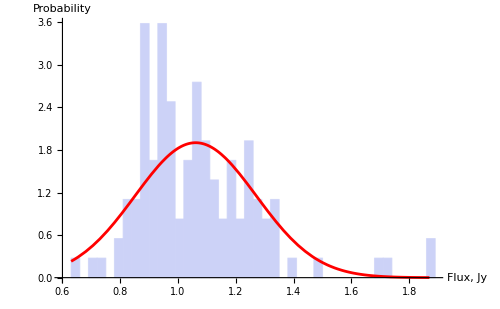
{7mm,-Graphics-,NormalDistribution[1.06091,0.209793],0.0000721328}

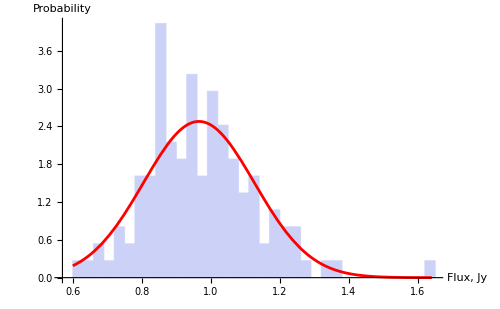
{13mm,-Graphics-,NormalDistribution[0.965403,0.160947],0.135393}

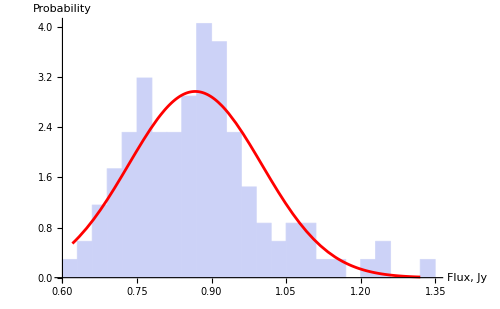
{2cm,-Graphics-,NormalDistribution[0.86713,0.134176],0.0184316}

{2cm,-Graphics-,NormalDistribution[0.86713,0.134176],0.0184316}

{13mm,-Graphics-,NormalDistribution[0.965403,0.160947],0.135393}

{7mm,-Graphics-,NormalDistribution[1.06091,0.209793],0.0000721328}

```mathematica
dat2cm=Transpose[her2cm][[2]];xmin=Min[dat2cm];xmax=Max[dat2cm];
dist=EstimatedDistribution[dat2cm,NormalDistribution[μ,σ]];
hist=Histogram[dat2cm,{0.03},"ProbabilityDensity"];
pl=Plot[PDF[dist,x],{x,xmin,xmax},PlotStyle->{Red,AbsoluteThickness[2]}];
plo=Show[{hist,pl},AxesLabel->{"Flux, Jy","Probability"},ImageSize->500];
test=DistributionFitTest[dat2cm];
{"2cm",plo,dist,test}

dat13mm=Transpose[her13mm][[2]];xmin=Min[dat13mm];xmax=Max[dat13mm];
dist=EstimatedDistribution[dat13mm,NormalDistribution[μ,σ]];
hist=Histogram[dat13mm,{0.03},"ProbabilityDensity"];
pl=Plot[PDF[dist,x],{x,xmin,xmax},PlotStyle->{Red,AbsoluteThickness[2]}];
plo=Show[{hist,pl},AxesLabel->{"Flux, Jy","Probability"},ImageSize->500];
test=DistributionFitTest[dat13mm];
{"13mm",plo,dist,test}

dat7mm=Transpose[her7mm][[2]];xmin=Min[dat7mm];xmax=Max[dat7mm];
dist=EstimatedDistribution[dat7mm,NormalDistribution[μ,σ]];
hist=Histogram[dat7mm,{0.03},"ProbabilityDensity"];
pl=Plot[PDF[dist,x],{x,xmin,xmax},PlotStyle->{Red,AbsoluteThickness[2]}];
plo=Show[{hist,pl},AxesLabel->{"Flux, Jy","Probability"},ImageSize->500];
test=DistributionFitTest[dat7mm];
{"7mm",plo,dist,test}
```

```mathematica
test=DistributionFitTest[dat7mm,Automatic,"HypothesisTestData"]
test["TestDataTable",All]
test=DistributionFitTest[dat13mm,Automatic,"HypothesisTestData"]
test["TestDataTable",All]
```

HypothesisTestData[«DistributionFitTest»]

| Statistic | P-Value
Anderson-Darling | 2.38147 | 1.44331×10^-6
Cramér-von Mises | 0.340934 | 0.0000721328
Jarque-Bera ALM | 92.8218 | 0.
Pearson χ^2 | 25.3636 | 0.00806204
Shapiro-Wilk | 0.904079 | 2.90815×10^-7

HypothesisTestData[«DistributionFitTest»]

| Statistic | P-Value
Anderson-Darling | 0.578776 | 0.133956
Cramér-von Mises | 0.0937559 | 0.135393
Jarque-Bera ALM | 24.4848 | 0.00365991
Pearson χ^2 | 16. | 0.141131
Shapiro-Wilk | 0.972399 | 0.0120798

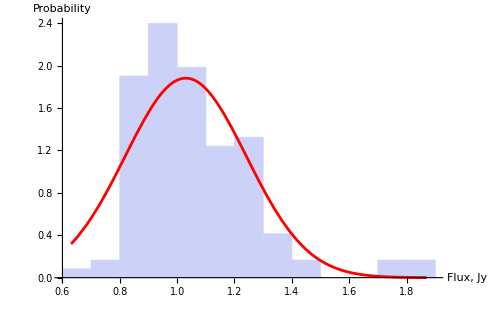
{7mm,-Graphics-,NormalDistribution[1.03,0.212058],0.0000721328}

```mathematica
dat7mm=Transpose[her7mm][[2]];xmin=Min[dat7mm];xmax=Max[dat7mm];
dist=EstimatedDistribution[dat7mm,NormalDistribution[Median[dat7mm],σ]];
hist=Histogram[dat7mm,{0.1},"ProbabilityDensity"];
pl=Plot[PDF[dist,x],{x,xmin,xmax},PlotStyle->{Red,AbsoluteThickness[2]}];
plo=Show[{hist,pl},AxesLabel->{"Flux, Jy","Probability"},ImageSize->500];
test=DistributionFitTest[dat7mm];
{"7mm",plo,dist,test}
```

```mathematica
pl2=ListPlot[her2cm,Joined->True,PlotStyle->Red];
pl13=ListPlot[her13mm,Joined->True,PlotStyle->Green];
pl7=ListPlot[her7mm,Joined->True,PlotStyle->Blue];
Show[{pl2,pl13,pl7}]
```

#### My simulations

```mathematica
dir="C:\\study\\mathematica\\3DMHD\\vary\\";sep=1;νtab={43,87,102,145,230,349,674,857};
el={ListLogPlot,ListPlot};
SetOptions[#,Frame->True,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->13},PlotStyle->AbsoluteThickness[1.5],FrameStyle->AbsoluteThickness[2.5]]&/@el;(*,FrameTicks->{{Automatic,None},{{43,87,145,230,345,690},None}}*)
Do[tr=Transpose[Import[dir<>"poliresa90th214nu"<>ToString[νtab[[i]]]<>"fn0.dat"]];
tr[[1]]=(2tr[[1]])/10^3;tmin=tr[[1,1]];tmax=tr[[1,-1]];
Print[GraphicsRow[{
Fpl[i]=ListLogPlot[Transpose[{tr[[1]],tr[[3]]}],FrameLabel->{{None,None},{None,"F_ν at ν="<>ToString[tr[[2,1]]]<>"GHz"}},Frame->True,PlotRange->{{tmin,tmax},{0.9Min[tr[[3]]],1.1Max[tr[[3]]]}},Joined->True],LPpl[i]=ListLogPlot[Transpose[{tr[[1]],tr[[4]]}],FrameLabel->{{None,None},{None,"LP at ν="<>ToString[tr[[2,1]]]<>"GHz"}},Frame->True,PlotRange->{{tmin,tmax},Automatic},Joined->True],
EVPApl[i]=ListPlot[Transpose[{tr[[1]],Mod[180+tr[[5]],180]}],FrameLabel->{{None,None},{None,"EVPA in deg at ν="<>ToString[tr[[2,1]]]<>"GHz"}},Frame->True,PlotRange->{{tmin,tmax},Automatic},Joined->True],
CPpl[i]=ListPlot[Transpose[{tr[[1]],tr[[6]]}],FrameLabel->{{None,None},{None,"CP in % at ν="<>ToString[tr[[2,1]]]<>"GHz"}},Frame->True,PlotRange->{{tmin,tmax},Automatic},Joined->True]},ImageSize->1200]],{i,5,5}];
```

```mathematica
data=tr[[6]];
xmin=Min[data];xmax=Max[data];(*dist=EmpiricalDistribution[data];*)
test=DistributionFitTest[data];
dist=EstimatedDistribution[data,NormalDistribution[μ,σ]];
dist2=EstimatedDistribution[data,CauchyDistribution[μ,σ]];
hist=Histogram[data,{0.05},"ProbabilityDensity"];
pl=Plot[PDF[dist,x],{x,xmin,xmax},PlotStyle->{Red,AbsoluteThickness[2]}];
pl2=Plot[PDF[dist2,x],{x,xmin,xmax},PlotStyle->{Green,AbsoluteThickness[2]}];
plo=Show[{hist,pl,pl2},AxesLabel->{"Flux, Jy","Probability"},ImageSize->500];
{ToString[tr[[2,1]]]<>" GHz: CP  ",test,plo,dist}
```

```mathematica
(*ℋ=DistributionFitTest[data,Automatic,"HypothesisTestData"];
ℋ["TestDataTable",All]*)
DistributionFitTest[data,Automatic,"KolmogorovSmirnov"]
```

```mathematica
n=40;Off[HypothesisTestData::ties];
tabprob=Table[rand=RandomSample[tr[[3]],n];DistributionFitTest[rand,Automatic,"KolmogorovSmirnov"],{i,1000}];
Median[tabprob](*p=0.05 at 300 points drawn of CP;25 points drawn of log(LP); ~1000 points drawn of LP; 40 points of flux*)
```

```mathematica
data=tr[[3]];SetOptions[Histogram,BaseStyle->{16}];
xmin=Min[data];xmax=Max[data];(*dist=EmpiricalDistribution[data];*)
test=DistributionFitTest[data];
dist=EstimatedDistribution[data,NormalDistribution[μ,σ]];
dist2=EstimatedDistribution[data,CauchyDistribution[μ,σ]];
hist=Histogram[data,{0.05},"ProbabilityDensity"];
pl=Plot[PDF[dist,x],{x,xmin,xmax},PlotStyle->{Red,AbsoluteThickness[2]}];
pl2=Plot[PDF[dist2,x],{x,xmin,xmax},PlotStyle->{Green,AbsoluteThickness[2]}];
plo=Show[{hist,pl,pl2},AxesLabel->{"Flux, Jy","Probability"},ImageSize->500];
{ToString[tr[[2,1]]]<>" GHz: total I  ",test,plo,dist}

data=Log[tr[[4]]];
xmin=Min[data];xmax=Max[data];(*dist=EmpiricalDistribution[data];*)
test=DistributionFitTest[data];
dist=EstimatedDistribution[data,NormalDistribution[Median[data],σ]];
dist2=EstimatedDistribution[data,CauchyDistribution[μ,σ]];
hist=Histogram[data,{0.2},"ProbabilityDensity"];
pl=Plot[PDF[dist,x],{x,xmin,xmax},PlotStyle->{Red,AbsoluteThickness[2]}];
pl2=Plot[PDF[dist2,x],{x,xmin,xmax},PlotStyle->{Green,AbsoluteThickness[2]}];
plo=Show[{hist,pl,pl2},AxesLabel->{"Log[LP,%], ","Probability"},ImageSize->500];
{ToString[tr[[2,1]]]<>" GHz: LP  ",test,plo,dist}

data=tr[[6]];
xmin=Min[data];xmax=Max[data];(*dist=EmpiricalDistribution[data];*)
test=DistributionFitTest[data];
dist=EstimatedDistribution[data,NormalDistribution[μ,σ]];
dist2=EstimatedDistribution[data,CauchyDistribution[μ,σ]];
hist=Histogram[data,{0.05},"ProbabilityDensity"];
pl=Plot[PDF[dist,x],{x,xmin,xmax},PlotStyle->{Red,AbsoluteThickness[2]}];
pl2=Plot[PDF[dist2,x],{x,xmin,xmax},PlotStyle->{Green,AbsoluteThickness[2]}];
plo=Show[{hist,pl,pl2},AxesLabel->{"CP, %","Probability"},ImageSize->500];
{ToString[tr[[2,1]]]<>" GHz: CP  ",test,plo,dist}

data=Mod[180+tr[[5]],180];
xmin=Min[data];xmax=Max[data];(*dist=EmpiricalDistribution[data];*)
test=DistributionFitTest[data];
dist=EstimatedDistribution[data,NormalDistribution[μ,σ]];
dist2=EstimatedDistribution[data,CauchyDistribution[μ,σ]];
hist=Histogram[data,{2},"ProbabilityDensity"];
pl=Plot[PDF[dist,x],{x,xmin,xmax},PlotStyle->{Red,AbsoluteThickness[2]}];
pl2=Plot[PDF[dist2,x],{x,xmin,xmax},PlotStyle->{Green,AbsoluteThickness[2]}];
plo=Show[{hist,pl,pl2},AxesLabel->{"EVPA, deg","Probability"},ImageSize->500];
{ToString[tr[[2,1]]]<>" GHz: EVPA  ",test,plo,dist}
```

```mathematica
Kurtosis[data](*CentralMoment[list,4]/CentralMoment[list,2]^2.*)
Skewness[data](*CentralMoment[list,3]/CentralMoment[list,2]^(3/2).*)
tutorial/ContinuousDistributions
```

```mathematica
dir="C:\\study\\mathematica\\3DMHD\\vary\\";sep=1;νtab={43,87,102,145,230,349,674,857};
el={ListLogPlot,ListPlot};
SetOptions[#,Frame->True,BaseStyle->{FontFamily->"Arial",FontWeight->"Bold",FontSize->13},PlotStyle->AbsoluteThickness[1.5],FrameStyle->AbsoluteThickness[2.5]]&/@el;(*,FrameTicks->{{Automatic,None},{{43,87,145,230,345,690},None}}*)
Do[tr=Transpose[Import[dir<>"poliresa90th214nu"<>ToString[νtab[[i]]]<>"fn0.dat"]];
tr[[1]]=(2tr[[1]])/10^3;tmin=tr[[1,1]];tmax=tr[[1,-1]];Print[νtab[[i]],"  I: ",dist=EstimatedDistribution[tr[[3]],NormalDistribution[μ,σ]];{dist[[1]],dist[[2]]},",  LP: ",dist=EstimatedDistribution[tr[[4]],NormalDistribution[μ,σ]];{dist[[1]],dist[[2]]},",  CP: ",dist=EstimatedDistribution[tr[[6]],NormalDistribution[μ,σ]];{dist[[1]],dist[[2]]}],{i,2,8}];
```

#### Other distributions

```mathematica
μ=3.9;σ=0.1;
dat=RandomVariate[NormalDistribution[4,σ],30]
Print["χ^2=",chisq=Total[((dat-μ)/σ)^2], "; dof=",Length[dat]]
Print[SurvivalFunction[ChiSquareDistribution[Length[dat]],chisq]," = p-value assuming normal distribution ⇒ χ^2 distribution"]
Print[TTest[dat,μ]," = t-test for assumed mean & computed standard deviation"]
Print[ZTest[dat,σ/(√Length[dat]),μ]," = z-test for assumed mean & standard deviation"]

Print[DistributionFitTest[dat,NormalDistribution[μ,σ]], " = can fit by normal distribution?"]

ℋ=DistributionFitTest[dat,NormalDistribution[μ,σ],"HypothesisTestData"];
ℋ["TestDataTable",All]
```

```mathematica
dat=RandomVariate[NormalDistribution[μ,σ],30]
dat2=RandomVariate[NormalDistribution[μ-σ,σ],20]
TTest[{dat,dat2}]
```

```mathematica
deg=.;Integrate[(√deg)/(2 √π)Exp[-(deg(x-1)^2)/4],{x,-∞,+∞},Assumptions->deg>0]
```

```mathematica
(*12 degrees of freedom*)deg=12;LogPlot[{(√deg)/(2 √π)Exp[-(deg(x-1)^2)/4],deg PDF[ChiSquareDistribution[deg],deg x]},{x,1-5/(√deg),1+10/(√deg)},PlotStyle->{Red,Blue}]
```

```mathematica
ndist=1/(√(2π)σ)Exp[-x^2/(2 σ^2)];deg=.;Integrate[ndist,{x,-∞,+∞},Assumptions->σ>0]
(*Y=X^2*)Ydist=(ndist+(ndist/.x->-x))/D[x^2,x] /.x->√y
Integrate[Ydist,{y,0,+∞},Assumptions->{σ>0}]
Yexp=Integrate[Ydist Exp[ⅈ ω y],{y,0,+∞},Assumptions->{σ>0},GenerateConditions->False]
(*N distributions*)
Yexptot=Yexp^n;
Ytot=Integrate[Yexptot Exp[-ⅈ ω y],{ω,-∞,+∞},Assumptions->{σ>0,n∈Integers,n>0,y>0},GenerateConditions->False]
cc=1/Integrate[Ytot,{y,0,+∞},Assumptions->{σ>0}][[1]];
Ychisq=cc Ytot(*Derived χ^2-distribution*)
```

### size of emitting region

```mathematica
pl1=ListLogLogPlot[{{87.73,33.},{102.00,24.},{145.00,15.},{230.86,13.},{349.00,11.},{674.00,8.},{857.00,7.}},Joined->True,PlotStyle->Blue];
pl2=LogLogPlot[8+(600/ν)^1.5,{ν,87,857},PlotStyle->Red];
Show[{pl1,pl2}]
{#,0.1Round[10(8+(600/#)^1.5)]}&/@{87.73,102.00,145.00,230.86,349.00,674.00,857.00}
```

```mathematica
2. √27
```

### Correlations of quantities

```mathematica
num=1000;xx=1.5;
fir=RandomVariate[NormalDistribution[],num];
sec=xx fir;
secx=RandomVariate[NormalDistribution[0,xx],num];
{Histogram[sec,ImageSize->500],Histogram[secx,ImageSize->500]}
```

```mathematica
{Mean[sec],Mean[secx]}
{StandardDeviation[sec],StandardDeviation[secx]}
{StandardDeviation[sec]/(√Length[sec]),StandardDeviation[secx]/(√Length[secx])}
```

```mathematica
num=10000;nn=100;
res=Transpose[Table[taxx=RandomVariate[NormalDistribution[],num];mm=Mean[taxx];err=StandardDeviation[taxx]/(√Length[taxx]);{mm,err},{i,nn}]];
Sort[res[[2]]];
Total[(res[[1]]/res[[2]])^2]/nn
```

```mathematica
ListPlot[res]
```

## Something else

```mathematica
Mod[180/π ArcTan[Q,U]/2,180]/.{U->-7.,Q->-244}
Mod[180/π ArcTan[Q,U]/2,180]/.{U->28,Q->-224.}
Mod[180/π ArcTan[Q,U]/2,180]/.{U->-176,Q->100.}
Mod[180/π ArcTan[Q,U]/2,180]/.{U->-14,Q->-12.}
```

```mathematica
dat={0.730,.590,.720,.69};
Mean[dat]
Median[dat]
Exp[Mean[Log[dat]]]
dat={0.95,0.8};exx={8,2};Exp[Total[(Log[dat]*exx)/Total[exx]]]
dada={{11, 88 ,1},{9, 110, 8},{4.96, 117, 3},{7.2, 139, 3},{5.9 ,114 ,1}};
Exp[Total[(Log[Transpose[dada][[1]]]*Transpose[dada][[3]])/Total[Transpose[dada][[3]]]]]
dada={{6.86, 149, 3},{5.87, 143, 3},{13,161,1}};
Exp[Total[(Log[Transpose[dada][[1]]]*Transpose[dada][[3]])/Total[Transpose[dada][[3]]]]]
```

```mathematica
Δχ2=(Log[0.9/1.1]/0.26)^2/12+(0.03/0.33)^2+(0.05/0.27)^2
Exp[-Δχ2/2]
```

```mathematica
(360. 60 60)/(2π 100 10^3)
(360 60 60.)/(3 10^9)
```

```mathematica
((3.4 10^5)/25)^0.2
((3.4 10^5)/25)^0.1
```